```mathematica
(*Simulate result on 16^4 sites lattice with Z2*)
```

```mathematica
x1={0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8};
(*data simulated*)
(*Set beta, run 1000 steps first, then, run 3000 steps for E*)
(*increase beta from 0.1 to 0.8*)
y1={0.9644395,0.932228,0.86845,0.7955222,0.6498525,0.4055241,0.2243037,0.1283225,0.05817301,0.04882579,0.040146,0.02774514,0.03233331,0.02854415,0.03666271};
(*decrease beta from 0.8 to 0.1*)
z1={0.9656972,0.9339105,0.8743563,0.7909998,0.6535755,0.4118887,0.2350546,0.1231947,0.06724618,0.04413027,0.03800783,0.03348425,0.03334782,0.03144938,0.03666271};
```

```mathematica
(* there is no difference between increase beta and decrease beta*)
```

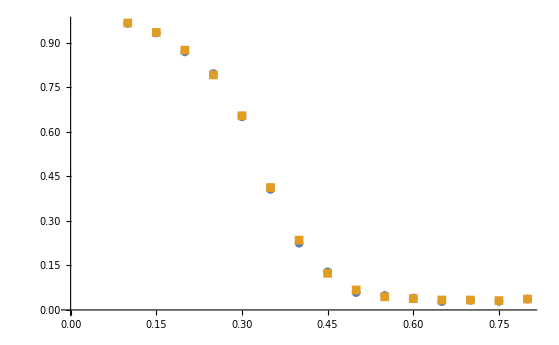

```mathematica
ListPlot[{Transpose[{x1,y1}],Transpose[{x1,z1}]},PlotMarkers->Automatic]
```

```mathematica
(*Simulate result on 16^4 sites lattice with Z2 and Z6 using *)
```

```mathematica
xcyc={0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.06500001,0.066,0.067,0.068,0.06900001,0.07,0.071,0.072,0.07300001,0.074,0.075,0.07600001,0.077,0.078,0.079,0.08000001,0.081,0.082,0.083,0.08400001,0.085,0.086,0.087,0.08800001,0.089,0.09,0.09100001,0.092,0.093,0.094,0.09500001,0.096,0.097,0.098,0.09900001,0.1,0.101,0.102,0.103,0.104,0.105,0.106,0.107,0.108,0.109,0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.121,0.122,0.123,0.124,0.125,0.126,0.127,0.128,0.129,0.13,0.131,0.132,0.133,0.134,0.135,0.136,0.137,0.138,0.139,0.14,0.141,0.142,0.143,0.144,0.145,0.146,0.147,0.148,0.149,0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19,0.191,0.192,0.193,0.194,0.195,0.196,0.197,0.198,0.199,0.2,0.201,0.202,0.203,0.204,0.205,0.206,0.207,0.208,0.209,0.21,0.211,0.212,0.213,0.214,0.215,0.216,0.217,0.218,0.219,0.22,0.221,0.222,0.223,0.224,0.225,0.226,0.227,0.228,0.229,0.23,0.231,0.232,0.233,0.234,0.235,0.236,0.237,0.238,0.239,0.24,0.241,0.242,0.243,0.244,0.245,0.246,0.247,0.248,0.249,0.25,0.251,0.252,0.253,0.254,0.255,0.256,0.257,0.258,0.259,0.26,0.261,0.262,0.263,0.264,0.265,0.266,0.267,0.268,0.269,0.27,0.271,0.272,0.273,0.274,0.275,0.276,0.277,0.278,0.279,0.28,0.281,0.282,0.283,0.284,0.285,0.286,0.287,0.288,0.289,0.29,0.291,0.292,0.293,0.294,0.295,0.296,0.297,0.298,0.299,0.3,0.301,0.302,0.303,0.304,0.305,0.306,0.307,0.308,0.309,0.31,0.311,0.312,0.313,0.314,0.315,0.316,0.317,0.318,0.319,0.32,0.321,0.322,0.323,0.324,0.325,0.326,0.327,0.328,0.329,0.33,0.331,0.332,0.333,0.334,0.335,0.336,0.337,0.338,0.339,0.34,0.341,0.342,0.343,0.344,0.345,0.346,0.347,0.348,0.349,0.35,0.351,0.352,0.353,0.354,0.355,0.356,0.357,0.358,0.359,0.36,0.361,0.362,0.363,0.364,0.365,0.366,0.367,0.368,0.369,0.37,0.371,0.372,0.373,0.374,0.375,0.376,0.377,0.378,0.379,0.38,0.381,0.382,0.383,0.384,0.385,0.386,0.387,0.388,0.389,0.39,0.391,0.392,0.393,0.394,0.395,0.396,0.397,0.398,0.399,0.4,0.401,0.402,0.403,0.404,0.405,0.406,0.407,0.408,0.409,0.41,0.411,0.412,0.413,0.414,0.415,0.416,0.417,0.418,0.419,0.42,0.421,0.422,0.423,0.424,0.425,0.426,0.427,0.428,0.429,0.43,0.431,0.432,0.433,0.434,0.435,0.436,0.437,0.438,0.439,0.44,0.441,0.442,0.443,0.444,0.445,0.446,0.447,0.448,0.449,0.45,0.451,0.452,0.453,0.454,0.455,0.456,0.457,0.458,0.459,0.46,0.461,0.462,0.463,0.464,0.465,0.466,0.467,0.468,0.469,0.47,0.471,0.472,0.473,0.474,0.475,0.476,0.477,0.478,0.479,0.48,0.481,0.482,0.483,0.484,0.485,0.486,0.487,0.488,0.489,0.49,0.491,0.492,0.493,0.494,0.495,0.496,0.497,0.498,0.499,0.5,0.501,0.502,0.503,0.504,0.505,0.506,0.507,0.508,0.509,0.5100001,0.511,0.512,0.513,0.514,0.515,0.516,0.517,0.518,0.5190001,0.52,0.521,0.522,0.523,0.524,0.525,0.526,0.527,0.528,0.529,0.53,0.531,0.532,0.5330001,0.534,0.535,0.536,0.537,0.538,0.539,0.54,0.541,0.542,0.543,0.544,0.545,0.546,0.5470001,0.548,0.549,0.55,0.551,0.552,0.553,0.554,0.555,0.5560001,0.557,0.558,0.559,0.56,0.561,0.562,0.563,0.564,0.565,0.566,0.567,0.568,0.569,0.5700001,0.571,0.572,0.573,0.574,0.575,0.576,0.577,0.578,0.5790001,0.58,0.581,0.582,0.583,0.5840001,0.585,0.586,0.587,0.588,0.589,0.59,0.591,0.592,0.5930001,0.594,0.595,0.596,0.597,0.598,0.599,0.6,0.601,0.602,0.603,0.604,0.605,0.606,0.6070001,0.608,0.609,0.61,0.611,0.612,0.613,0.614,0.615,0.6160001,0.617,0.618,0.619,0.62,0.6210001,0.622,0.623,0.624,0.625,0.626,0.627,0.628,0.629,0.6300001,0.631,0.632,0.633,0.634,0.6350001,0.636,0.637,0.638,0.6390001,0.64,0.641,0.642,0.643,0.6440001,0.645,0.646,0.647,0.648,0.649,0.65,0.651,0.652,0.6530001,0.654,0.655,0.656,0.657,0.6580001,0.659,0.66,0.661,0.6620001,0.663,0.664,0.665,0.666,0.6670001,0.668,0.669,0.67,0.671,0.6720001,0.673,0.674,0.675,0.6760001,0.677,0.678,0.679,0.68,0.6810001,0.682,0.683,0.684,0.685,0.686,0.687,0.688,0.689,0.6900001,0.691,0.692,0.693,0.694,0.6950001,0.696,0.697,0.698,0.6990001,0.7,0.701,0.702,0.703,0.7040001,0.705,0.706,0.707,0.708,0.7090001,0.71,0.711,0.712,0.7130001,0.714,0.715,0.716,0.717,0.7180001,0.719,0.72,0.721,0.7220001,0.723,0.724,0.725,0.726,0.7270001,0.728,0.729,0.73,0.731,0.7320001,0.733,0.734,0.735,0.7360001,0.737,0.738,0.739,0.74,0.7410001,0.742,0.743,0.744,0.7450001,0.7460001,0.747,0.748,0.749,0.7500001,0.751,0.752,0.753,0.754,0.7550001,0.756,0.757,0.758,0.7590001,0.7600001,0.761,0.762,0.763,0.7640001,0.765,0.766,0.767,0.768,0.7690001,0.77,0.771,0.772,0.7730001,0.774,0.775,0.776,0.777,0.7780001,0.779,0.78,0.781,0.7820001,0.7830001,0.784,0.785,0.786,0.7870001,0.788,0.789,0.79,0.791,0.7920001,0.793,0.794,0.795,0.7960001,0.7970001,0.798,0.799,0.8,0.8010001,0.802,0.803,0.804,0.8050001,0.8060001,0.807,0.808,0.809,0.8100001,0.811,0.812,0.813,0.814,0.8150001,0.816,0.817,0.818,0.8190001,0.8200001,0.821,0.822,0.823,0.8240001,0.825,0.826,0.827,0.828,0.8290001,0.83,0.831,0.832,0.8330001,0.8340001,0.835,0.836,0.837,0.8380001,0.839,0.84,0.841,0.8420001,0.8430001,0.844,0.845,0.846,0.8470001,0.848,0.849,0.85,0.851,0.8520001,0.853,0.854,0.855,0.8560001,0.8570001,0.858,0.859,0.86,0.8610001,0.862,0.863,0.864,0.8650001,0.8660001,0.867,0.868,0.869,0.8700001,0.8710001,0.872,0.873,0.874,0.8750001,0.876,0.877,0.878,0.8790001,0.8800001,0.881,0.882,0.883,0.8840001,0.8850001,0.886,0.887,0.8880001,0.8890001,0.89,0.891,0.892,0.8930001,0.8940001,0.895,0.896,0.897,0.8980001,0.899,0.9,0.901,0.9020001,0.9030001,0.904,0.905,0.906,0.9070001,0.9080001,0.909,0.91,0.911,0.9120001,0.913,0.914,0.915,0.9160001,0.9170001,0.918,0.919,0.92,0.9210001,0.9220001,0.923,0.924,0.9250001,0.9260001,0.927,0.928,0.929,0.9300001,0.9310001,0.932,0.933,0.934,0.9350001,0.936,0.937,0.938,0.9390001,0.9400001,0.941,0.942,0.943,0.9440001,0.9450001,0.946,0.947,0.9480001,0.9490001,0.95,0.951,0.952,0.9530001,0.9540001,0.955,0.956,0.957,0.9580001,0.9590001,0.96,0.961,0.9620001,0.9630001,0.964,0.965,0.966,0.9670001,0.9680001,0.969,0.97,0.971,0.9720001,0.973,0.974,0.975,0.9760001,0.9770001,0.978,0.979,0.98,0.9810001,0.9820001,0.983,0.984,0.9850001,0.9860001,0.987,0.988,0.989,0.9900001,0.9910001,0.992,0.993,0.994,0.9950001,0.9960001,0.997,0.998,0.9990001,1,1.001,1.002,1.003,1.004,1.005,1.006,1.007,1.008,1.009,1.01,1.011,1.012,1.013,1.014,1.015,1.016,1.017,1.018,1.019,1.02,1.021,1.022,1.023,1.024,1.025,1.026,1.027,1.028,1.029,1.03,1.031,1.032,1.033,1.034,1.035,1.036,1.037,1.038,1.039,1.04,1.041,1.042,1.043,1.044,1.045,1.046,1.047,1.048,1.049,1.05,1.051,1.052,1.053,1.054,1.055,1.056,1.057,1.058,1.059,1.06,1.061,1.062,1.063,1.064,1.065,1.066,1.067,1.068,1.069,1.07,1.071,1.072,1.073,1.074,1.075,1.076,1.077,1.078,1.079,1.08,1.081,1.082,1.083,1.084,1.085,1.086,1.087,1.088,1.089,1.09,1.091,1.092,1.093,1.094,1.095,1.096,1.097,1.098,1.099,1.1,1.101,1.102,1.103,1.104,1.105,1.106,1.107,1.108,1.109,1.11,1.111,1.112,1.113,1.114,1.115,1.116,1.117,1.118,1.119,1.12,1.121,1.122,1.123,1.124,1.125,1.126,1.127,1.128,1.129,1.13,1.131,1.132,1.133,1.134,1.135,1.136,1.137,1.138,1.139,1.14,1.141,1.142,1.143,1.144,1.145,1.146,1.147,1.148,1.149,1.15,1.151,1.152,1.153,1.154,1.155,1.156,1.157,1.158,1.159,1.16,1.161,1.162,1.163,1.164,1.165,1.166,1.167,1.168,1.169,1.17,1.171,1.172,1.173,1.174,1.175,1.176,1.177,1.178,1.179,1.18,1.181,1.182,1.183,1.184,1.185,1.186,1.187,1.188,1.189,1.19,1.191,1.192,1.193,1.194,1.195,1.196,1.197,1.198,1.199,1.2,1.201,1.202,1.203,1.204,1.205,1.206,1.207,1.208,1.209,1.21,1.211,1.212,1.213,1.214,1.215,1.216,1.217,1.218,1.219,1.22,1.221,1.222,1.223,1.224,1.225,1.226,1.227,1.228,1.229,1.23,1.231,1.232,1.233,1.234,1.235,1.236,1.237,1.238,1.239,1.24,1.241,1.242,1.243,1.244,1.245,1.246,1.247,1.248,1.249,1.25,1.251,1.252,1.253,1.254,1.255,1.256,1.257,1.258,1.259,1.26,1.261,1.262,1.263,1.264,1.265,1.266,1.267,1.268,1.269,1.27,1.271,1.272,1.273,1.274,1.275,1.276,1.277,1.278,1.279,1.28,1.281,1.282,1.283,1.284,1.285,1.286,1.287,1.288,1.289,1.29,1.291,1.292,1.293,1.294,1.295,1.296,1.297,1.298,1.299,1.3,1.301,1.302,1.303,1.304,1.305,1.306,1.307,1.308,1.309,1.31,1.311,1.312,1.313,1.314,1.315,1.316,1.317,1.318,1.319,1.32,1.321,1.322,1.323,1.324,1.325,1.326,1.327,1.328,1.329,1.33,1.331,1.332,1.333,1.334,1.335,1.336,1.337,1.338,1.339,1.34,1.341,1.342,1.343,1.344,1.345,1.346,1.347,1.348,1.349,1.35,1.351,1.352,1.353,1.354,1.355,1.356,1.357,1.358,1.359,1.36,1.361,1.362,1.363,1.364,1.365,1.366,1.367,1.368,1.369,1.37,1.371,1.372,1.373,1.374,1.375,1.376,1.377,1.378,1.379,1.38,1.381,1.382,1.383,1.384,1.385,1.386,1.387,1.388,1.389,1.39,1.391,1.392,1.393,1.394,1.395,1.396,1.397,1.398,1.399,1.4,1.401,1.402,1.403,1.404,1.405,1.406,1.407,1.408,1.409,1.41,1.411,1.412,1.413,1.414,1.415,1.416,1.417,1.418,1.419,1.42,1.421,1.422,1.423,1.424,1.425,1.426,1.427,1.428,1.429,1.43,1.431,1.432,1.433,1.434,1.435,1.436,1.437,1.438,1.439,1.44,1.441,1.442,1.443,1.444,1.445,1.446,1.447,1.448,1.449,1.45,1.451,1.452,1.453,1.454,1.455,1.456,1.457,1.458,1.459,1.46,1.461,1.462,1.463,1.464,1.465,1.466,1.467,1.468,1.469,1.47,1.471,1.472,1.473,1.474,1.475,1.476,1.477,1.478,1.479,1.48,1.481,1.482,1.483,1.484,1.485,1.486,1.487,1.488,1.489,1.49,1.491,1.492,1.493,1.494,1.495,1.496,1.497,1.498,1.499,1.5,1.501,1.502,1.503,1.504,1.505,1.506,1.507,1.508,1.509,1.51,1.511,1.512,1.513,1.514,1.515,1.516,1.517,1.518,1.519,1.52,1.521,1.522,1.523,1.524,1.525,1.526,1.527,1.528,1.529,1.53,1.531,1.532,1.533,1.534,1.535,1.536,1.537,1.538,1.539,1.54,1.541,1.542,1.543,1.544,1.545,1.546,1.547,1.548,1.549,1.55,1.551,1.552,1.553,1.554,1.555,1.556,1.557,1.558,1.559,1.56,1.561,1.562,1.563,1.564,1.565,1.566,1.567,1.568,1.569,1.57,1.571,1.572,1.573,1.574,1.575,1.576,1.577,1.578,1.579,1.58,1.581,1.582,1.583,1.584,1.585,1.586,1.587,1.588,1.589,1.59,1.591,1.592,1.593,1.594,1.595,1.596,1.597,1.598,1.599,1.6,1.601,1.602,1.603,1.604,1.605,1.606,1.607,1.608,1.609,1.61,1.611,1.612,1.613,1.614,1.615,1.616,1.617,1.618,1.619,1.62,1.621,1.622,1.623,1.624,1.625,1.626,1.627,1.628,1.629,1.63,1.631,1.632,1.633,1.634,1.635,1.636,1.637,1.638,1.639,1.64,1.641,1.642,1.643,1.644,1.645,1.646,1.647,1.648,1.649,1.65,1.651,1.652,1.653,1.654,1.655,1.656,1.657,1.658,1.659,1.66,1.661,1.662,1.663,1.664,1.665,1.666,1.667,1.668,1.669,1.67,1.671,1.672,1.673,1.674,1.675,1.676,1.677,1.678,1.679,1.68,1.681,1.682,1.683,1.684,1.685,1.686,1.687,1.688,1.689,1.69,1.691,1.692,1.693,1.694,1.695,1.696,1.697,1.698,1.699,1.7,1.701,1.702,1.703,1.704,1.705,1.706,1.707,1.708,1.709,1.71,1.711,1.712,1.713,1.714,1.715,1.716,1.717,1.718,1.719,1.72,1.721,1.722,1.723,1.724,1.725,1.726,1.727,1.728,1.729,1.73,1.731,1.732,1.733,1.734,1.735,1.736,1.737,1.738,1.739,1.74,1.741,1.742,1.743,1.744,1.745,1.746,1.747,1.748,1.749,1.75,1.751,1.752,1.753,1.754,1.755,1.756,1.757,1.758,1.759,1.76,1.761,1.762,1.763,1.764,1.765,1.766,1.767,1.768,1.769,1.77,1.771,1.772,1.773,1.774,1.775,1.776,1.777,1.778,1.779,1.78,1.781,1.782,1.783,1.784,1.785,1.786,1.787,1.788,1.789,1.79,1.791,1.792,1.793,1.794,1.795,1.796,1.797,1.798,1.799,1.8,1.801,1.802,1.803,1.804,1.805,1.806,1.807,1.808,1.809,1.81,1.811,1.812,1.813,1.814,1.815,1.816,1.817,1.818,1.819,1.82,1.821,1.822,1.823,1.824,1.825,1.826,1.827,1.828,1.829,1.83,1.831,1.832,1.833,1.834,1.835,1.836,1.837,1.838,1.839,1.84,1.841,1.842,1.843,1.844,1.845,1.846,1.847,1.848,1.849,1.85,1.851,1.852,1.853,1.854,1.855,1.856,1.857,1.858,1.859,1.86,1.861,1.862,1.863,1.864,1.865,1.866,1.867,1.868,1.869,1.87,1.871,1.872,1.873,1.874,1.875,1.876,1.877,1.878,1.879,1.88,1.881,1.882,1.883,1.884,1.885,1.886,1.887,1.888,1.889,1.89,1.891,1.892,1.893,1.894,1.895,1.896,1.897,1.898,1.899,1.9,1.901,1.902,1.903,1.904,1.905,1.906,1.907,1.908,1.909,1.91,1.911,1.912,1.913,1.914,1.915,1.916,1.917,1.918,1.919,1.92,1.921,1.922,1.923,1.924,1.925,1.926,1.927,1.928,1.929,1.93,1.931,1.932,1.933,1.934,1.935,1.936,1.937,1.938,1.939,1.94,1.941,1.942,1.943,1.944,1.945,1.946,1.947,1.948,1.949,1.95,1.951,1.952,1.953,1.954,1.955,1.956,1.957,1.958,1.959,1.96,1.961,1.962,1.963,1.964,1.965,1.966,1.967,1.968,1.969,1.97,1.971,1.972,1.973,1.974,1.975,1.976,1.977,1.978,1.979,1.98,1.981,1.982,1.983,1.984,1.985,1.986,1.987,1.988,1.989,1.99,1.991,1.992,1.993,1.994,1.995,1.996,1.997,1.998,1.999,2,1.999,1.998,1.997,1.996,1.995,1.994,1.993,1.992,1.991,1.99,1.989,1.988,1.987,1.986,1.985,1.984,1.983,1.982,1.981,1.98,1.979,1.978,1.977,1.976,1.975,1.974,1.973,1.972,1.971,1.97,1.969,1.968,1.967,1.966,1.965,1.964,1.963,1.962,1.961,1.96,1.959,1.958,1.957,1.956,1.955,1.954,1.953,1.952,1.951,1.95,1.949,1.948,1.947,1.946,1.945,1.944,1.943,1.942,1.941,1.94,1.939,1.938,1.937,1.936,1.935,1.934,1.933,1.932,1.931,1.93,1.929,1.928,1.927,1.926,1.925,1.924,1.923,1.922,1.921,1.92,1.919,1.918,1.917,1.916,1.915,1.914,1.913,1.912,1.911,1.91,1.909,1.908,1.907,1.906,1.905,1.904,1.903,1.902,1.901,1.9,1.899,1.898,1.897,1.896,1.895,1.894,1.893,1.892,1.891,1.89,1.889,1.888,1.887,1.886,1.885,1.884,1.883,1.882,1.881,1.88,1.879,1.878,1.877,1.876,1.875,1.874,1.873,1.872,1.871,1.87,1.869,1.868,1.867,1.866,1.865,1.864,1.863,1.862,1.861,1.86,1.859,1.858,1.857,1.856,1.855,1.854,1.853,1.852,1.851,1.85,1.849,1.848,1.847,1.846,1.845,1.844,1.843,1.842,1.841,1.84,1.839,1.838,1.837,1.836,1.835,1.834,1.833,1.832,1.831,1.83,1.829,1.828,1.827,1.826,1.825,1.824,1.823,1.822,1.821,1.82,1.819,1.818,1.817,1.816,1.815,1.814,1.813,1.812,1.811,1.81,1.809,1.808,1.807,1.806,1.805,1.804,1.803,1.802,1.801,1.8,1.799,1.798,1.797,1.796,1.795,1.794,1.793,1.792,1.791,1.79,1.789,1.788,1.787,1.786,1.785,1.784,1.783,1.782,1.781,1.78,1.779,1.778,1.777,1.776,1.775,1.774,1.773,1.772,1.771,1.77,1.769,1.768,1.767,1.766,1.765,1.764,1.763,1.762,1.761,1.76,1.759,1.758,1.757,1.756,1.755,1.754,1.753,1.752,1.751,1.75,1.749,1.748,1.747,1.746,1.745,1.744,1.743,1.742,1.741,1.74,1.739,1.738,1.737,1.736,1.735,1.734,1.733,1.732,1.731,1.73,1.729,1.728,1.727,1.726,1.725,1.724,1.723,1.722,1.721,1.72,1.719,1.718,1.717,1.716,1.715,1.714,1.713,1.712,1.711,1.71,1.709,1.708,1.707,1.706,1.705,1.704,1.703,1.702,1.701,1.7,1.699,1.698,1.697,1.696,1.695,1.694,1.693,1.692,1.691,1.69,1.689,1.688,1.687,1.686,1.685,1.684,1.683,1.682,1.681,1.68,1.679,1.678,1.677,1.676,1.675,1.674,1.673,1.672,1.671,1.67,1.669,1.668,1.667,1.666,1.665,1.664,1.663,1.662,1.661,1.66,1.659,1.658,1.657,1.656,1.655,1.654,1.653,1.652,1.651,1.65,1.649,1.648,1.647,1.646,1.645,1.644,1.643,1.642,1.641,1.64,1.639,1.638,1.637,1.636,1.635,1.634,1.633,1.632,1.631,1.63,1.629,1.628,1.627,1.626,1.625,1.624,1.623,1.622,1.621,1.62,1.619,1.618,1.617,1.616,1.615,1.614,1.613,1.612,1.611,1.61,1.609,1.608,1.607,1.606,1.605,1.604,1.603,1.602,1.601,1.6,1.599,1.598,1.597,1.596,1.595,1.594,1.593,1.592,1.591,1.59,1.589,1.588,1.587,1.586,1.585,1.584,1.583,1.582,1.581,1.58,1.579,1.578,1.577,1.576,1.575,1.574,1.573,1.572,1.571,1.57,1.569,1.568,1.567,1.566,1.565,1.564,1.563,1.562,1.561,1.56,1.559,1.558,1.557,1.556,1.555,1.554,1.553,1.552,1.551,1.55,1.549,1.548,1.547,1.546,1.545,1.544,1.543,1.542,1.541,1.54,1.539,1.538,1.537,1.536,1.535,1.534,1.533,1.532,1.531,1.53,1.529,1.528,1.527,1.526,1.525,1.524,1.523,1.522,1.521,1.52,1.519,1.518,1.517,1.516,1.515,1.514,1.513,1.512,1.511,1.51,1.509,1.508,1.507,1.506,1.505,1.504,1.503,1.502,1.501,1.5,1.499,1.498,1.497,1.496,1.495,1.494,1.493,1.492,1.491,1.49,1.489,1.488,1.487,1.486,1.485,1.484,1.483,1.482,1.481,1.48,1.479,1.478,1.477,1.476,1.475,1.474,1.473,1.472,1.471,1.47,1.469,1.468,1.467,1.466,1.465,1.464,1.463,1.462,1.461,1.46,1.459,1.458,1.457,1.456,1.455,1.454,1.453,1.452,1.451,1.45,1.449,1.448,1.447,1.446,1.445,1.444,1.443,1.442,1.441,1.44,1.439,1.438,1.437,1.436,1.435,1.434,1.433,1.432,1.431,1.43,1.429,1.428,1.427,1.426,1.425,1.424,1.423,1.422,1.421,1.42,1.419,1.418,1.417,1.416,1.415,1.414,1.413,1.412,1.411,1.41,1.409,1.408,1.407,1.406,1.405,1.404,1.403,1.402,1.401,1.4,1.399,1.398,1.397,1.396,1.395,1.394,1.393,1.392,1.391,1.39,1.389,1.388,1.387,1.386,1.385,1.384,1.383,1.382,1.381,1.38,1.379,1.378,1.377,1.376,1.375,1.374,1.373,1.372,1.371,1.37,1.369,1.368,1.367,1.366,1.365,1.364,1.363,1.362,1.361,1.36,1.359,1.358,1.357,1.356,1.355,1.354,1.353,1.352,1.351,1.35,1.349,1.348,1.347,1.346,1.345,1.344,1.343,1.342,1.341,1.34,1.339,1.338,1.337,1.336,1.335,1.334,1.333,1.332,1.331,1.33,1.329,1.328,1.327,1.326,1.325,1.324,1.323,1.322,1.321,1.32,1.319,1.318,1.317,1.316,1.315,1.314,1.313,1.312,1.311,1.31,1.309,1.308,1.307,1.306,1.305,1.304,1.303,1.302,1.301,1.3,1.299,1.298,1.297,1.296,1.295,1.294,1.293,1.292,1.291,1.29,1.289,1.288,1.287,1.286,1.285,1.284,1.283,1.282,1.281,1.28,1.279,1.278,1.277,1.276,1.275,1.274,1.273,1.272,1.271,1.27,1.269,1.268,1.267,1.266,1.265,1.264,1.263,1.262,1.261,1.26,1.259,1.258,1.257,1.256,1.255,1.254,1.253,1.252,1.251,1.25,1.249,1.248,1.247,1.246,1.245,1.244,1.243,1.242,1.241,1.24,1.239,1.238,1.237,1.236,1.235,1.234,1.233,1.232,1.231,1.23,1.229,1.228,1.227,1.226,1.225,1.224,1.223,1.222,1.221,1.22,1.219,1.218,1.217,1.216,1.215,1.214,1.213,1.212,1.211,1.21,1.209,1.208,1.207,1.206,1.205,1.204,1.203,1.202,1.201,1.2,1.199,1.198,1.197,1.196,1.195,1.194,1.193,1.192,1.191,1.19,1.189,1.188,1.187,1.186,1.185,1.184,1.183,1.182,1.181,1.18,1.179,1.178,1.177,1.176,1.175,1.174,1.173,1.172,1.171,1.17,1.169,1.168,1.167,1.166,1.165,1.164,1.163,1.162,1.161,1.16,1.159,1.158,1.157,1.156,1.155,1.154,1.153,1.152,1.151,1.15,1.149,1.148,1.147,1.146,1.145,1.144,1.143,1.142,1.141,1.14,1.139,1.138,1.137,1.136,1.135,1.134,1.133,1.132,1.131,1.13,1.129,1.128,1.127,1.126,1.125,1.124,1.123,1.122,1.121,1.12,1.119,1.118,1.117,1.116,1.115,1.114,1.113,1.112,1.111,1.11,1.109,1.108,1.107,1.106,1.105,1.104,1.103,1.102,1.101,1.1,1.099,1.098,1.097,1.096,1.095,1.094,1.093,1.092,1.091,1.09,1.089,1.088,1.087,1.086,1.085,1.084,1.083,1.082,1.081,1.08,1.079,1.078,1.077,1.076,1.075,1.074,1.073,1.072,1.071,1.07,1.069,1.068,1.067,1.066,1.065,1.064,1.063,1.062,1.061,1.06,1.059,1.058,1.057,1.056,1.055,1.054,1.053,1.052,1.051,1.05,1.049,1.048,1.047,1.046,1.045,1.044,1.043,1.042,1.041,1.04,1.039,1.038,1.037,1.036,1.035,1.034,1.033,1.032,1.031,1.03,1.029,1.028,1.027,1.026,1.025,1.024,1.023,1.022,1.021,1.02,1.019,1.018,1.017,1.016,1.015,1.014,1.013,1.012,1.011,1.01,1.009,1.008,1.007,1.006,1.005,1.004,1.003,1.002,1.001,1,0.9990001,0.998,0.997,0.9960001,0.9950001,0.994,0.993,0.992,0.9910001,0.9900001,0.989,0.988,0.987,0.9860001,0.9850001,0.984,0.983,0.9820001,0.9810001,0.98,0.979,0.978,0.9770001,0.9760001,0.975,0.974,0.973,0.9720001,0.971,0.97,0.969,0.9680001,0.9670001,0.966,0.965,0.964,0.9630001,0.9620001,0.961,0.96,0.9590001,0.9580001,0.957,0.956,0.955,0.9540001,0.9530001,0.952,0.951,0.95,0.9490001,0.9480001,0.947,0.946,0.9450001,0.9440001,0.943,0.942,0.941,0.9400001,0.9390001,0.938,0.937,0.936,0.9350001,0.934,0.933,0.932,0.9310001,0.9300001,0.929,0.928,0.927,0.9260001,0.9250001,0.924,0.923,0.9220001,0.9210001,0.92,0.919,0.918,0.9170001,0.9160001,0.915,0.914,0.913,0.9120001,0.911,0.91,0.909,0.9080001,0.9070001,0.906,0.905,0.904,0.9030001,0.9020001,0.901,0.9,0.899,0.8980001,0.897,0.896,0.895,0.8940001,0.8930001,0.892,0.891,0.89,0.8890001,0.8880001,0.887,0.886,0.8850001,0.8840001,0.883,0.882,0.881,0.8800001,0.8790001,0.878,0.877,0.876,0.8750001,0.874,0.873,0.872,0.8710001,0.8700001,0.869,0.868,0.867,0.8660001,0.8650001,0.864,0.863,0.862,0.8610001,0.86,0.859,0.858,0.8570001,0.8560001,0.855,0.854,0.853,0.8520001,0.851,0.85,0.849,0.848,0.8470001,0.846,0.845,0.844,0.8430001,0.8420001,0.841,0.84,0.839,0.8380001,0.837,0.836,0.835,0.8340001,0.8330001,0.832,0.831,0.83,0.8290001,0.828,0.827,0.826,0.825,0.8240001,0.823,0.822,0.821,0.8200001,0.8190001,0.818,0.817,0.816,0.8150001,0.814,0.813,0.812,0.811,0.8100001,0.809,0.808,0.807,0.8060001,0.8050001,0.804,0.803,0.802,0.8010001,0.8,0.799,0.798,0.7970001,0.7960001,0.795,0.794,0.793,0.7920001,0.791,0.79,0.789,0.788,0.7870001,0.786,0.785,0.784,0.7830001,0.7820001,0.781,0.78,0.779,0.7780001,0.777,0.776,0.775,0.774,0.7730001,0.772,0.771,0.77,0.7690001,0.768,0.767,0.766,0.765,0.7640001,0.763,0.762,0.761,0.7600001,0.7590001,0.758,0.757,0.756,0.7550001,0.754,0.753,0.752,0.751,0.7500001,0.749,0.748,0.747,0.7460001,0.7450001,0.744,0.743,0.742,0.7410001,0.74,0.739,0.738,0.737,0.7360001,0.735,0.734,0.733,0.7320001,0.731,0.73,0.729,0.728,0.7270001,0.726,0.725,0.724,0.723,0.7220001,0.721,0.72,0.719,0.7180001,0.717,0.716,0.715,0.714,0.7130001,0.712,0.711,0.71,0.7090001,0.708,0.707,0.706,0.705,0.7040001,0.703,0.702,0.701,0.7,0.6990001,0.698,0.697,0.696,0.6950001,0.694,0.693,0.692,0.691,0.6900001,0.689,0.688,0.687,0.686,0.685,0.684,0.683,0.682,0.6810001,0.68,0.679,0.678,0.677,0.6760001,0.675,0.674,0.673,0.6720001,0.671,0.67,0.669,0.668,0.6670001,0.666,0.665,0.664,0.663,0.6620001,0.661,0.66,0.659,0.6580001,0.657,0.656,0.655,0.654,0.6530001,0.652,0.651,0.65,0.649,0.648,0.647,0.646,0.645,0.6440001,0.643,0.642,0.641,0.64,0.6390001,0.638,0.637,0.636,0.6350001,0.634,0.633,0.632,0.631,0.6300001,0.629,0.628,0.627,0.626,0.625,0.624,0.623,0.622,0.6210001,0.62,0.619,0.618,0.617,0.6160001,0.615,0.614,0.613,0.612,0.611,0.61,0.609,0.608,0.6070001,0.606,0.605,0.604,0.603,0.602,0.601,0.6,0.599,0.598,0.597,0.596,0.595,0.594,0.5930001,0.592,0.591,0.59,0.589,0.588,0.587,0.586,0.585,0.5840001,0.583,0.582,0.581,0.58,0.5790001,0.578,0.577,0.576,0.575,0.574,0.573,0.572,0.571,0.5700001,0.569,0.568,0.567,0.566,0.565,0.564,0.563,0.562,0.561,0.56,0.559,0.558,0.557,0.5560001,0.555,0.554,0.553,0.552,0.551,0.55,0.549,0.548,0.5470001,0.546,0.545,0.544,0.543,0.542,0.541,0.54,0.539,0.538,0.537,0.536,0.535,0.534,0.5330001,0.532,0.531,0.53,0.529,0.528,0.527,0.526,0.525,0.524,0.523,0.522,0.521,0.52,0.5190001,0.518,0.517,0.516,0.515,0.514,0.513,0.512,0.511,0.5100001,0.509,0.508,0.507,0.506,0.505,0.504,0.503,0.502,0.501,0.5,0.499,0.498,0.497,0.496,0.495,0.494,0.493,0.492,0.491,0.49,0.489,0.488,0.487,0.486,0.485,0.484,0.483,0.482,0.481,0.48,0.479,0.478,0.477,0.476,0.475,0.474,0.473,0.472,0.471,0.47,0.469,0.468,0.467,0.466,0.465,0.464,0.463,0.462,0.461,0.46,0.459,0.458,0.457,0.456,0.455,0.454,0.453,0.452,0.451,0.45,0.449,0.448,0.447,0.446,0.445,0.444,0.443,0.442,0.441,0.44,0.439,0.438,0.437,0.436,0.435,0.434,0.433,0.432,0.431,0.43,0.429,0.428,0.427,0.426,0.425,0.424,0.423,0.422,0.421,0.42,0.419,0.418,0.417,0.416,0.415,0.414,0.413,0.412,0.411,0.41,0.409,0.408,0.407,0.406,0.405,0.404,0.403,0.402,0.401,0.4,0.399,0.398,0.397,0.396,0.395,0.394,0.393,0.392,0.391,0.39,0.389,0.388,0.387,0.386,0.385,0.384,0.383,0.382,0.381,0.38,0.379,0.378,0.377,0.376,0.375,0.374,0.373,0.372,0.371,0.37,0.369,0.368,0.367,0.366,0.365,0.364,0.363,0.362,0.361,0.36,0.359,0.358,0.357,0.356,0.355,0.354,0.353,0.352,0.351,0.35,0.349,0.348,0.347,0.346,0.345,0.344,0.343,0.342,0.341,0.34,0.339,0.338,0.337,0.336,0.335,0.334,0.333,0.332,0.331,0.33,0.329,0.328,0.327,0.326,0.325,0.324,0.323,0.322,0.321,0.32,0.319,0.318,0.317,0.316,0.315,0.314,0.313,0.312,0.311,0.31,0.309,0.308,0.307,0.306,0.305,0.304,0.303,0.302,0.301,0.3,0.299,0.298,0.297,0.296,0.295,0.294,0.293,0.292,0.291,0.29,0.289,0.288,0.287,0.286,0.285,0.284,0.283,0.282,0.281,0.28,0.279,0.278,0.277,0.276,0.275,0.274,0.273,0.272,0.271,0.27,0.269,0.268,0.267,0.266,0.265,0.264,0.263,0.262,0.261,0.26,0.259,0.258,0.257,0.256,0.255,0.254,0.253,0.252,0.251,0.25,0.249,0.248,0.247,0.246,0.245,0.244,0.243,0.242,0.241,0.24,0.239,0.238,0.237,0.236,0.235,0.234,0.233,0.232,0.231,0.23,0.229,0.228,0.227,0.226,0.225,0.224,0.223,0.222,0.221,0.22,0.219,0.218,0.217,0.216,0.215,0.214,0.213,0.212,0.211,0.21,0.209,0.208,0.207,0.206,0.205,0.204,0.203,0.202,0.201,0.2,0.199,0.198,0.197,0.196,0.195,0.194,0.193,0.192,0.191,0.19,0.189,0.188,0.187,0.186,0.185,0.184,0.183,0.182,0.181,0.18,0.179,0.178,0.177,0.176,0.175,0.174,0.173,0.172,0.171,0.17,0.169,0.168,0.167,0.166,0.165,0.164,0.163,0.162,0.161,0.16,0.159,0.158,0.157,0.156,0.155,0.154,0.153,0.152,0.151,0.15,0.149,0.148,0.147,0.146,0.145,0.144,0.143,0.142,0.141,0.14,0.139,0.138,0.137,0.136,0.135,0.134,0.133,0.132,0.131,0.13,0.129,0.128,0.127,0.126,0.125,0.124,0.123,0.122,0.121,0.12,0.119,0.118,0.117,0.116,0.115,0.114,0.113,0.112,0.111,0.11,0.109,0.108,0.107,0.106,0.105,0.104,0.103,0.102,0.101,0.1,0.09900001,0.098,0.097,0.096,0.09500001,0.094,0.093,0.092,0.09100001,0.09,0.089,0.08800001,0.087,0.086,0.085,0.08400001,0.083,0.082,0.081,0.08000001,0.079,0.078,0.077,0.07600001,0.075,0.074,0.07300001,0.072,0.071,0.07,0.06900001,0.068,0.067,0.066,0.06500001,0.064,0.063,0.062,0.061,0.06,0.059,0.058,0.057,0.056,0.055,0.054,0.053,0.052,0.051,0.05,0.049,0.048,0.047,0.046,0.045,0.044,0.043,0.042,0.041,0.04,0.039,0.038,0.037,0.036,0.035,0.034,0.033,0.032,0.031,0.03,0.029,0.028,0.027,0.026,0.025,0.024,0.023,0.022,0.021,0.02,0.019,0.018,0.017,0.016,0.015,0.014,0.013,0.012,0.011,0.01};
```

```mathematica
ycyc={0.9985046,0.9795609,0.9855551,0.9861374,0.9920807,0.987648,1.021556,0.9932861,0.997256,1.029536,0.9887848,0.9662756,0.960495,0.9920756,0.9978206,0.9666342,0.9762955,0.9745865,1.000979,0.9960098,1.022077,1.030329,0.9986522,1.003075,0.9753774,0.9601619,0.9709625,0.9813207,0.9996872,0.9931335,0.9855245,0.9894689,0.9746908,0.9975383,0.9118398,0.9788971,0.9581248,0.9547323,1.018631,1.002625,1.001981,1.002075,0.9334208,1.004219,0.9546509,1.004667,0.9506404,0.9741745,0.9816462,0.9977595,0.9903361,1.019653,0.9930013,0.9849625,0.9353027,0.8923925,0.9466604,0.9551849,0.9973221,0.9607391,1.000608,0.9825618,0.9975713,0.9398066,0.9909185,1.032145,0.9862264,0.9486847,0.944252,0.9742432,0.9481939,1.066656,0.979833,0.9729462,0.9182333,0.9602026,0.9807358,1.036746,0.9866155,0.8857651,0.9906515,1.013781,0.8857524,0.925054,1.069341,0.9457042,0.9159673,0.7391281,0.8239924,0.9383596,0.7908783,1.001895,0.9928564,0.8640823,0.9200796,0.9995117,0.9819107,1.051732,0.9696198,1.021909,0.9309718,0.9637274,0.8468094,0.9824905,0.9507217,0.9573797,1.008652,0.9575653,0.9705963,0.9010239,0.9069875,0.9949316,0.9087601,0.893013,0.9845047,0.9837927,0.9200999,1.014239,0.9534582,0.9767532,0.8708344,1.020353,0.9667562,1.080462,0.9109344,0.9432628,0.8969803,0.9040121,0.9367828,0.9450557,0.8758392,1.010185,1.032028,0.9653804,0.7783585,0.8880692,0.8864492,0.8480403,0.815951,0.8838679,0.9836197,1.055489,1.014498,0.9419047,0.783371,1.019562,0.9711914,0.6786321,0.9073054,1.004705,0.8643494,0.9801204,0.8375524,0.9759878,0.8572337,0.8969345,0.9303614,0.8547999,0.9225642,0.9503734,0.9310176,0.9212799,1.003606,0.9288839,0.9091899,0.7278468,0.4641342,0.9591141,0.9016826,1.011526,0.928894,0.8546524,0.8833847,0.8648071,0.9031982,0.8762919,0.9152578,0.550115,0.8980433,0.8423259,0.8991369,0.7603811,0.9483236,0.9486517,0.5526962,0.7777863,0.9042994,1.114019,1.001638,0.9797415,0.85392,0.9756343,1.119334,0.9200567,0.7979228,0.9639181,0.9405848,0.7397283,0.8295135,0.6649857,0.8778839,0.9584631,0.9704565,0.9546051,0.769043,0.8572947,0.8698324,0.8988037,0.9911906,0.900355,0.9660162,0.9267401,0.9443538,0.97155,0.7495626,0.9946544,0.9865341,0.4577713,0.9890188,0.7300797,0.7986501,0.6408946,0.9790395,1.126325,0.8602066,0.9397939,1.058543,1.063873,1.078964,1.051104,0.8139521,0.5720469,0.8809484,0.9842148,0.5725657,0.6910681,0.1460953,0.225853,0.3334274,0.2471771,0.4478709,0.2465744,0.4728114,0.5422465,0.5754318,0.7165782,1.022494,0.6813024,0.7985535,1.045817,1.002243,0.9845759,0.9574305,0.7297694,0.7593791,0.5541687,1.045962,0.9903692,0.6396357,0.7643611,0.6753769,0.7501628,0.952975,0.7931417,0.6866608,0.7630793,0.7458369,0.2216339,0.1064529,0.08273315,0.07785797,0.07795715,0.1384048,0.3963521,0.7065659,0.5721461,0.5570781,0.7922415,0.5766907,0.546992,0.8624522,0.6680247,0.5350622,0.6167984,0.6253637,0.7501704,0.6632767,0.8262151,1.035998,0.8468221,0.6120886,0.4812012,0.4407501,0.140419,0.05908966,0.4470469,0.7227249,0.5469106,0.4485601,0.09150696,0.05768585,0.3722356,0.1039963,0.07936096,0.07992554,0.07524109,0.06873322,0.08585358,1.016373,1.030411,0.8940557,0.5754268,0.2098618,0.09585571,0.05000305,0.04988861,0.3751882,0.05360413,0.04695892,0.04760742,0.4360962,1.147873,0.7454478,0.9390564,0.8104197,1.033646,0.7507045,0.786761,0.8177999,0.7124914,0.7258657,0.8681971,0.5089442,0.1794586,0.07343292,0.06524658,0.05683899,0.06404877,0.05563354,0.04715729,0.04227448,0.03834534,0.03842926,0.03846741,0.04618835,0.1149597,0.0840683,0.0535965,0.101532,0.1754379,0.0647583,0.06254578,0.3909785,0.5168915,0.21772,1.158569,0.7703857,0.7419993,0.5045547,0.1315155,0.04862213,0.3725993,0.08699036,0.03266144,0.03276062,0.04693604,0.06087494,0.03201294,0.407842,0.09506226,0.03215027,0.03133392,0.3627599,0.05208588,0.0307312,0.03477478,0.04667664,0.1472855,0.1215057,0.5682119,0.4752655,0.3703868,0.03295898,0.04556274,0.02947998,0.03000641,0.0298996,0.04666901,0.04452515,0.6469549,0.164505,0.02866364,0.02953339,0.02961731,0.02853394,0.02554321,0.02568817,0.02552795,0.02536774,0.02540588,0.02529144,0.02613831,0.02661133,0.02474213,0.02507782,0.02404785,0.02466583,0.03239441,0.3815587,0.1262665,0.03175354,0.02467346,0.02415466,0.6444525,0.4098511,0.3727824,0.04337311,0.02383423,0.02482605,0.02270508,0.02251434,0.04379272,0.05280304,0.0537796,0.02230835,0.02235413,0.03125763,0.04974365,0.02840424,0.02200317,0.02213287,0.02230072,0.02285004,0.02162933,0.02217865,0.024086,0.0212326,0.02138519,0.02211761,0.02173615,0.02135468,0.3478648,0.04090118,0.02137756,0.02217865,0.02122498,0.02108002,0.02169037,0.03337097,0.3567836,0.02880859,0.02217102,0.02193451,0.01915741,0.01985931,0.01967621,0.3514023,0.8331884,0.1432419,0.05596161,0.02978516,0.01845551,0.01880646,0.01927185,0.01924896,0.02362823,0.02745056,0.02535248,0.01956177,0.01890564,0.3494288,0.02835846,0.01873779,0.01851654,0.01782227,0.01804352,0.01887512,0.3580373,0.03549957,0.0271225,0.02806091,0.02547455,0.3482386,0.03051758,0.02463531,0.01789856,0.01830292,0.01808929,0.01837158,0.02217102,0.0252533,0.01810455,0.01743317,0.01831055,0.01763153,0.0174942,0.02335358,0.01992798,0.01785278,0.01938629,0.02539063,0.0246048,0.02390289,0.01737213,0.01734161,0.0178299,0.01829529,0.01703644,0.01821899,0.01744843,0.02809143,0.02663422,0.01643372,0.0164032,0.01638031,0.01669312,0.0157547,0.9929556,0.3808111,0.3626201,0.02371979,0.01649475,0.01978302,0.01646423,0.01615906,0.01583099,0.02062225,0.01676941,0.02813721,0.03175354,0.02170563,0.01603699,0.0160141,0.01636505,0.01535797,0.01718903,0.01541901,0.01728821,0.02153778,0.01638794,0.01586151,0.01607513,0.3463135,0.02576447,0.01620483,0.01596069,0.01634216,0.01732635,0.02358246,0.01868439,0.01661682,0.01651001,0.01603699,0.01560974,0.01626587,0.01660919,0.01557922,0.0160141,0.01693726,0.02072906,0.01890564,0.01553345,0.02830505,0.02527618,0.01620483,0.01552582,0.01595306,0.01905823,0.01561737,0.02462006,0.01728821,0.0153656,0.01503754,0.01517487,0.01570892,0.01615906,0.01515198,0.01609802,0.01515198,0.01509857,0.01506805,0.01540375,0.01506805,0.01593781,0.01651764,0.01566315,0.02111053,0.02065277,0.01533508,0.01514435,0.01576996,0.01570129,0.01535797,0.01531982,0.01604462,0.01796722,0.01531219,0.01501465,0.01543427,0.01470947,0.01974487,0.0198288,0.01730347,0.01828766,0.01538086,0.01629639,0.01615906,0.01708221,0.01650238,0.01579285,0.01532745,0.01543427,0.01571655,0.01470184,0.01597595,0.01535034,0.01511383,0.01528931,0.01509857,0.01561737,0.01602936,0.01480103,0.01467133,0.7975235,0.27491,0.01686096,0.01486206,0.01670837,0.01686859,0.01557922,0.01593781,0.01579285,0.01515198,0.01558685,0.01648712,0.0152359,0.01908112,0.01393127,0.01491547,0.01507568,0.01537323,0.01534271,0.0149765,0.01528168,0.0147171,0.01419067,0.01478577,0.0151825,0.01513672,0.01563263,0.01480103,0.01602173,0.01641846,0.01580048,0.0164032,0.0154953,0.01480103,0.01563263,0.01595306,0.01709747,0.01967621,0.01656342,0.01428986,0.01488495,0.01628876,0.01552582,0.01560974,0.0153656,0.01454163,0.0157547,0.01473999,0.01481628,0.01538086,0.01495361,0.01520538,0.0152359,0.01599884,0.01485443,0.0147934,0.01521301,0.01501465,0.0150528,0.01602173,0.01578522,0.01486969,0.0145874,0.01597595,0.01576996,0.01521301,0.01469421,0.01543427,0.01473999,0.01507568,0.01633453,0.01821136,0.01542664,0.01554108,0.01433563,0.01490021,0.01514435,0.01579285,0.01654816,0.01470184,0.01515198,0.01435089,0.01567841,0.01512146,0.01524353,0.01509857,0.01439667,0.01519012,0.01590729,0.01776123,0.01519012,0.01529694,0.01668549,0.0152359,0.0154953,0.01509094,0.01483917,0.01501465,0.01525879,0.01489258,0.01582336,0.01506805,0.01460266,0.01546478,0.01502991,0.01564789,0.01554108,0.01533508,0.01489258,0.01529694,0.01538086,0.01519012,0.01501465,0.01577759,0.01423645,0.01519775,0.01529694,0.01545715,0.01500702,0.01564789,0.01519775,0.01602936,0.01565552,0.01477814,0.01643372,0.01561737,0.01437378,0.01508331,0.01541138,0.01556396,0.0152359,0.01589203,0.01494598,0.01541138,0.01476288,0.0149231,0.01460266,0.01541901,0.01451874,0.01463318,0.01534271,0.01539612,0.0153656,0.01457977,0.01470947,0.0151062,0.01590729,0.01537323,0.01517487,0.01553345,0.01544952,0.01509857,0.01542664,0.01565552,0.01436615,0.01425171,0.01512909,0.01513672,0.01579285,0.01519775,0.01491547,0.01433563,0.01554108,0.01615143,0.01516724,0.01543427,0.01476288,0.01539612,0.01422882,0.01506042,0.01531982,0.01519012,0.01501465,0.01516724,0.01490784,0.01478577,0.01481628,0.01537323,0.01490784,0.01515961,0.01525116,0.01470947,0.01522827,0.01483917,0.01537323,0.01470947,0.01500702,0.01509857,0.01535797,0.01493835,0.01592255,0.01548004,0.01480865,0.0161972,0.01460266,0.01525116,0.0150528,0.01590729,0.01520538,0.01511383,0.01515198,0.01541901,0.01490021,0.01469421,0.01529694,0.01490021,0.01577759,0.01576996,0.01473236,0.01521301,0.01455688,0.01488495,0.01525116,0.01544952,0.01476288,0.01556396,0.01515961,0.01514435,0.01465607,0.01519775,0.01519012,0.0147171,0.01496887,0.01480103,0.01529694,0.01522827,0.01463318,0.01472473,0.01501465,0.01545715,0.01512909,0.01657867,0.01553345,0.01584625,0.0150528,0.01459503,0.01548004,0.01494598,0.0154953,0.01507568,0.01531219,0.01525116,0.0153656,0.01514435,0.01596832,0.01525879,0.01528931,0.01493073,0.01582336,0.01480865,0.01502228,0.01539612,0.01467133,0.01540375,0.01590729,0.01508331,0.0152359,0.01509857,0.01589966,0.0160675,0.0146637,0.01499176,0.01506805,0.01535797,0.01426697,0.01547241,0.01467896,0.01568604,0.01489258,0.01477051,0.01515198,0.0149765,0.01525116,0.01467896,0.01528931,0.01412964,0.01491547,0.01460266,0.01509094,0.01494598,0.01502228,0.01526642,0.01534271,0.01534271,0.01473999,0.01542664,0.01465607,0.01531982,0.01621246,0.01461792,0.01526642,0.01461792,0.01581573,0.01566315,0.01515198,0.01528931,0.01520538,0.01490784,0.01546478,0.01499939,0.01528931,0.01504517,0.01586914,0.01534271,0.01535797,0.01546478,0.01542664,0.0162735,0.01416016,0.01478577,0.01474762,0.01504517,0.01480865,0.01547241,0.0152359,0.01409912,0.01450348,0.01475525,0.01521301,0.01544952,0.0148468,0.0146637,0.01487732,0.01535034,0.01550293,0.8924764,0.02233124,0.01494598,0.01531219,0.01550293,0.01446533,0.01502991,0.01489258,0.01503754,0.01442719,0.01425934,0.01553345,0.01539612,0.01519012,0.01583099,0.01605225,0.01556396,0.01487732,0.01512146,0.0140152,0.01467133,0.01480865,0.01529694,0.01513672,0.0142746,0.01570129,0.01486206,0.01528168,0.01534271,0.01486969,0.01503754,0.01522064,0.01532745,0.01541138,0.01526642,0.01498413,0.01509094,0.01475525,0.01499939,0.0147934,0.01530457,0.01563263,0.01487732,0.01495361,0.01545715,0.01490021,0.01541901,0.01591492,0.01456451,0.01521301,0.01464844,0.01502228,0.01468658,0.01534271,0.01467133,0.01406097,0.01522827,0.01496124,0.01506042,0.01557922,0.01516724,0.01490784,0.0147171,0.01499939,0.01501465,0.01543427,0.01512146,0.01556396,0.01527405,0.01512146,0.01511383,0.01495361,0.01569366,0.01556396,0.01522827,0.0151062,0.01586151,0.01454926,0.01509857,0.01527405,0.01554871,0.01462555,0.01508331,0.01544189,0.01429749,0.01486969,0.01515961,0.01526642,0.01477814,0.01546478,0.01509857,0.01473236,0.01545715,0.01560211,0.01490021,0.01535034,0.01578522,0.01529694,0.01491547,0.01486206,0.01430511,0.01530457,0.01544189,0.01532745,0.01512909,0.01372528,0.5734152,0.5651042,0.01702118,0.01480865,0.01544189,0.01596832,0.0151825,0.01553345,0.01502991,0.01527405,0.01494598,0.01483917,0.01559448,0.0151825,0.01437378,0.01478577,0.01525116,0.01528931,0.01502991,0.01445007,0.01541138,0.01454926,0.014328,0.01528931,0.01464844,0.0148468,0.01435852,0.01531219,0.01545715,0.01519775,0.01459503,0.01515961,0.01480865,0.01543427,0.01535797,0.01559448,0.0144577,0.01450348,0.01495361,0.01509857,0.01501465,0.01513672,0.01481628,0.01535034,0.0153656,0.01487732,0.01456451,0.01478577,0.01473999,0.014534,0.01437378,0.01470184,0.01481628,0.01499939,0.01480103,0.01531982,0.01519775,0.01504517,0.01490784,0.01515961,0.01457214,0.01542664,0.01509094,0.01512146,0.01491547,0.01535797,0.01459503,0.014534,0.01519012,0.01612854,0.01583862,0.0150528,0.01547241,0.01554871,0.01409912,0.01464081,0.01438904,0.01514435,0.01586151,0.01494598,0.01425171,0.01474762,0.0148468,0.01448822,0.01496887,0.01422882,0.01561737,0.01517487,0.01495361,0.01483154,0.01481628,0.01485443,0.01491547,0.01513672,0.01483917,0.01517487,0.01555634,0.01509094,0.0151825,0.01551056,0.01502228,0.01452637,0.01564789,0.01513672,0.0151825,0.01583862,0.01482391,0.0149231,0.01485443,0.01509857,0.01429749,0.01563263,0.01499939,0.01563263,0.6044363,0.3237686,0.01535797,0.01527405,0.6708781,0.0181427,0.01488495,0.01461792,0.01528168,0.01512909,0.01512909,0.01533508,0.01532745,0.01515198,0.01502991,0.01514435,0.01538086,0.0149765,0.01457977,0.01534271,0.01486969,0.01428986,0.01491547,0.01501465,0.01522064,0.01475525,0.01455688,0.01465607,0.01566315,0.01494598,0.01503754,0.0149765,0.01506805,0.01519775,0.01485443,0.0148468,0.01517487,0.01477051,0.01464081,0.5396118,0.4701335,0.0154953,0.01515961,0.01459503,0.01600647,0.01561737,0.01528168,0.01439667,0.01525116,0.01488495,0.01428223,0.01502991,0.01459503,0.01496124,0.01395416,0.01501465,0.01461029,0.0147171,0.0149765,0.01455688,0.0147171,0.01486206,0.01512909,0.01501465,0.01468658,0.01387787,0.01557159,0.01531219,0.0147171,0.014534,0.01460266,0.01474762,0.01460266,0.01538849,0.01546478,0.01511383,0.01494598,0.01542664,0.01547241,0.01467133,0.0148468,0.01438141,0.0148468,0.01528931,0.01462555,0.01566315,0.01461792,0.01542664,0.01473999,0.01480865,0.01519775,0.01525116,0.01476288,0.01472473,0.01525116,0.01538849,0.01541901,0.01511383,0.01483154,0.01490784,0.01447296,0.01567841,0.01489258,0.01558685,0.01514435,0.01528931,0.0152359,0.01477051,0.01580811,0.01508331,0.0157547,0.01585388,0.01512146,0.0149231,0.01493835,0.01444244,0.01433563,0.01469421,0.01498413,0.01456451,0.01530457,0.01573944,0.01557922,0.01499939,0.01506042,0.01451111,0.01540375,0.0152359,0.01508331,0.01430511,0.01493073,0.01463318,0.01490784,0.01441956,0.01529694,0.0140152,0.01487732,0.01454926,0.01473999,0.01486969,0.0150528,0.01500702,0.0157547,0.01513672,0.01473236,0.0149231,0.01494598,0.01610565,0.01528168,0.0145874,0.01486206,0.01551819,0.01542664,0.01516724,0.0153656,0.01515961,0.0157547,0.01526642,0.01464081,0.01528168,0.01547241,0.01509094,0.01560974,0.01558685,0.01560974,0.01509857,0.01508331,0.01560974,0.01464844,0.01600647,0.01413727,0.01476288,0.01519012,0.01501465,0.01560974,0.01567841,0.014534,0.01548767,0.01476288,0.01493073,0.01491547,0.01417542,0.01521301,0.01525116,0.0148468,0.01541901,0.01461029,0.01451874,0.01534271,0.01504517,0.01457977,0.01496887,0.01555634,0.01486969,0.01538849,0.01491547,0.01449585,0.01570129,0.01554871,0.01522064,0.7016856,0.1284943,0.01509094,0.01553345,0.0147934,0.01537323,0.01589203,0.01515961,0.01522827,0.0151062,0.01398468,0.01555634,0.01425934,0.01452637,0.01486969,0.01473999,0.01503754,0.01467896,0.01470947,0.01495361,0.01422119,0.01515961,0.01460266,0.01539612,0.0152359,0.01554871,0.01473236,0.01583862,0.01464844,0.01499939,0.01469421,0.01477051,0.8924586,0.01853943,0.0152359,0.01473236,0.01462555,0.01586151,0.01494598,0.01457977,0.01519012,0.01490784,0.01496887,0.01491547,0.01535034,0.01529694,0.01475525,0.01507568,0.01467896,0.01512146,0.01490021,0.01507568,0.01542664,0.01530457,0.01526642,0.01526642,0.01489258,0.01486969,0.01424408,0.01483154,0.01469421,0.01431274,0.01571655,0.01570129,0.01566315,0.01467896,0.01476288,0.01561737,0.01525116,0.01531982,0.0147171,0.0149765,0.01522064,0.01530457,0.0151825,0.01535034,0.01531219,0.7000682,0.1174927,0.01478577,0.01533508,0.01548004,0.01463318,0.6045914,0.4099731,0.01503754,0.01524353,0.01480865,0.01551056,0.01496124,0.01538086,0.01490784,0.01512909,0.01519012,0.01491547,0.01522827,0.0142746,0.0153656,0.01428986,0.01501465,0.01496887,0.01519775,0.01548767,0.01509857,0.01544952,0.0149231,0.01514435,0.01423645,0.01557922,0.01455688,0.01524353,0.01483917,0.01533508,0.01530457,0.01541901,0.01490021,0.01483917,0.01394653,0.01426697,0.01477051,0.01530457,0.01541901,0.01509857,0.0148468,0.01499176,0.01556396,0.01556396,0.01489258,0.01533508,0.01464844,0.01541138,0.01535797,0.0147171,0.01534271,0.01578522,0.01476288,0.01456451,0.0149765,0.01463318,0.01502991,0.01494598,0.01483917,0.01490021,0.01540375,0.01431274,0.01566315,0.01425934,0.01538086,0.015625,0.01535797,0.01455688,0.01462555,0.01413727,0.01528931,0.01541138,0.01491547,0.01572418,0.01532745,0.01545715,0.01464844,0.01443481,0.01525879,0.01457977,0.01519775,0.01433563,0.01496124,0.01477051,0.01557922,0.01547241,0.01493835,0.01490021,0.01508331,0.01493073,0.01547241,0.01442719,0.01528168,0.01570129,0.01499939,0.01501465,0.01494598,0.01571655,0.01487732,0.01550293,0.01419067,0.01488495,0.01467133,0.01488495,0.01495361,0.01465607,0.01496124,0.01456451,0.01580048,0.01470184,0.01602936,0.01580811,0.01441956,0.01528931,0.01456451,0.01481628,0.01567078,0.01531219,0.01567841,0.01489258,0.01467133,0.01469421,0.01473999,0.01506805,0.01527405,0.01456451,0.01495361,0.01515198,0.01474762,0.01480865,0.01513672,0.01608276,0.0147171,0.01457977,0.01564789,0.01578522,0.01567841,0.01470947,0.01409912,0.0148468,0.01545715,0.0149765,0.01501465,0.01459503,0.01516724,0.01539612,0.01519012,0.8929596,0.2451782,0.01529694,0.01531219,0.01519775,0.01490021,0.01522064,0.01589203,0.01449585,0.01579285,0.01470184,0.01561737,0.01467133,0.01507568,0.01634979,0.01576233,0.01565552,0.01508331,0.01463318,0.01472473,0.01486969,0.01441193,0.01456451,0.01542664,0.01477051,0.01550293,0.01519775,0.01422882,0.01489258,0.01515198,0.01459503,0.01452637,0.01502991,0.01470947,0.01530457,0.0147934,0.01567078,0.01449585,0.01544189,0.01463318,0.01478577,0.01539612,0.01483917,0.01547241,0.01557922,0.0147934,0.01507568,0.01475525,0.01514435,0.0151062,0.01509094,0.01529694,0.01538086,0.01449585,0.01441956,0.01499176,0.01541138,0.01493073,0.01557159,0.01512909,0.01493835,0.01439667,0.01477051,0.01551056,0.01502991,0.01486206,0.01507568,0.01576233,0.01573944,0.01419067,0.01509094,0.01428223,0.01465607,0.01481628,0.01487732,0.01490021,0.01451111,0.01554108,0.01490784,0.01455688,0.01502991,0.01525879,0.01494598,0.01538849,0.0154953,0.01557159,0.01542664,0.01501465,0.01540375,0.01541138,0.01503754,0.01520538,0.01538086,0.0165863,0.01506805,0.01473236,0.01506042,0.01454163,0.01464844,0.01493835,0.01509857,0.01514435,0.01532745,0.0164032,0.01534271,0.01571655,0.01541138,0.01512909,0.01487732,0.01527405,0.0150528,0.01582336,0.01480865,0.01515961,0.01511383,0.0147171,0.01463318,0.01488495,0.01480865,0.01486206,0.01496124,0.01560211,0.01528168,0.01507568,0.0151825,0.01491547,0.01487732,0.01499939,0.01461029,0.01509094,0.0151825,0.01506042,0.0145874,0.0149765,0.01468658,0.01475525,0.01502991,0.01553345,0.01463318,0.01485443,0.01480865,0.01522064,0.01454163,0.01506042,0.01514435,0.01463318,0.01451874,0.01480865,0.01525116,0.01525116,0.01528168,0.01515961,0.01548767,0.01532745,0.0151062,0.0141983,0.01485443,0.01467133,0.01469421,0.01577759,0.01459503,0.01501465,0.01548767,0.01515961,0.01548767,0.01521301,0.01552582,0.01432037,0.01511383,0.01486206,0.01534271,0.01515961,0.01502991,0.01503754,0.01571655,0.01542664,0.01551819,0.01489258,0.01520538,0.01432037,0.01525879,0.015625,0.0154953,0.01433563,0.0150528,0.0152359,0.01515198,0.01569366,0.0149765,0.01615143,0.01554108,0.01563263,0.01525879,0.01425171,0.01532745,0.01538849,0.01500702,0.01498413,0.01552582,0.01486969,0.01512909,0.01519775,0.0153656,0.01496124,0.0151062,0.01451874,0.01495361,0.01467133,0.01454163,0.01548767,0.01428223,0.01548004,0.01489258,0.01519775,0.01501465,0.01550293,0.01525116,0.01491547,0.01486206,0.01439667,0.01555634,0.01566315,0.01498413,0.01467896,0.01515961,0.01480103,0.01435852,0.01559448,0.01515961,0.01553345,0.01480103,0.01494598,0.01477051,0.01454926,0.01464081,0.01580811,0.01454926,0.01529694,0.01506042,0.0151062,0.01568604,0.01439667,0.6713842,0.01486206,0.01557159,0.01490784,0.0147171,0.01504517,0.01515961,0.01513672,0.01464081,0.01452637,0.01543427,0.01480103,0.01470947,0.01509094,0.01459503,0.01503754,0.01572418,0.01502991,0.01494598,0.01491547,0.0139389,0.01469421,0.01409149,0.01542664,0.01528168,0.01508331,0.01491547,0.01538086,0.0146637,0.01548004,0.01452637,0.01491547,0.01550293,0.01595306,0.01530457,0.01486206,0.01563263,0.01489258,0.01615143,0.01542664,0.0157547,0.01407623,0.01555634,0.01417542,0.01490784,0.01434326,0.0149231,0.0148468,0.01522064,0.01545715,0.01496124,0.0150528,0.01516724,0.01537323,0.0149231,0.01548767,0.01528931,0.01483917,0.01509857,0.01465607,0.01502228,0.01574707,0.0149231,0.01468658,0.01509857,0.01395416,0.01467133,0.01585388,0.0152359,0.01513672,0.01454163,0.01496124,0.01573181,0.01529694,0.01490021,0.01454163,0.01576233,0.01498413,0.0145874,0.01513672,0.01494598,0.01566315,0.01489258,0.01522827,0.01456451,0.01547241,0.01459503,0.0146637,0.01489258,0.01512146,0.01413727,0.01581573,0.01470184,0.01472473,0.01499176,0.01508331,0.01470947,0.01513672,0.01475525,0.01509857,0.01529694,0.01477814,0.0141449,0.0149765,0.01395416,0.01435089,0.01555634,0.01535034,0.01515198,0.01462555,0.01534271,0.01506805,0.01457977,0.01576233,0.01470947,0.01467133,0.01506042,0.01516724,0.01527405,0.01522064,0.01577759,0.01569366,0.01556396,0.01526642,0.01508331,0.01593781,0.01496124,0.01467896,0.01478577,0.01478577,0.01509094,0.01461792,0.01519775,0.01495361,0.01554108,0.01566315,0.01443481,0.0148468,0.01577759,0.01509094,0.01572418,0.01539612,0.01551819,0.01422119,0.01499939,0.01544189,0.01474762,0.01457977,0.01494598,0.01482391,0.01586914,0.01488495,0.01519012,0.01508331,0.01539612,0.01480103,0.01506042,0.01525879,0.01476288,0.01457214,0.01555634,0.01509094,0.01571655,0.01525116,0.01545715,0.9885992,0.01580048,0.01467896,0.0149765,0.01538086,0.01548004,0.01527405,0.01486969,0.01490021,0.01464844,0.01434326,0.01482391,0.01512146,0.01528931,0.01559448,0.01512146,0.01487732,0.01460266,0.01526642,0.0150528,0.01499939,0.01464844,0.01486206,0.01481628,0.01423645,0.0151825,0.01527405,0.01503754,0.01537323,0.01483154,0.01525879,0.01442719,0.01517487,0.01618195,0.0148468,0.01570892,0.01472473,0.01438904,0.01512909,0.01524353,0.01496887,0.01470184,0.01513672,0.01542664,0.01493073,0.01437378,0.01477814,0.01517487,0.01483154,0.01559448,0.0150528,0.01548767,0.01509857,0.01560974,0.01495361,0.0147171,0.01512909,0.0147934,0.01480865,0.01509857,0.01547241,0.01560211,0.01555634,0.0153656,0.01404572,0.01557922,0.01567078,0.01451111,0.01541138,0.01548004,0.01476288,0.01602173,0.01442719,0.01580811,0.0149765,0.01515961,0.01461792,0.0151062,0.01447296,0.0160675,0.01522064,0.0144043,0.01522827,0.01551819,0.01485443,0.01426697,0.01461792,0.01470184,0.01496887,0.01464081,0.01534271,0.01506042,0.01473999,0.01493835,0.01502991,0.01504517,0.015625,0.01556396,0.0151825,0.01467133,0.01528168,0.01476288,0.01498413,0.01542664,0.01494598,0.01525879,0.01496887,0.01538086,0.01576233,0.01567078,0.01501465,0.01526642,0.01560211,0.01503754,0.01502228,0.01551819,0.01501465,0.01583862,0.01543427,0.01559448,0.01496887,0.01517487,0.01490784,0.01599884,0.01512146,0.9888586,0.3661652,0.0145874,0.01541901,0.01486206,0.01517487,0.01491547,0.0146637,0.0147934,0.01559448,0.01464081,0.01461029,0.0144577,0.01457977,0.01499939,0.01503754,0.9906591,0.02646637,0.01477051,0.01532745,0.01629639,0.01506805,0.01496887,0.01580811,0.01589203,0.01547241,0.01502991,0.01450348,0.01481628,0.01500702,0.0154953,0.01496124,0.01496887,0.01502991,0.01455688,0.01511383,0.01467133,0.01544952,0.01580811,0.0153656,0.01515961,0.0150528,0.01514435,0.01448059,0.6036555,0.5062561,0.01555634,0.01530457,0.01521301,0.01544189,0.01459503,0.0149231,0.0149231,0.01534271,0.01467896,0.01613617,0.01433563,0.6045837,0.5042903,0.01574707,0.01524353,0.01500702,0.0145874,0.01486206,0.01524353,0.01525879,0.01417542,0.01501465,0.01550293,0.01538849,0.01447296,0.01528168,0.01493073,0.01425171,0.01462555,0.01543427,0.01465607,0.01525116,0.01570129,0.01525879,0.01495361,0.01525879,0.01541138,0.01557159,0.01438141,0.01526642,0.01560974,0.01516724,0.01486969,0.01468658,0.0142746,0.01591492,0.01504517,0.01446533,0.01509857,0.01499176,0.01529694,0.01522064,0.01608276,0.0149765,0.01448059,0.01548767,0.01480865,0.01449585,0.01554108,0.01564026,0.01531219,0.01441193,0.01454926,0.01544952,0.01461029,0.01546478,0.01446533,0.01513672,0.01530457,0.01566315,0.01452637,0.01461792,0.01493073,0.01474762,0.01520538,0.01499176,0.0146637,0.01553345,0.0157547,0.01502228,0.01506805,0.01599884,0.01568604,0.01502991,0.01498413,0.01502991,0.01465607,0.01493835,0.01451111,0.01570129,0.0153656,0.0151825,0.01502991,0.01503754,0.01409912,0.01486969,0.01481628,0.01491547,0.01454926,0.01583099,0.01499939,0.014534,0.01555634,0.01514435,0.01531219,0.01532745,0.01477814,0.01468658,0.01476288,0.01515198,0.01495361,0.01509857,0.01461029,0.01603699,0.01517487,0.0151062,0.01441956,0.01568604,0.01520538,0.01519012,0.01482391,0.01592255,0.01501465,0.01538849,0.01410675,0.01525879,0.01441193,0.01498413,0.01485443,0.01501465,0.01515961,0.01472473,0.01526642,0.015625,0.01528168,0.01508331,0.01481628,0.01612091,0.01488495,0.01454926,0.01561737,0.01502991,0.01600647,0.01502991,0.01543427,0.01490021,0.603564,0.04121399,0.0148468,0.01486206,0.01531219,0.01494598,0.01480103,0.01530457,0.01486969,0.01481628,0.01507568,0.01435089,0.0151062,0.01544952,0.01553345,0.01561737,0.01535034,0.01539612,0.01535797,0.01509094,0.01488495,0.01551819,0.01463318,0.01544952,0.01515198,0.01527405,0.01487732,0.01577759,0.01556396,0.01528168,0.0149231,0.01470947,0.01450348,0.01519012,0.01504517,0.01496887,0.01498413,0.01533508,0.01519012,0.0151062,0.01409912,0.01430511,0.01474762,0.01522827,0.01504517,0.0147171,0.01547241,0.01568604,0.01442719,0.01522827,0.01483154,0.01437378,0.01502228,0.01470184,0.01396942,0.0149765,0.01509857,0.01483154,0.01567078,0.01546478,0.01535797,0.01448059,0.01483154,0.01525879,0.01502991,0.01595306,0.01544952,0.01381683,0.01467896,0.01553345,0.01509857,0.01515961,0.01528168,0.01475525,0.01547241,0.01544952,0.01482391,0.01473236,0.01493835,0.01557922,0.01472473,0.01486969,0.01508331,0.01598358,0.01483917,0.01525116,0.01448059,0.01517487,0.01511383,0.01508331,0.01551056,0.01525879,0.01524353,0.01535797,0.01557159,0.01511383,0.01474762,0.01500702,0.01529694,0.01519012,0.01433563,0.01502228,0.01441956,0.0152359,0.0153656,0.01488495,0.01522827,0.01509094,0.01525116,0.01464844,0.01446533,0.0144043,0.0150528,0.01502991,0.014328,0.01411438,0.01555634,0.01468658,0.6044744,0.4063594,0.01436615,0.0154953,0.01516724,0.01506805,0.0151825,0.01461792,0.01579285,0.01528168,0.0158844,0.01511383,0.01407623,0.01438904,0.01486206,0.01548767,0.01493835,0.01483917,0.01508331,0.0148468,0.01542664,0.01576233,0.01521301,0.01432037,0.01543427,0.01548004,0.01489258,0.01500702,0.01544189,0.01496124,0.7964554,0.0220871,0.01475525,0.01555634,0.01559448,0.01435089,0.01506042,0.01544189,0.01534271,0.01534271,0.01428223,0.01548767,0.01507568,0.01530457,0.01441193,0.0149231,0.01564026,0.01557159,0.01571655,0.01469421,0.01460266,0.01516724,0.01557159,0.01521301,0.01460266,0.01499176,0.01486969,0.0154953,0.01489258,0.01525879,0.01419067,0.01525879,0.01493835,0.01534271,0.01622009,0.01468658,0.01506042,0.01433563,0.0152359,0.01535034,0.01500702,0.01579285,0.01546478,0.01519012,0.01589966,0.01528168,0.01557159,0.0138855,0.01537323,0.01561737,0.01511383,0.0151825,0.01527405,0.0151825,0.01526642,0.01560211,0.01469421,0.01436615,0.01498413,0.01512146,0.01567841,0.01491547,0.01535797,0.01551056,0.01519775,0.01454926,0.01437378,0.01517487,0.01457214,0.01583099,0.0151062,0.01501465,0.01554871,0.01577759,0.0151825,0.014534,0.01483154,0.01538849,0.01486206,0.01635742,0.01409912,0.01517487,0.01542664,0.01476288,0.01528931,0.01433563,0.6045837,0.4127045,0.413414,0.01594543,0.01448822,0.01586914,0.01482391,0.01493835,0.01537323,0.01512146,0.01502991,0.01568604,0.01496887,0.01567841,0.01503754,0.01504517,0.01567078,0.01493835,0.01496124,0.01474762,0.01515198,0.01524353,0.01531982,0.01454163,0.01580048,0.0145874,0.01448822,0.01519012,0.01495361,0.01538849,0.01462555,0.01464844,0.01465607,0.01509094,0.01552582,0.01514435,0.01490784,0.01477814,0.01473236,0.01486206,0.0150528,0.0153656,0.01435089,0.01576996,0.01527405,0.01537323,0.01548767,0.01538849,0.01490784,0.01541901,0.01564026,0.01464844,0.01567841,0.0147171,0.0153656,0.01488495,0.01557922,0.01526642,0.0150528,0.01467133,0.01533508,0.01537323,0.0145874,0.01423645,0.01483154,0.01531982,0.01528168,0.01486969,0.0153656,0.01506042,0.01467896,0.0160675,0.01541138,0.01538849,0.01476288,0.01551056,0.01567841,0.01499939,0.01476288,0.01416016,0.01522064,0.01463318,0.01634216,0.01539612,0.01464081,0.01470947,0.01493073,0.01480865,0.01450348,0.01513672,0.01522064,0.01586151,0.01515961,0.01495361,0.01431274,0.01564026,0.01500702,0.01529694,0.01390076,0.01569366,0.01496887,0.0147171,0.01446533,0.01495361,0.01460266,0.01529694,0.01480865,0.01582336,0.01548767,0.01475525,0.01478577,0.01441956,0.01524353,0.01552582,0.01551819,0.01508331,0.01544952,0.01464844,0.0149231,0.01560211,0.01506805,0.01506042,0.0146637,0.0149765,0.01412201,0.01576996,0.01438904,0.01514435,0.01520538,0.01528168,0.01496887,0.01551819,0.01527405,0.0139389,0.01442719,0.5397161,0.3138809,0.01473999,0.01494598,0.01512909,0.01447296,0.01457977,0.01480865,0.01529694,0.01475525,0.01499176,0.01580811,0.01504517,0.01538849,0.01430511,0.01514435,0.01522827,0.01578522,0.01474762,0.01495361,0.01567841,0.0153656,0.01547241,0.0148468,0.01560974,0.01500702,0.01567078,0.0146637,0.01495361,0.01480865,0.01470184,0.01486969,0.0150528,0.01527405,0.01491547,0.01501465,0.01495361,0.01468658,0.01489258,0.01465607,0.01500702,0.01481628,0.01493835,0.01502991,0.01483154,0.01473999,0.01529694,0.01538849,0.01602936,0.01530457,0.01506042,0.014328,0.01519775,0.01419067,0.01527405,0.01528931,0.0151825,0.01463318,0.0146637,0.01579285,0.01432037,0.01525116,0.0151825,0.015625,0.01465607,0.01496124,0.01570892,0.01487732,0.01506042,0.01472473,0.01507568,0.01519012,0.01483917,0.01569366,0.01533508,0.01508331,0.0144577,0.0160675,0.01428223,0.01472473,0.01545715,0.01560974,0.0148468,0.01559448,0.01504517,0.01587677,0.01480865,0.01581573,0.01493835,0.01474762,0.01501465,0.01461792,0.01481628,0.01547241,0.01511383,0.01529694,0.01547241,0.01504517,0.0147934,0.01473999,0.01571655,0.01543427,0.01515961,0.01508331,0.01503754,0.01512909,0.01520538,0.6018728,0.03263855,0.0177002,0.01455688,0.0149231,0.01485443,0.01515961,0.01447296,0.01502228,0.01501465,0.01487732,0.01454926,0.01538086,0.01528931,0.01526642,0.0151062,0.01430511,0.01502991,0.01472473,0.01508331,0.01477814,0.01433563,0.01541901,0.01463318,0.014534,0.015625,0.01506042,0.01538086,0.01478577,0.0151825,0.01499176,0.01508331,0.01547241,0.01516724,0.01496887,0.01521301,0.01423645,0.01501465,0.01482391,0.01525116,0.01491547,0.01508331,0.01502991,0.01493073,0.01452637,0.0149765,0.01500702,0.01504517,0.01503754,0.01541138,0.01581573,0.0153656,0.01408386,0.01567078,0.01459503,0.01541901,0.01473999,0.01459503,0.01475525,0.0154953,0.01474762,0.01474762,0.01467896,0.01477814,0.01538849,0.01490021,0.01519012,0.01528168,0.01566315,0.01482391,0.01454926,0.01538849,0.01525879,0.01509094,0.01473999,0.01504517,0.01461792,0.01561737,0.01451111,0.01531219,0.01477814,0.01555634,0.0149231,0.01520538,0.01541138,0.01441956,0.01548767,0.01457977,0.01499176,0.01507568,0.0149231,0.01475525,0.01599121,0.0151062,0.01532745,0.01565552,0.01519012,0.01506805,0.01461792,0.01475525,0.01541901,0.01519012,0.01446533,0.01457214,0.01566315,0.01525879,0.01495361,0.0151825,0.01538086,0.01461029,0.01507568,0.01522827,0.01561737,0.0146637,0.01550293,0.01476288,0.01455688,0.01509857,0.01499939,0.0147171,0.01560211,0.01487732,0.01461792,0.01539612,0.01558685,0.01535797,0.0151825,0.01431274,0.01538086,0.01464081,0.01545715,0.01502991,0.01488495,0.01526642,0.01570892,0.01478577,0.01451874,0.0149231,0.0147934,0.01519012,0.01548767,0.01554108,0.01513672,0.01537323,0.01472473,0.01506042,0.01594543,0.01542664,0.7005488,0.1724854,0.01502991,0.01507568,0.01501465,0.01467896,0.01499176,0.01501465,0.01530457,0.0140686,0.01540375,0.01480865,0.01564789,0.01508331,0.01527405,0.01502228,0.01507568,0.01535034,0.01482391,0.01454163,0.01486206,0.01499939,0.0147171,0.01516724,0.01565552,0.01530457,0.01470184,0.01490021,0.01512146,0.01490784,0.01589966,0.01525879,0.01538086,0.01489258,0.01470184,0.01512909,0.01502228,0.01512146,0.01450348,0.01527405,0.01490021,0.01485443,0.01502991,0.01480103,0.01512909,0.0148468,0.01581573,0.01493835,0.01529694,0.01474762,0.0160675,0.01464844,0.01464081,0.01483154,0.01502991,0.01437378,0.01506805,0.01469421,0.01472473,0.01526642,0.01474762,0.01502991,0.01477814,0.01460266,0.01570129,0.0151062,0.01515961,0.01465607,0.01496124,0.01502228,0.01548004,0.0154953,0.01552582,0.01565552,0.01528168,0.01526642,0.01443481,0.01480865,0.01503754,0.01578522,0.01435089,0.01595306,0.01534271,0.01516724,0.0157547,0.01564789,0.01544952,0.01502228,0.01446533,0.01506042,0.01535034,0.01465607,0.01493073,0.01454926,0.01573181,0.01502228,0.01559448,0.01530457,0.01500702,0.01503754,0.01474762,0.01507568,0.01595306,0.0148468,0.01554871,0.01485443,0.01581573,0.01515198,0.01506805,0.01528931,0.01607513,0.01449585,0.01477814,0.01563263,0.01477051,0.01511383,0.01544952,0.01539612,0.01464844,0.01546478,0.01602936,0.01565552,0.01506805,0.01524353,0.01483154,0.01472473,0.01539612,0.01522827,0.01573181,0.01531982,0.01516724,0.01489258,0.01522064,0.01533508,0.0147934,0.01478577,0.01486969,0.01521301,0.01499939,0.0146637,0.01496124,0.01525116,0.0145874,0.01586151,0.01500702,0.0149231,0.01542664,0.7010803,0.3201599,0.0147934,0.01573181,0.01522827,0.01600647,0.01512146,0.01456451,0.01502228,0.01521301,0.0151062,0.01535797,0.01552582,0.01528931,0.01506042,0.01547241,0.01538849,0.01482391,0.01560211,0.01477814,0.01535797,0.01476288,0.01502991,0.01534271,0.01584625,0.01594543,0.01583099,0.01521301,0.01548767,0.01582336,0.01480103,0.01571655,0.01437378,0.01494598,0.01515198,0.01578522,0.01605988,0.0150528,0.01612091,0.01589203,0.01480103,0.01528168,0.01502228,0.01476288,0.01525879,0.01436615,0.01503754,0.0141449,0.01519012,0.01533508,0.01499176,0.01586914,0.01509857,0.01555634,0.01422119,0.01539612,0.01521301,0.01554871,0.01500702,0.01524353,0.01512146,0.01503754,0.01516724,0.01502991,0.01470947,0.01483917,0.01581573,0.01524353,0.01547241,0.0153656,0.01539612,0.01535034,0.01605225,0.01415253,0.01535797,0.01529694,0.01572418,0.01525879,0.01559448,0.01509094,0.01482391,0.01564789,0.01541138,0.01528168,0.01512146,0.01472473,0.01520538,0.01480865,0.01503754,0.6092428,0.2141113,0.01509094,0.01470184,0.01527405,0.01502228,0.01624298,0.01423645,0.01572418,0.01582336,0.01480103,0.01547241,0.01501465,0.01525116,0.0152359,0.01528931,0.01554108,0.01506805,0.01493835,0.01551819,0.01425934,0.01560211,0.01502991,0.01550293,0.0151062,0.0154953,0.0157547,0.01477814,0.01502228,0.01519012,0.01456451,0.01550293,0.0150528,0.01615143,0.01490021,0.01467133,0.01489258,0.0152359,0.01612091,0.01572418,0.01594543,0.01481628,0.01474762,0.01483917,0.01490784,0.01573944,0.01459503,0.0164032,0.01509857,0.01513672,0.01473236,0.01439667,0.0157547,0.01483917,0.01428986,0.01526642,0.0173645,0.0160675,0.01604462,0.01494598,0.01624298,0.01512146,0.01490784,0.01535797,0.01520538,0.01628876,0.01660919,0.01464844,0.01573181,0.01478577,0.01538086,0.01477814,0.01480865,0.01558685,0.01475525,0.01493835,0.01540375,0.01528168,0.01461792,0.01509857,0.01519012,0.01532745,0.70091,0.2285156,0.01584625,0.6222026,0.07252502,0.0151062,0.01490784,0.01490021,0.01538849,0.0152359,0.01785278,0.01786804,0.01526642,0.7969717,0.1856232,0.01725769,0.01533508,0.01538086,0.01476288,0.01470947,0.01546478,0.01480865,0.01612854,0.01490021,0.01508331,0.01522827,0.01524353,0.01547241,0.01803589,0.01460266,0.01515961,0.01517487,0.01567078,0.01500702,0.01506805,0.01501465,0.01586914,0.01599884,0.01815796,0.02049255,0.01564026,0.01560211,0.01502991,0.01515961,0.01577759,0.01609802,0.01502991,0.01544189,0.01545715,0.01554871,0.01522064,0.01525116,0.01464844,0.01591492,0.01609039,0.01545715,0.01500702,0.0154953,0.01565552,0.01490021,0.01577759,0.01503754,0.01527405,0.01596069,0.01747131,0.01478577,0.01511383,0.01557159,0.01509094,0.01531219,0.01548767,0.01496124,0.0147934,0.01493073,0.01493835,0.01464081,0.01565552,0.01679993,0.01459503,0.01533508,0.01517487,0.01522064,0.01560974,0.01504517,0.01571655,0.01502228,0.01526642,0.01544952,0.01531219,0.01637268,0.0169754,0.01708984,0.01563263,0.01545715,0.01514435,0.01551056,0.01577759,0.01733398,0.01574707,0.0160675,0.01746368,0.01489258,0.01644897,0.02130127,0.01548767,0.01462555,0.01556396,0.01544189,0.01660156,0.01502228,0.01477814,0.02105713,0.01882172,0.01480865,0.01563263,0.01602173,0.01638794,0.01561737,0.01525879,0.01496124,0.01547241,0.01482391,0.01604462,0.01548767,0.01609039,0.01580048,0.01636505,0.01545715,0.0158844,0.01598358,0.01664734,0.01932526,0.02230072,0.01761627,0.01531219,0.01613617,0.01522827,0.01515961,0.01570892,0.01561737,0.01442719,0.01960754,0.0193634,0.01539612,0.015625,0.01774597,0.01972198,0.01567078,0.01531219,0.01561737,0.01616669,0.01613617,0.01683807,0.01560974,0.01642609,0.01586151,0.01573181,0.02435303,0.0269928,0.01724243,0.01576996,0.344986,0.0197525,0.01641846,0.01634216,0.01560974,0.01539612,0.01631927,0.01612091,0.01687622,0.01675415,0.01576233,0.01652527,0.0246582,0.02179718,0.01531219,0.01677704,0.0157547,0.01952362,0.3491821,0.06813049,0.3547618,0.02693176,0.01618195,0.01592255,0.01639557,0.01641083,0.01607513,0.01638031,0.0167923,0.01566315,0.01663971,0.01598358,0.01615906,0.0226593,0.380661,0.02618408,0.016716,0.01622772,0.01568604,0.01683044,0.01672363,0.01635742,0.01721191,0.02083588,0.01703644,0.01971436,0.01876831,0.01705933,0.02175903,0.02257538,0.01786041,0.02465057,0.01712036,0.01726532,0.01837921,0.01780701,0.01847839,0.01800537,0.01772308,0.01813507,0.018013,0.01726532,0.01725006,0.01920319,0.01763916,0.02358246,0.02226257,0.01873779,0.01797485,0.01846313,0.01728058,0.01811218,0.01763153,0.03586578,0.04189301,0.02285767,0.01755524,0.01780701,0.01760864,0.01866913,0.02889252,0.02787018,0.0181427,0.01946259,0.01848602,0.01844025,0.02420044,0.03892517,0.01829529,0.01873016,0.01835632,0.01844788,0.01989746,0.02463531,0.01911163,0.01890564,0.01872253,0.01969147,0.01883698,0.02454376,0.04647064,0.02656555,0.0193634,0.02204895,0.03073883,0.3481801,0.04222107,0.3550186,0.03689575,0.02761078,0.03074646,0.04862213,0.03730011,0.02038574,0.02193451,0.0215683,0.0213089,0.02256012,0.02165222,0.02186584,0.02727509,0.04555511,0.03494263,0.03144073,0.03295135,0.03450012,0.04982758,0.02276611,0.02249908,0.02287292,0.02265167,0.3546422,0.05183411,0.04633331,0.02334595,0.02326965,0.02277374,0.02445984,0.03388977,0.03675079,0.02347565,0.02423859,0.02503204,0.02401733,0.0242691,0.0245285,0.02449036,0.02445984,0.02459717,0.02472687,0.02558899,0.02502441,0.02417755,0.02392578,0.03787994,0.03580475,0.02560425,0.03374481,0.03681946,0.02549744,0.02539063,0.02873993,0.07692719,0.07978821,0.06219482,0.02855682,0.3542303,0.05734253,0.04090881,0.3554153,0.04266357,0.02937317,0.02912903,0.02964783,0.03005219,0.02915955,0.06717682,0.06916046,0.05384064,0.04560852,0.04669952,0.7184321,0.1123123,0.08315277,0.408816,0.4046326,0.4058635,0.2735214,0.3739141,0.3783061,0.1170654,0.6090927,0.9335709,0.8451945,0.4899394,0.4236247,0.4725342,0.406456,0.8138174,0.673172,0.7135722,0.7169698,0.9823787,0.3794479,0.5224101,0.5693563,0.6728414,0.7295812,0.7001826,0.6189398,0.1979675,0.04209137,0.03729248,0.0384903,0.03910065,0.03922272,0.03977966,0.04051971,0.03991699,0.04331207,0.05564117,0.08074951,0.393631,0.09210968,0.04476166,0.07740784,0.1081085,0.3809738,0.4834951,0.4429601,0.09055328,0.3720118,0.05040741,0.04747772,0.3673986,0.09484863,0.04750061,0.05802155,0.09828186,0.1559982,0.09243774,0.0598526,0.05019379,0.05163574,0.07259369,0.0758667,0.05153656,0.05363464,0.07639313,0.1128311,0.05237579,0.05413818,0.1755447,0.7010142,0.8136801,0.3520126,0.6454722,0.5085831,0.7101542,0.6584091,0.4278946,0.4910838,0.4755453,0.6674576,0.280426,0.4206797,0.4347636,0.4783529,0.7726848,0.6662318,0.6573614,0.9245758,0.4089203,0.7912115,0.627594,0.120636,0.09700012,0.1028671,0.5364202,0.9278641,0.6387787,0.6770554,0.5161743,0.4744339,0.4267807,0.7373276,0.4782079,0.9296112,0.8875682,0.9151993,0.7347183,1.043976,0.5651932,0.208107,0.1674957,0.1296616,0.4808146,0.752355,0.8028336,0.9738414,0.9604518,0.8302383,0.8373947,0.8893153,0.8459066,0.8836467,0.6639048,0.4770584,0.9111328,0.8019232,0.668808,0.8472926,0.1912994,0.4942754,0.797109,0.8021317,0.8864034,0.8485057,0.9237442,0.7501043,0.7409999,0.9391022,0.8948059,1.028165,0.8134893,0.7733714,0.7023062,0.6478043,1.04572,0.7634379,0.9069011,0.9529394,0.9435272,0.97317,0.5812073,0.5039825,0.8094381,0.8089371,1.086075,0.9499232,0.9020106,0.7189713,0.467514,0.8234482,1.122772,0.8148066,0.9722366,0.9402491,0.7957153,0.6067581,0.625618,1.02135,1.026474,0.997874,0.9509557,0.8405177,0.8820419,1.076574,0.9365107,0.9466146,0.716685,0.8564326,0.9678854,0.9953613,0.9723587,0.9022446,0.882665,0.9566676,0.8880488,1.128827,1.101908,0.8408839,0.8277817,0.8981069,1.094561,0.8717779,1.016093,0.8972677,0.7494838,0.7899755,1.03137,0.9860128,0.8777212,0.9374644,0.8570328,0.8838832,1.078995,0.7238693,0.897995,0.9140091,0.9559937,0.9557089,0.9515228,0.9667308,1.085711,1.014786,1.045464,0.9872818,0.9544653,0.905627,1.010618,1.120639,0.9442877,0.9018962,0.9994787,0.9202906,0.7929688,0.765742,0.9844996,0.9359665,0.8450775,0.8558273,0.8571167,0.9782791,1.007286,0.9009857,0.9351273,1.006106,0.8894196,0.865916,0.9623896,0.8726451,0.9329453,0.9356842,1.024145,0.878334,1.050557,0.9906439,0.8542938,0.8985011,0.9172592,0.9838359,0.9764404,0.8678513,1.016159,0.8557078,0.891566,0.9893748,1.018209,0.995135,0.9924876,1.050331,1.16907,1.023847,0.8483963,0.9509405,0.7726288,1.018941,0.9387054,0.9749883,0.9788589,0.9668427,0.9932658,1.014778,0.9982198,1.040067,0.8347931,1.086525,0.9905701,0.9312109,0.9879532,0.9742686,0.9449539,0.8230591,0.9358749,0.9835129,0.975324,0.9836324,1.014308,0.8898468,0.9390106,0.9148483,0.8832296,1.018138,0.9181265,0.9308167,1.013357,0.893158,0.9005229,1.027079,0.9008154,1.025459,0.9739126,0.9695333,0.9466909,0.9851431,0.9472987,0.9854635,0.9246445,0.9286474,1.031672,0.8751144,0.9555944,0.9657644,0.9890671,0.9788641,0.9869385,1.0159,0.977679,0.9274343,1.030212,0.8986893,1.040187,1.018573,1.053864,0.905749,1.011045,0.9850184,0.9343466,0.9566702,1.010279,0.9039561,1.105723,0.9444504,0.9549154,0.9386597,0.9886958,1.034037,0.9349238,1.047203,0.9401525,0.99808,0.9348145,1.049505,1.033577,1.013359,1.0109,0.9970424,1.019694,0.983284,0.9838817,1.033046,1.009682,1.028618,0.9433925,1.029602,1.017031,1.000239,1.009422,0.9791641,0.9867808,0.9782944,1.015765,1.009972,1.006223,1.001048,0.99543,0.9930903,0.9904327,0.9959793,0.9986649,1.001439,0.9974976,1.006226,1.004941,1.003146};
```

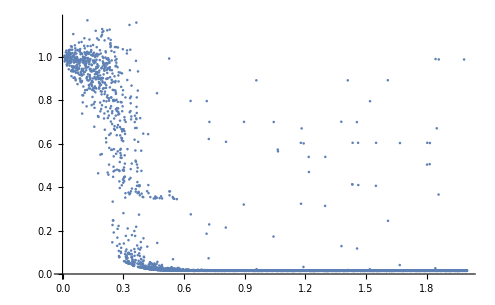

```mathematica
ListPlot[Transpose[{xcyc,ycyc}],PlotRange->All]
```

```mathematica
(*converge it*)
```

```mathematica
midv[vv_]:=Sort[vv][[(Length[vv]+1)/2]];
```

```mathematica
lengthv=3980;sepv=10;
xcycC=Table[0,{i,1,lengthv/sepv}];
ycycC=Table[0,{i,1,lengthv/sepv}];
For[i=1,i≤(lengthv/sepv),i++,
tptx=Table[0,{i,1,sepv+1}];
tpty=Table[0,{i,1,sepv+1}];
For[j=1,j≤sepv+1,j++,
tptx[[j]]=xcyc[[(i-1)*sepv+j]];
tpty[[j]]=ycyc[[(i-1)*sepv+j]];
];
xcycC[[i]]=midv[tptx];
ycycC[[i]]=midv[tpty];
];
```

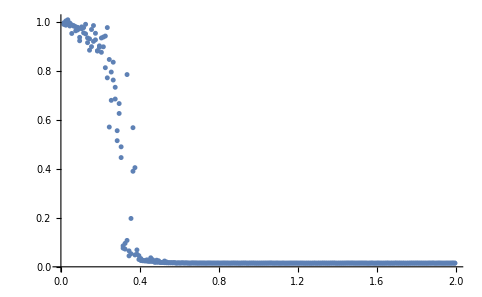

```mathematica
ListPlot[Transpose[{xcycC,ycycC}],PlotRange->All]
```

```mathematica
z6x={0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.06500001,0.066,0.067,0.068,0.06900001,0.07,0.071,0.072,0.07300001,0.074,0.075,0.07600001,0.077,0.078,0.079,0.08000001,0.081,0.082,0.083,0.08400001,0.085,0.086,0.087,0.08800001,0.089,0.09,0.09100001,0.092,0.093,0.094,0.09500001,0.096,0.097,0.098,0.09900001,0.1,0.101,0.102,0.103,0.104,0.105,0.106,0.107,0.108,0.109,0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.121,0.122,0.123,0.124,0.125,0.126,0.127,0.128,0.129,0.13,0.131,0.132,0.133,0.134,0.135,0.136,0.137,0.138,0.139,0.14,0.141,0.142,0.143,0.144,0.145,0.146,0.147,0.148,0.149,0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19,0.191,0.192,0.193,0.194,0.195,0.196,0.197,0.198,0.199,0.2,0.201,0.202,0.203,0.204,0.205,0.206,0.207,0.208,0.209,0.21,0.211,0.212,0.213,0.214,0.215,0.216,0.217,0.218,0.219,0.22,0.221,0.222,0.223,0.224,0.225,0.226,0.227,0.228,0.229,0.23,0.231,0.232,0.233,0.234,0.235,0.236,0.237,0.238,0.239,0.24,0.241,0.242,0.243,0.244,0.245,0.246,0.247,0.248,0.249,0.25,0.251,0.252,0.253,0.254,0.255,0.256,0.257,0.258,0.259,0.26,0.261,0.262,0.263,0.264,0.265,0.266,0.267,0.268,0.269,0.27,0.271,0.272,0.273,0.274,0.275,0.276,0.277,0.278,0.279,0.28,0.281,0.282,0.283,0.284,0.285,0.286,0.287,0.288,0.289,0.29,0.291,0.292,0.293,0.294,0.295,0.296,0.297,0.298,0.299,0.3,0.301,0.302,0.303,0.304,0.305,0.306,0.307,0.308,0.309,0.31,0.311,0.312,0.313,0.314,0.315,0.316,0.317,0.318,0.319,0.32,0.321,0.322,0.323,0.324,0.325,0.326,0.327,0.328,0.329,0.33,0.331,0.332,0.333,0.334,0.335,0.336,0.337,0.338,0.339,0.34,0.341,0.342,0.343,0.344,0.345,0.346,0.347,0.348,0.349,0.35,0.351,0.352,0.353,0.354,0.355,0.356,0.357,0.358,0.359,0.36,0.361,0.362,0.363,0.364,0.365,0.366,0.367,0.368,0.369,0.37,0.371,0.372,0.373,0.374,0.375,0.376,0.377,0.378,0.379,0.38,0.381,0.382,0.383,0.384,0.385,0.386,0.387,0.388,0.389,0.39,0.391,0.392,0.393,0.394,0.395,0.396,0.397,0.398,0.399,0.4,0.401,0.402,0.403,0.404,0.405,0.406,0.407,0.408,0.409,0.41,0.411,0.412,0.413,0.414,0.415,0.416,0.417,0.418,0.419,0.42,0.421,0.422,0.423,0.424,0.425,0.426,0.427,0.428,0.429,0.43,0.431,0.432,0.433,0.434,0.435,0.436,0.437,0.438,0.439,0.44,0.441,0.442,0.443,0.444,0.445,0.446,0.447,0.448,0.449,0.45,0.451,0.452,0.453,0.454,0.455,0.456,0.457,0.458,0.459,0.46,0.461,0.462,0.463,0.464,0.465,0.466,0.467,0.468,0.469,0.47,0.471,0.472,0.473,0.474,0.475,0.476,0.477,0.478,0.479,0.48,0.481,0.482,0.483,0.484,0.485,0.486,0.487,0.488,0.489,0.49,0.491,0.492,0.493,0.494,0.495,0.496,0.497,0.498,0.499,0.5,0.501,0.502,0.503,0.504,0.505,0.506,0.507,0.508,0.509,0.5100001,0.511,0.512,0.513,0.514,0.515,0.516,0.517,0.518,0.5190001,0.52,0.521,0.522,0.523,0.524,0.525,0.526,0.527,0.528,0.529,0.53,0.531,0.532,0.5330001,0.534,0.535,0.536,0.537,0.538,0.539,0.54,0.541,0.542,0.543,0.544,0.545,0.546,0.5470001,0.548,0.549,0.55,0.551,0.552,0.553,0.554,0.555,0.5560001,0.557,0.558,0.559,0.56,0.561,0.562,0.563,0.564,0.565,0.566,0.567,0.568,0.569,0.5700001,0.571,0.572,0.573,0.574,0.575,0.576,0.577,0.578,0.5790001,0.58,0.581,0.582,0.583,0.5840001,0.585,0.586,0.587,0.588,0.589,0.59,0.591,0.592,0.5930001,0.594,0.595,0.596,0.597,0.598,0.599,0.6,0.601,0.602,0.603,0.604,0.605,0.606,0.6070001,0.608,0.609,0.61,0.611,0.612,0.613,0.614,0.615,0.6160001,0.617,0.618,0.619,0.62,0.6210001,0.622,0.623,0.624,0.625,0.626,0.627,0.628,0.629,0.6300001,0.631,0.632,0.633,0.634,0.6350001,0.636,0.637,0.638,0.6390001,0.64,0.641,0.642,0.643,0.6440001,0.645,0.646,0.647,0.648,0.649,0.65,0.651,0.652,0.6530001,0.654,0.655,0.656,0.657,0.6580001,0.659,0.66,0.661,0.6620001,0.663,0.664,0.665,0.666,0.6670001,0.668,0.669,0.67,0.671,0.6720001,0.673,0.674,0.675,0.6760001,0.677,0.678,0.679,0.68,0.6810001,0.682,0.683,0.684,0.685,0.686,0.687,0.688,0.689,0.6900001,0.691,0.692,0.693,0.694,0.6950001,0.696,0.697,0.698,0.6990001,0.7,0.701,0.702,0.703,0.7040001,0.705,0.706,0.707,0.708,0.7090001,0.71,0.711,0.712,0.7130001,0.714,0.715,0.716,0.717,0.7180001,0.719,0.72,0.721,0.7220001,0.723,0.724,0.725,0.726,0.7270001,0.728,0.729,0.73,0.731,0.7320001,0.733,0.734,0.735,0.7360001,0.737,0.738,0.739,0.74,0.7410001,0.742,0.743,0.744,0.7450001,0.7460001,0.747,0.748,0.749,0.7500001,0.751,0.752,0.753,0.754,0.7550001,0.756,0.757,0.758,0.7590001,0.7600001,0.761,0.762,0.763,0.7640001,0.765,0.766,0.767,0.768,0.7690001,0.77,0.771,0.772,0.7730001,0.774,0.775,0.776,0.777,0.7780001,0.779,0.78,0.781,0.7820001,0.7830001,0.784,0.785,0.786,0.7870001,0.788,0.789,0.79,0.791,0.7920001,0.793,0.794,0.795,0.7960001,0.7970001,0.798,0.799,0.8,0.8010001,0.802,0.803,0.804,0.8050001,0.8060001,0.807,0.808,0.809,0.8100001,0.811,0.812,0.813,0.814,0.8150001,0.816,0.817,0.818,0.8190001,0.8200001,0.821,0.822,0.823,0.8240001,0.825,0.826,0.827,0.828,0.8290001,0.83,0.831,0.832,0.8330001,0.8340001,0.835,0.836,0.837,0.8380001,0.839,0.84,0.841,0.8420001,0.8430001,0.844,0.845,0.846,0.8470001,0.848,0.849,0.85,0.851,0.8520001,0.853,0.854,0.855,0.8560001,0.8570001,0.858,0.859,0.86,0.8610001,0.862,0.863,0.864,0.8650001,0.8660001,0.867,0.868,0.869,0.8700001,0.8710001,0.872,0.873,0.874,0.8750001,0.876,0.877,0.878,0.8790001,0.8800001,0.881,0.882,0.883,0.8840001,0.8850001,0.886,0.887,0.8880001,0.8890001,0.89,0.891,0.892,0.8930001,0.8940001,0.895,0.896,0.897,0.8980001,0.899,0.9,0.901,0.9020001,0.9030001,0.904,0.905,0.906,0.9070001,0.9080001,0.909,0.91,0.911,0.9120001,0.913,0.914,0.915,0.9160001,0.9170001,0.918,0.919,0.92,0.9210001,0.9220001,0.923,0.924,0.9250001,0.9260001,0.927,0.928,0.929,0.9300001,0.9310001,0.932,0.933,0.934,0.9350001,0.936,0.937,0.938,0.9390001,0.9400001,0.941,0.942,0.943,0.9440001,0.9450001,0.946,0.947,0.9480001,0.9490001,0.95,0.951,0.952,0.9530001,0.9540001,0.955,0.956,0.957,0.9580001,0.9590001,0.96,0.961,0.9620001,0.9630001,0.964,0.965,0.966,0.9670001,0.9680001,0.969,0.97,0.971,0.9720001,0.973,0.974,0.975,0.9760001,0.9770001,0.978,0.979,0.98,0.9810001,0.9820001,0.983,0.984,0.9850001,0.9860001,0.987,0.988,0.989,0.9900001,0.9910001,0.992,0.993,0.994,0.9950001,0.9960001,0.997,0.998,0.9990001,1,1.001,1.002,1.003,1.004,1.005,1.006,1.007,1.008,1.009,1.01,1.011,1.012,1.013,1.014,1.015,1.016,1.017,1.018,1.019,1.02,1.021,1.022,1.023,1.024,1.025,1.026,1.027,1.028,1.029,1.03,1.031,1.032,1.033,1.034,1.035,1.036,1.037,1.038,1.039,1.04,1.041,1.042,1.043,1.044,1.045,1.046,1.047,1.048,1.049,1.05,1.051,1.052,1.053,1.054,1.055,1.056,1.057,1.058,1.059,1.06,1.061,1.062,1.063,1.064,1.065,1.066,1.067,1.068,1.069,1.07,1.071,1.072,1.073,1.074,1.075,1.076,1.077,1.078,1.079,1.08,1.081,1.082,1.083,1.084,1.085,1.086,1.087,1.088,1.089,1.09,1.091,1.092,1.093,1.094,1.095,1.096,1.097,1.098,1.099,1.1,1.101,1.102,1.103,1.104,1.105,1.106,1.107,1.108,1.109,1.11,1.111,1.112,1.113,1.114,1.115,1.116,1.117,1.118,1.119,1.12,1.121,1.122,1.123,1.124,1.125,1.126,1.127,1.128,1.129,1.13,1.131,1.132,1.133,1.134,1.135,1.136,1.137,1.138,1.139,1.14,1.141,1.142,1.143,1.144,1.145,1.146,1.147,1.148,1.149,1.15,1.151,1.152,1.153,1.154,1.155,1.156,1.157,1.158,1.159,1.16,1.161,1.162,1.163,1.164,1.165,1.166,1.167,1.168,1.169,1.17,1.171,1.172,1.173,1.174,1.175,1.176,1.177,1.178,1.179,1.18,1.181,1.182,1.183,1.184,1.185,1.186,1.187,1.188,1.189,1.19,1.191,1.192,1.193,1.194,1.195,1.196,1.197,1.198,1.199,1.2,1.201,1.202,1.203,1.204,1.205,1.206,1.207,1.208,1.209,1.21,1.211,1.212,1.213,1.214,1.215,1.216,1.217,1.218,1.219,1.22,1.221,1.222,1.223,1.224,1.225,1.226,1.227,1.228,1.229,1.23,1.231,1.232,1.233,1.234,1.235,1.236,1.237,1.238,1.239,1.24,1.241,1.242,1.243,1.244,1.245,1.246,1.247,1.248,1.249,1.25,1.251,1.252,1.253,1.254,1.255,1.256,1.257,1.258,1.259,1.26,1.261,1.262,1.263,1.264,1.265,1.266,1.267,1.268,1.269,1.27,1.271,1.272,1.273,1.274,1.275,1.276,1.277,1.278,1.279,1.28,1.281,1.282,1.283,1.284,1.285,1.286,1.287,1.288,1.289,1.29,1.291,1.292,1.293,1.294,1.295,1.296,1.297,1.298,1.299,1.3,1.301,1.302,1.303,1.304,1.305,1.306,1.307,1.308,1.309,1.31,1.311,1.312,1.313,1.314,1.315,1.316,1.317,1.318,1.319,1.32,1.321,1.322,1.323,1.324,1.325,1.326,1.327,1.328,1.329,1.33,1.331,1.332,1.333,1.334,1.335,1.336,1.337,1.338,1.339,1.34,1.341,1.342,1.343,1.344,1.345,1.346,1.347,1.348,1.349,1.35,1.351,1.352,1.353,1.354,1.355,1.356,1.357,1.358,1.359,1.36,1.361,1.362,1.363,1.364,1.365,1.366,1.367,1.368,1.369,1.37,1.371,1.372,1.373,1.374,1.375,1.376,1.377,1.378,1.379,1.38,1.381,1.382,1.383,1.384,1.385,1.386,1.387,1.388,1.389,1.39,1.391,1.392,1.393,1.394,1.395,1.396,1.397,1.398,1.399,1.4,1.401,1.402,1.403,1.404,1.405,1.406,1.407,1.408,1.409,1.41,1.411,1.412,1.413,1.414,1.415,1.416,1.417,1.418,1.419,1.42,1.421,1.422,1.423,1.424,1.425,1.426,1.427,1.428,1.429,1.43,1.431,1.432,1.433,1.434,1.435,1.436,1.437,1.438,1.439,1.44,1.441,1.442,1.443,1.444,1.445,1.446,1.447,1.448,1.449,1.45,1.451,1.452,1.453,1.454,1.455,1.456,1.457,1.458,1.459,1.46,1.461,1.462,1.463,1.464,1.465,1.466,1.467,1.468,1.469,1.47,1.471,1.472,1.473,1.474,1.475,1.476,1.477,1.478,1.479,1.48,1.481,1.482,1.483,1.484,1.485,1.486,1.487,1.488,1.489,1.49,1.491,1.492,1.493,1.494,1.495,1.496,1.497,1.498,1.499,1.5,1.501,1.502,1.503,1.504,1.505,1.506,1.507,1.508,1.509,1.51,1.511,1.512,1.513,1.514,1.515,1.516,1.517,1.518,1.519,1.52,1.521,1.522,1.523,1.524,1.525,1.526,1.527,1.528,1.529,1.53,1.531,1.532,1.533,1.534,1.535,1.536,1.537,1.538,1.539,1.54,1.541,1.542,1.543,1.544,1.545,1.546,1.547,1.548,1.549,1.55,1.551,1.552,1.553,1.554,1.555,1.556,1.557,1.558,1.559,1.56,1.561,1.562,1.563,1.564,1.565,1.566,1.567,1.568,1.569,1.57,1.571,1.572,1.573,1.574,1.575,1.576,1.577,1.578,1.579,1.58,1.581,1.582,1.583,1.584,1.585,1.586,1.587,1.588,1.589,1.59,1.591,1.592,1.593,1.594,1.595,1.596,1.597,1.598,1.599,1.6,1.601,1.602,1.603,1.604,1.605,1.606,1.607,1.608,1.609,1.61,1.611,1.612,1.613,1.614,1.615,1.616,1.617,1.618,1.619,1.62,1.621,1.622,1.623,1.624,1.625,1.626,1.627,1.628,1.629,1.63,1.631,1.632,1.633,1.634,1.635,1.636,1.637,1.638,1.639,1.64,1.641,1.642,1.643,1.644,1.645,1.646,1.647,1.648,1.649,1.65,1.651,1.652,1.653,1.654,1.655,1.656,1.657,1.658,1.659,1.66,1.661,1.662,1.663,1.664,1.665,1.666,1.667,1.668,1.669,1.67,1.671,1.672,1.673,1.674,1.675,1.676,1.677,1.678,1.679,1.68,1.681,1.682,1.683,1.684,1.685,1.686,1.687,1.688,1.689,1.69,1.691,1.692,1.693,1.694,1.695,1.696,1.697,1.698,1.699,1.7,1.701,1.702,1.703,1.704,1.705,1.706,1.707,1.708,1.709,1.71,1.711,1.712,1.713,1.714,1.715,1.716,1.717,1.718,1.719,1.72,1.721,1.722,1.723,1.724,1.725,1.726,1.727,1.728,1.729,1.73,1.731,1.732,1.733,1.734,1.735,1.736,1.737,1.738,1.739,1.74,1.741,1.742,1.743,1.744,1.745,1.746,1.747,1.748,1.749,1.75,1.751,1.752,1.753,1.754,1.755,1.756,1.757,1.758,1.759,1.76,1.761,1.762,1.763,1.764,1.765,1.766,1.767,1.768,1.769,1.77,1.771,1.772,1.773,1.774,1.775,1.776,1.777,1.778,1.779,1.78,1.781,1.782,1.783,1.784,1.785,1.786,1.787,1.788,1.789,1.79,1.791,1.792,1.793,1.794,1.795,1.796,1.797,1.798,1.799,1.8,1.801,1.802,1.803,1.804,1.805,1.806,1.807,1.808,1.809,1.81,1.811,1.812,1.813,1.814,1.815,1.816,1.817,1.818,1.819,1.82,1.821,1.822,1.823,1.824,1.825,1.826,1.827,1.828,1.829,1.83,1.831,1.832,1.833,1.834,1.835,1.836,1.837,1.838,1.839,1.84,1.841,1.842,1.843,1.844,1.845,1.846,1.847,1.848,1.849,1.85,1.851,1.852,1.853,1.854,1.855,1.856,1.857,1.858,1.859,1.86,1.861,1.862,1.863,1.864,1.865,1.866,1.867,1.868,1.869,1.87,1.871,1.872,1.873,1.874,1.875,1.876,1.877,1.878,1.879,1.88,1.881,1.882,1.883,1.884,1.885,1.886,1.887,1.888,1.889,1.89,1.891,1.892,1.893,1.894,1.895,1.896,1.897,1.898,1.899,1.9,1.901,1.902,1.903,1.904,1.905,1.906,1.907,1.908,1.909,1.91,1.911,1.912,1.913,1.914,1.915,1.916,1.917,1.918,1.919,1.92,1.921,1.922,1.923,1.924,1.925,1.926,1.927,1.928,1.929,1.93,1.931,1.932,1.933,1.934,1.935,1.936,1.937,1.938,1.939,1.94,1.941,1.942,1.943,1.944,1.945,1.946,1.947,1.948,1.949,1.95,1.951,1.952,1.953,1.954,1.955,1.956,1.957,1.958,1.959,1.96,1.961,1.962,1.963,1.964,1.965,1.966,1.967,1.968,1.969,1.97,1.971,1.972,1.973,1.974,1.975,1.976,1.977,1.978,1.979,1.98,1.981,1.982,1.983,1.984,1.985,1.986,1.987,1.988,1.989,1.99,1.991,1.992,1.993,1.994,1.995,1.996,1.997,1.998,1.999,2,2.001,2.002,2.003,2.004,2.005,2.006,2.007,2.008,2.009,2.01,2.011,2.012,2.013,2.014,2.015,2.016,2.017,2.018,2.019,2.02,2.021,2.022,2.023,2.024,2.025,2.026,2.027,2.028,2.029,2.03,2.031,2.032,2.033,2.034,2.035,2.036,2.037,2.038,2.039,2.04,2.041,2.042,2.043,2.044,2.045,2.046,2.047,2.048,2.049,2.05,2.051,2.052,2.053,2.054,2.055,2.056,2.057,2.058,2.059,2.06,2.061,2.062,2.063,2.064,2.065,2.066,2.067,2.068,2.069,2.07,2.071,2.072,2.073,2.074,2.075,2.076,2.077,2.078,2.079,2.08,2.081,2.082,2.083,2.084,2.085,2.086,2.087,2.088,2.089,2.09,2.091,2.092,2.093,2.094,2.095,2.096,2.097,2.098,2.099,2.1,2.101,2.102,2.103,2.104,2.105,2.106,2.107,2.108,2.109,2.11,2.111,2.112,2.113,2.114,2.115,2.116,2.117,2.118,2.119,2.12,2.121,2.122,2.123,2.124,2.125,2.126,2.127,2.128,2.129,2.13,2.131,2.132,2.133,2.134,2.135,2.136,2.137,2.138,2.139,2.14,2.141,2.142,2.143,2.144,2.145,2.146,2.147,2.148,2.149,2.15,2.151,2.152,2.153,2.154,2.155,2.156,2.157,2.158,2.159,2.16,2.161,2.162,2.163,2.164,2.165,2.166,2.167,2.168,2.169,2.17,2.171,2.172,2.173,2.174,2.175,2.176,2.177,2.178,2.179,2.18,2.181,2.182,2.183,2.184,2.185,2.186,2.187,2.188,2.189,2.19,2.191,2.192,2.193,2.194,2.195,2.196,2.197,2.198,2.199,2.2,2.201,2.202,2.203,2.204,2.205,2.206,2.207,2.208,2.209,2.21,2.211,2.212,2.213,2.214,2.215,2.216,2.217,2.218,2.219,2.22,2.221,2.222,2.223,2.224,2.225,2.226,2.227,2.228,2.229,2.23,2.231,2.232,2.233,2.234,2.235,2.236,2.237,2.238,2.239,2.24,2.241,2.242,2.243,2.244,2.245,2.246,2.247,2.248,2.249,2.25,2.251,2.252,2.253,2.254,2.255,2.256,2.257,2.258,2.259,2.26,2.261,2.262,2.263,2.264,2.265,2.266,2.267,2.268,2.269,2.27,2.271,2.272,2.273,2.274,2.275,2.276,2.277,2.278,2.279,2.28,2.281,2.282,2.283,2.284,2.285,2.286,2.287,2.288,2.289,2.29,2.291,2.292,2.293,2.294,2.295,2.296,2.297,2.298,2.299,2.3,2.301,2.302,2.303,2.304,2.305,2.306,2.307,2.308,2.309,2.31,2.311,2.312,2.313,2.314,2.315,2.316,2.317,2.318,2.319,2.32,2.321,2.322,2.323,2.324,2.325,2.326,2.327,2.328,2.329,2.33,2.331,2.332,2.333,2.334,2.335,2.336,2.337,2.338,2.339,2.34,2.341,2.342,2.343,2.344,2.345,2.346,2.347,2.348,2.349,2.35,2.351,2.352,2.353,2.354,2.355,2.356,2.357,2.358,2.359,2.36,2.361,2.362,2.363,2.364,2.365,2.366,2.367,2.368,2.369,2.37,2.371,2.372,2.373,2.374,2.375,2.376,2.377,2.378,2.379,2.38,2.381,2.382,2.383,2.384,2.385,2.386,2.387,2.388,2.389,2.39,2.391,2.392,2.393,2.394,2.395,2.396,2.397,2.398,2.399,2.4,2.401,2.402,2.403,2.404,2.405,2.406,2.407,2.408,2.409,2.41,2.411,2.412,2.413,2.414,2.415,2.416,2.417,2.418,2.419,2.42,2.421,2.422,2.423,2.424,2.425,2.426,2.427,2.428,2.429,2.43,2.431,2.432,2.433,2.434,2.435,2.436,2.437,2.438,2.439,2.44,2.441,2.442,2.443,2.444,2.445,2.446,2.447,2.448,2.449,2.45,2.451,2.452,2.453,2.454,2.455,2.456,2.457,2.458,2.459,2.46,2.461,2.462,2.463,2.464,2.465,2.466,2.467,2.468,2.469,2.47,2.471,2.472,2.473,2.474,2.475,2.476,2.477,2.478,2.479,2.48,2.481,2.482,2.483,2.484,2.485,2.486,2.487,2.488,2.489,2.49,2.491,2.492,2.493,2.494,2.495,2.496,2.497,2.498,2.499,2.5,2.501,2.502,2.503,2.504,2.505,2.506,2.507,2.508,2.509,2.51,2.511,2.512,2.513,2.514,2.515,2.516,2.517,2.518,2.519,2.52,2.521,2.522,2.523,2.524,2.525,2.526,2.527,2.528,2.529,2.53,2.531,2.532,2.533,2.534,2.535,2.536,2.537,2.538,2.539,2.54,2.541,2.542,2.543,2.544,2.545,2.546,2.547,2.548,2.549,2.55,2.551,2.552,2.553,2.554,2.555,2.556,2.557,2.558,2.559,2.56,2.561,2.562,2.563,2.564,2.565,2.566,2.567,2.568,2.569,2.57,2.571,2.572,2.573,2.574,2.575,2.576,2.577,2.578,2.579,2.58,2.581,2.582,2.583,2.584,2.585,2.586,2.587,2.588,2.589,2.59,2.591,2.592,2.593,2.594,2.595,2.596,2.597,2.598,2.599,2.6,2.601,2.602,2.603,2.604,2.605,2.606,2.607,2.608,2.609,2.61,2.611,2.612,2.613,2.614,2.615,2.616,2.617,2.618,2.619,2.62,2.621,2.622,2.623,2.624,2.625,2.626,2.627,2.628,2.629,2.63,2.631,2.632,2.633,2.634,2.635,2.636,2.637,2.638,2.639,2.64,2.641,2.642,2.643,2.644,2.645,2.646,2.647,2.648,2.649,2.65,2.651,2.652,2.653,2.654,2.655,2.656,2.657,2.658,2.659,2.66,2.661,2.662,2.663,2.664,2.665,2.666,2.667,2.668,2.669,2.67,2.671,2.672,2.673,2.674,2.675,2.676,2.677,2.678,2.679,2.68,2.681,2.682,2.683,2.684,2.685,2.686,2.687,2.688,2.689,2.69,2.691,2.692,2.693,2.694,2.695,2.696,2.697,2.698,2.699,2.7,2.701,2.702,2.703,2.704,2.705,2.706,2.707,2.708,2.709,2.71,2.711,2.712,2.713,2.714,2.715,2.716,2.717,2.718,2.719,2.72,2.721,2.722,2.723,2.724,2.725,2.726,2.727,2.728,2.729,2.73,2.731,2.732,2.733,2.734,2.735,2.736,2.737,2.738,2.739,2.74,2.741,2.742,2.743,2.744,2.745,2.746,2.747,2.748,2.749,2.75,2.751,2.752,2.753,2.754,2.755,2.756,2.757,2.758,2.759,2.76,2.761,2.762,2.763,2.764,2.765,2.766,2.767,2.768,2.769,2.77,2.771,2.772,2.773,2.774,2.775,2.776,2.777,2.778,2.779,2.78,2.781,2.782,2.783,2.784,2.785,2.786,2.787,2.788,2.789,2.79,2.791,2.792,2.793,2.794,2.795,2.796,2.797,2.798,2.799,2.8,2.801,2.802,2.803,2.804,2.805,2.806,2.807,2.808,2.809,2.81,2.811,2.812,2.813,2.814,2.815,2.816,2.817,2.818,2.819,2.82,2.821,2.822,2.823,2.824,2.825,2.826,2.827,2.828,2.829,2.83,2.831,2.832,2.833,2.834,2.835,2.836,2.837,2.838,2.839,2.84,2.841,2.842,2.843,2.844,2.845,2.846,2.847,2.848,2.849,2.85,2.851,2.852,2.853,2.854,2.855,2.856,2.857,2.858,2.859,2.86,2.861,2.862,2.863,2.864,2.865,2.866,2.867,2.868,2.869,2.87,2.871,2.872,2.873,2.874,2.875,2.876,2.877,2.878,2.879,2.88,2.881,2.882,2.883,2.884,2.885,2.886,2.887,2.888,2.889,2.89,2.891,2.892,2.893,2.894,2.895,2.896,2.897,2.898,2.899,2.9,2.901,2.902,2.903,2.904,2.905,2.906,2.907,2.908,2.909,2.91,2.911,2.912,2.913,2.914,2.915,2.916,2.917,2.918,2.919,2.92,2.921,2.922,2.923,2.924,2.925,2.926,2.927,2.928,2.929,2.93,2.931,2.932,2.933,2.934,2.935,2.936,2.937,2.938,2.939,2.94,2.941,2.942,2.943,2.944,2.945,2.946,2.947,2.948,2.949,2.95,2.951,2.952,2.953,2.954,2.955,2.956,2.957,2.958,2.959,2.96,2.961,2.962,2.963,2.964,2.965,2.966,2.967,2.968,2.969,2.97,2.971,2.972,2.973,2.974,2.975,2.976,2.977,2.978,2.979,2.98,2.981,2.982,2.983,2.984,2.985,2.986,2.987,2.988,2.989,2.99,2.991,2.992,2.993,2.994,2.995,2.996,2.997,2.998,2.999,3,3.001,3.002,3.003,3.004,3.005,3.006,3.007,3.008,3.009,3.01,3.011,3.012,3.013,3.014,3.015,3.016,3.017,3.018,3.019,3.02,3.021,3.022,3.023,3.024,3.025,3.026,3.027,3.028,3.029,3.03,3.031,3.032,3.033,3.034,3.035,3.036,3.037,3.038,3.039,3.04,3.041,3.042,3.043,3.044,3.045,3.046,3.047,3.048,3.049,3.05,3.051,3.052,3.053,3.054,3.055,3.056,3.057,3.058,3.059,3.06,3.061,3.062,3.063,3.064,3.065,3.066,3.067,3.068,3.069,3.07,3.071,3.072,3.073,3.074,3.075,3.076,3.077,3.078,3.079,3.08,3.081,3.082,3.083,3.084,3.085,3.086,3.087,3.088,3.089,3.09,3.091,3.092,3.093,3.094,3.095,3.096,3.097,3.098,3.099,3.1,3.101,3.102,3.103,3.104,3.105,3.106,3.107,3.108,3.109,3.11,3.111,3.112,3.113,3.114,3.115,3.116,3.117,3.118,3.119,3.12,3.121,3.122,3.123,3.124,3.125,3.126,3.127,3.128,3.129,3.13,3.131,3.132,3.133,3.134,3.135,3.136,3.137,3.138,3.139,3.14,3.141,3.142,3.143,3.144,3.145,3.146,3.147,3.148,3.149,3.15,3.151,3.152,3.153,3.154,3.155,3.156,3.157,3.158,3.159,3.16,3.161,3.162,3.163,3.164,3.165,3.166,3.167,3.168,3.169,3.17,3.171,3.172,3.173,3.174,3.175,3.176,3.177,3.178,3.179,3.18,3.181,3.182,3.183,3.184,3.185,3.186,3.187,3.188,3.189,3.19,3.191,3.192,3.193,3.194,3.195,3.196,3.197,3.198,3.199,3.2,3.201,3.202,3.203,3.204,3.205,3.206,3.207,3.208,3.209,3.21,3.211,3.212,3.213,3.214,3.215,3.216,3.217,3.218,3.219,3.22,3.221,3.222,3.223,3.224,3.225,3.226,3.227,3.228,3.229,3.23,3.231,3.232,3.233,3.234,3.235,3.236,3.237,3.238,3.239,3.24,3.241,3.242,3.243,3.244,3.245,3.246,3.247,3.248,3.249,3.25,3.251,3.252,3.253,3.254,3.255,3.256,3.257,3.258,3.259,3.26,3.261,3.262,3.263,3.264,3.265,3.266,3.267,3.268,3.269,3.27,3.271,3.272,3.273,3.274,3.275,3.276,3.277,3.278,3.279,3.28,3.281,3.282,3.283,3.284,3.285,3.286,3.287,3.288,3.289,3.29,3.291,3.292,3.293,3.294,3.295,3.296,3.297,3.298,3.299,3.3,3.301,3.302,3.303,3.304,3.305,3.306,3.307,3.308,3.309,3.31,3.311,3.312,3.313,3.314,3.315,3.316,3.317,3.318,3.319,3.32,3.321,3.322,3.323,3.324,3.325,3.326,3.327,3.328,3.329,3.33,3.331,3.332,3.333,3.334,3.335,3.336,3.337,3.338,3.339,3.34,3.341,3.342,3.343,3.344,3.345,3.346,3.347,3.348,3.349,3.35,3.351,3.352,3.353,3.354,3.355,3.356,3.357,3.358,3.359,3.36,3.361,3.362,3.363,3.364,3.365,3.366,3.367,3.368,3.369,3.37,3.371,3.372,3.373,3.374,3.375,3.376,3.377,3.378,3.379,3.38,3.381,3.382,3.383,3.384,3.385,3.386,3.387,3.388,3.389,3.39,3.391,3.392,3.393,3.394,3.395,3.396,3.397,3.398,3.399,3.4,3.401,3.402,3.403,3.404,3.405,3.406,3.407,3.408,3.409,3.41,3.411,3.412,3.413,3.414,3.415,3.416,3.417,3.418,3.419,3.42,3.421,3.422,3.423,3.424,3.425,3.426,3.427,3.428,3.429,3.43,3.431,3.432,3.433,3.434,3.435,3.436,3.437,3.438,3.439,3.44,3.441,3.442,3.443,3.444,3.445,3.446,3.447,3.448,3.449,3.45,3.451,3.452,3.453,3.454,3.455,3.456,3.457,3.458,3.459,3.46,3.461,3.462,3.463,3.464,3.465,3.466,3.467,3.468,3.469,3.47,3.471,3.472,3.473,3.474,3.475,3.476,3.477,3.478,3.479,3.48,3.481,3.482,3.483,3.484,3.485,3.486,3.487,3.488,3.489,3.49,3.491,3.492,3.493,3.494,3.495,3.496,3.497,3.498,3.499,3.5,3.499,3.498,3.497,3.496,3.495,3.494,3.493,3.492,3.491,3.49,3.489,3.488,3.487,3.486,3.485,3.484,3.483,3.482,3.481,3.48,3.479,3.478,3.477,3.476,3.475,3.474,3.473,3.472,3.471,3.47,3.469,3.468,3.467,3.466,3.465,3.464,3.463,3.462,3.461,3.46,3.459,3.458,3.457,3.456,3.455,3.454,3.453,3.452,3.451,3.45,3.449,3.448,3.447,3.446,3.445,3.444,3.443,3.442,3.441,3.44,3.439,3.438,3.437,3.436,3.435,3.434,3.433,3.432,3.431,3.43,3.429,3.428,3.427,3.426,3.425,3.424,3.423,3.422,3.421,3.42,3.419,3.418,3.417,3.416,3.415,3.414,3.413,3.412,3.411,3.41,3.409,3.408,3.407,3.406,3.405,3.404,3.403,3.402,3.401,3.4,3.399,3.398,3.397,3.396,3.395,3.394,3.393,3.392,3.391,3.39,3.389,3.388,3.387,3.386,3.385,3.384,3.383,3.382,3.381,3.38,3.379,3.378,3.377,3.376,3.375,3.374,3.373,3.372,3.371,3.37,3.369,3.368,3.367,3.366,3.365,3.364,3.363,3.362,3.361,3.36,3.359,3.358,3.357,3.356,3.355,3.354,3.353,3.352,3.351,3.35,3.349,3.348,3.347,3.346,3.345,3.344,3.343,3.342,3.341,3.34,3.339,3.338,3.337,3.336,3.335,3.334,3.333,3.332,3.331,3.33,3.329,3.328,3.327,3.326,3.325,3.324,3.323,3.322,3.321,3.32,3.319,3.318,3.317,3.316,3.315,3.314,3.313,3.312,3.311,3.31,3.309,3.308,3.307,3.306,3.305,3.304,3.303,3.302,3.301,3.3,3.299,3.298,3.297,3.296,3.295,3.294,3.293,3.292,3.291,3.29,3.289,3.288,3.287,3.286,3.285,3.284,3.283,3.282,3.281,3.28,3.279,3.278,3.277,3.276,3.275,3.274,3.273,3.272,3.271,3.27,3.269,3.268,3.267,3.266,3.265,3.264,3.263,3.262,3.261,3.26,3.259,3.258,3.257,3.256,3.255,3.254,3.253,3.252,3.251,3.25,3.249,3.248,3.247,3.246,3.245,3.244,3.243,3.242,3.241,3.24,3.239,3.238,3.237,3.236,3.235,3.234,3.233,3.232,3.231,3.23,3.229,3.228,3.227,3.226,3.225,3.224,3.223,3.222,3.221,3.22,3.219,3.218,3.217,3.216,3.215,3.214,3.213,3.212,3.211,3.21,3.209,3.208,3.207,3.206,3.205,3.204,3.203,3.202,3.201,3.2,3.199,3.198,3.197,3.196,3.195,3.194,3.193,3.192,3.191,3.19,3.189,3.188,3.187,3.186,3.185,3.184,3.183,3.182,3.181,3.18,3.179,3.178,3.177,3.176,3.175,3.174,3.173,3.172,3.171,3.17,3.169,3.168,3.167,3.166,3.165,3.164,3.163,3.162,3.161,3.16,3.159,3.158,3.157,3.156,3.155,3.154,3.153,3.152,3.151,3.15,3.149,3.148,3.147,3.146,3.145,3.144,3.143,3.142,3.141,3.14,3.139,3.138,3.137,3.136,3.135,3.134,3.133,3.132,3.131,3.13,3.129,3.128,3.127,3.126,3.125,3.124,3.123,3.122,3.121,3.12,3.119,3.118,3.117,3.116,3.115,3.114,3.113,3.112,3.111,3.11,3.109,3.108,3.107,3.106,3.105,3.104,3.103,3.102,3.101,3.1,3.099,3.098,3.097,3.096,3.095,3.094,3.093,3.092,3.091,3.09,3.089,3.088,3.087,3.086,3.085,3.084,3.083,3.082,3.081,3.08,3.079,3.078,3.077,3.076,3.075,3.074,3.073,3.072,3.071,3.07,3.069,3.068,3.067,3.066,3.065,3.064,3.063,3.062,3.061,3.06,3.059,3.058,3.057,3.056,3.055,3.054,3.053,3.052,3.051,3.05,3.049,3.048,3.047,3.046,3.045,3.044,3.043,3.042,3.041,3.04,3.039,3.038,3.037,3.036,3.035,3.034,3.033,3.032,3.031,3.03,3.029,3.028,3.027,3.026,3.025,3.024,3.023,3.022,3.021,3.02,3.019,3.018,3.017,3.016,3.015,3.014,3.013,3.012,3.011,3.01,3.009,3.008,3.007,3.006,3.005,3.004,3.003,3.002,3.001,3,2.999,2.998,2.997,2.996,2.995,2.994,2.993,2.992,2.991,2.99,2.989,2.988,2.987,2.986,2.985,2.984,2.983,2.982,2.981,2.98,2.979,2.978,2.977,2.976,2.975,2.974,2.973,2.972,2.971,2.97,2.969,2.968,2.967,2.966,2.965,2.964,2.963,2.962,2.961,2.96,2.959,2.958,2.957,2.956,2.955,2.954,2.953,2.952,2.951,2.95,2.949,2.948,2.947,2.946,2.945,2.944,2.943,2.942,2.941,2.94,2.939,2.938,2.937,2.936,2.935,2.934,2.933,2.932,2.931,2.93,2.929,2.928,2.927,2.926,2.925,2.924,2.923,2.922,2.921,2.92,2.919,2.918,2.917,2.916,2.915,2.914,2.913,2.912,2.911,2.91,2.909,2.908,2.907,2.906,2.905,2.904,2.903,2.902,2.901,2.9,2.899,2.898,2.897,2.896,2.895,2.894,2.893,2.892,2.891,2.89,2.889,2.888,2.887,2.886,2.885,2.884,2.883,2.882,2.881,2.88,2.879,2.878,2.877,2.876,2.875,2.874,2.873,2.872,2.871,2.87,2.869,2.868,2.867,2.866,2.865,2.864,2.863,2.862,2.861,2.86,2.859,2.858,2.857,2.856,2.855,2.854,2.853,2.852,2.851,2.85,2.849,2.848,2.847,2.846,2.845,2.844,2.843,2.842,2.841,2.84,2.839,2.838,2.837,2.836,2.835,2.834,2.833,2.832,2.831,2.83,2.829,2.828,2.827,2.826,2.825,2.824,2.823,2.822,2.821,2.82,2.819,2.818,2.817,2.816,2.815,2.814,2.813,2.812,2.811,2.81,2.809,2.808,2.807,2.806,2.805,2.804,2.803,2.802,2.801,2.8,2.799,2.798,2.797,2.796,2.795,2.794,2.793,2.792,2.791,2.79,2.789,2.788,2.787,2.786,2.785,2.784,2.783,2.782,2.781,2.78,2.779,2.778,2.777,2.776,2.775,2.774,2.773,2.772,2.771,2.77,2.769,2.768,2.767,2.766,2.765,2.764,2.763,2.762,2.761,2.76,2.759,2.758,2.757,2.756,2.755,2.754,2.753,2.752,2.751,2.75,2.749,2.748,2.747,2.746,2.745,2.744,2.743,2.742,2.741,2.74,2.739,2.738,2.737,2.736,2.735,2.734,2.733,2.732,2.731,2.73,2.729,2.728,2.727,2.726,2.725,2.724,2.723,2.722,2.721,2.72,2.719,2.718,2.717,2.716,2.715,2.714,2.713,2.712,2.711,2.71,2.709,2.708,2.707,2.706,2.705,2.704,2.703,2.702,2.701,2.7,2.699,2.698,2.697,2.696,2.695,2.694,2.693,2.692,2.691,2.69,2.689,2.688,2.687,2.686,2.685,2.684,2.683,2.682,2.681,2.68,2.679,2.678,2.677,2.676,2.675,2.674,2.673,2.672,2.671,2.67,2.669,2.668,2.667,2.666,2.665,2.664,2.663,2.662,2.661,2.66,2.659,2.658,2.657,2.656,2.655,2.654,2.653,2.652,2.651,2.65,2.649,2.648,2.647,2.646,2.645,2.644,2.643,2.642,2.641,2.64,2.639,2.638,2.637,2.636,2.635,2.634,2.633,2.632,2.631,2.63,2.629,2.628,2.627,2.626,2.625,2.624,2.623,2.622,2.621,2.62,2.619,2.618,2.617,2.616,2.615,2.614,2.613,2.612,2.611,2.61,2.609,2.608,2.607,2.606,2.605,2.604,2.603,2.602,2.601,2.6,2.599,2.598,2.597,2.596,2.595,2.594,2.593,2.592,2.591,2.59,2.589,2.588,2.587,2.586,2.585,2.584,2.583,2.582,2.581,2.58,2.579,2.578,2.577,2.576,2.575,2.574,2.573,2.572,2.571,2.57,2.569,2.568,2.567,2.566,2.565,2.564,2.563,2.562,2.561,2.56,2.559,2.558,2.557,2.556,2.555,2.554,2.553,2.552,2.551,2.55,2.549,2.548,2.547,2.546,2.545,2.544,2.543,2.542,2.541,2.54,2.539,2.538,2.537,2.536,2.535,2.534,2.533,2.532,2.531,2.53,2.529,2.528,2.527,2.526,2.525,2.524,2.523,2.522,2.521,2.52,2.519,2.518,2.517,2.516,2.515,2.514,2.513,2.512,2.511,2.51,2.509,2.508,2.507,2.506,2.505,2.504,2.503,2.502,2.501,2.5,2.499,2.498,2.497,2.496,2.495,2.494,2.493,2.492,2.491,2.49,2.489,2.488,2.487,2.486,2.485,2.484,2.483,2.482,2.481,2.48,2.479,2.478,2.477,2.476,2.475,2.474,2.473,2.472,2.471,2.47,2.469,2.468,2.467,2.466,2.465,2.464,2.463,2.462,2.461,2.46,2.459,2.458,2.457,2.456,2.455,2.454,2.453,2.452,2.451,2.45,2.449,2.448,2.447,2.446,2.445,2.444,2.443,2.442,2.441,2.44,2.439,2.438,2.437,2.436,2.435,2.434,2.433,2.432,2.431,2.43,2.429,2.428,2.427,2.426,2.425,2.424,2.423,2.422,2.421,2.42,2.419,2.418,2.417,2.416,2.415,2.414,2.413,2.412,2.411,2.41,2.409,2.408,2.407,2.406,2.405,2.404,2.403,2.402,2.401,2.4,2.399,2.398,2.397,2.396,2.395,2.394,2.393,2.392,2.391,2.39,2.389,2.388,2.387,2.386,2.385,2.384,2.383,2.382,2.381,2.38,2.379,2.378,2.377,2.376,2.375,2.374,2.373,2.372,2.371,2.37,2.369,2.368,2.367,2.366,2.365,2.364,2.363,2.362,2.361,2.36,2.359,2.358,2.357,2.356,2.355,2.354,2.353,2.352,2.351,2.35,2.349,2.348,2.347,2.346,2.345,2.344,2.343,2.342,2.341,2.34,2.339,2.338,2.337,2.336,2.335,2.334,2.333,2.332,2.331,2.33,2.329,2.328,2.327,2.326,2.325,2.324,2.323,2.322,2.321,2.32,2.319,2.318,2.317,2.316,2.315,2.314,2.313,2.312,2.311,2.31,2.309,2.308,2.307,2.306,2.305,2.304,2.303,2.302,2.301,2.3,2.299,2.298,2.297,2.296,2.295,2.294,2.293,2.292,2.291,2.29,2.289,2.288,2.287,2.286,2.285,2.284,2.283,2.282,2.281,2.28,2.279,2.278,2.277,2.276,2.275,2.274,2.273,2.272,2.271,2.27,2.269,2.268,2.267,2.266,2.265,2.264,2.263,2.262,2.261,2.26,2.259,2.258,2.257,2.256,2.255,2.254,2.253,2.252,2.251,2.25,2.249,2.248,2.247,2.246,2.245,2.244,2.243,2.242,2.241,2.24,2.239,2.238,2.237,2.236,2.235,2.234,2.233,2.232,2.231,2.23,2.229,2.228,2.227,2.226,2.225,2.224,2.223,2.222,2.221,2.22,2.219,2.218,2.217,2.216,2.215,2.214,2.213,2.212,2.211,2.21,2.209,2.208,2.207,2.206,2.205,2.204,2.203,2.202,2.201,2.2,2.199,2.198,2.197,2.196,2.195,2.194,2.193,2.192,2.191,2.19,2.189,2.188,2.187,2.186,2.185,2.184,2.183,2.182,2.181,2.18,2.179,2.178,2.177,2.176,2.175,2.174,2.173,2.172,2.171,2.17,2.169,2.168,2.167,2.166,2.165,2.164,2.163,2.162,2.161,2.16,2.159,2.158,2.157,2.156,2.155,2.154,2.153,2.152,2.151,2.15,2.149,2.148,2.147,2.146,2.145,2.144,2.143,2.142,2.141,2.14,2.139,2.138,2.137,2.136,2.135,2.134,2.133,2.132,2.131,2.13,2.129,2.128,2.127,2.126,2.125,2.124,2.123,2.122,2.121,2.12,2.119,2.118,2.117,2.116,2.115,2.114,2.113,2.112,2.111,2.11,2.109,2.108,2.107,2.106,2.105,2.104,2.103,2.102,2.101,2.1,2.099,2.098,2.097,2.096,2.095,2.094,2.093,2.092,2.091,2.09,2.089,2.088,2.087,2.086,2.085,2.084,2.083,2.082,2.081,2.08,2.079,2.078,2.077,2.076,2.075,2.074,2.073,2.072,2.071,2.07,2.069,2.068,2.067,2.066,2.065,2.064,2.063,2.062,2.061,2.06,2.059,2.058,2.057,2.056,2.055,2.054,2.053,2.052,2.051,2.05,2.049,2.048,2.047,2.046,2.045,2.044,2.043,2.042,2.041,2.04,2.039,2.038,2.037,2.036,2.035,2.034,2.033,2.032,2.031,2.03,2.029,2.028,2.027,2.026,2.025,2.024,2.023,2.022,2.021,2.02,2.019,2.018,2.017,2.016,2.015,2.014,2.013,2.012,2.011,2.01,2.009,2.008,2.007,2.006,2.005,2.004,2.003,2.002,2.001,2,1.999,1.998,1.997,1.996,1.995,1.994,1.993,1.992,1.991,1.99,1.989,1.988,1.987,1.986,1.985,1.984,1.983,1.982,1.981,1.98,1.979,1.978,1.977,1.976,1.975,1.974,1.973,1.972,1.971,1.97,1.969,1.968,1.967,1.966,1.965,1.964,1.963,1.962,1.961,1.96,1.959,1.958,1.957,1.956,1.955,1.954,1.953,1.952,1.951,1.95,1.949,1.948,1.947,1.946,1.945,1.944,1.943,1.942,1.941,1.94,1.939,1.938,1.937,1.936,1.935,1.934,1.933,1.932,1.931,1.93,1.929,1.928,1.927,1.926,1.925,1.924,1.923,1.922,1.921,1.92,1.919,1.918,1.917,1.916,1.915,1.914,1.913,1.912,1.911,1.91,1.909,1.908,1.907,1.906,1.905,1.904,1.903,1.902,1.901,1.9,1.899,1.898,1.897,1.896,1.895,1.894,1.893,1.892,1.891,1.89,1.889,1.888,1.887,1.886,1.885,1.884,1.883,1.882,1.881,1.88,1.879,1.878,1.877,1.876,1.875,1.874,1.873,1.872,1.871,1.87,1.869,1.868,1.867,1.866,1.865,1.864,1.863,1.862,1.861,1.86,1.859,1.858,1.857,1.856,1.855,1.854,1.853,1.852,1.851,1.85,1.849,1.848,1.847,1.846,1.845,1.844,1.843,1.842,1.841,1.84,1.839,1.838,1.837,1.836,1.835,1.834,1.833,1.832,1.831,1.83,1.829,1.828,1.827,1.826,1.825,1.824,1.823,1.822,1.821,1.82,1.819,1.818,1.817,1.816,1.815,1.814,1.813,1.812,1.811,1.81,1.809,1.808,1.807,1.806,1.805,1.804,1.803,1.802,1.801,1.8,1.799,1.798,1.797,1.796,1.795,1.794,1.793,1.792,1.791,1.79,1.789,1.788,1.787,1.786,1.785,1.784,1.783,1.782,1.781,1.78,1.779,1.778,1.777,1.776,1.775,1.774,1.773,1.772,1.771,1.77,1.769,1.768,1.767,1.766,1.765,1.764,1.763,1.762,1.761,1.76,1.759,1.758,1.757,1.756,1.755,1.754,1.753,1.752,1.751,1.75,1.749,1.748,1.747,1.746,1.745,1.744,1.743,1.742,1.741,1.74,1.739,1.738,1.737,1.736,1.735,1.734,1.733,1.732,1.731,1.73,1.729,1.728,1.727,1.726,1.725,1.724,1.723,1.722,1.721,1.72,1.719,1.718,1.717,1.716,1.715,1.714,1.713,1.712,1.711,1.71,1.709,1.708,1.707,1.706,1.705,1.704,1.703,1.702,1.701,1.7,1.699,1.698,1.697,1.696,1.695,1.694,1.693,1.692,1.691,1.69,1.689,1.688,1.687,1.686,1.685,1.684,1.683,1.682,1.681,1.68,1.679,1.678,1.677,1.676,1.675,1.674,1.673,1.672,1.671,1.67,1.669,1.668,1.667,1.666,1.665,1.664,1.663,1.662,1.661,1.66,1.659,1.658,1.657,1.656,1.655,1.654,1.653,1.652,1.651,1.65,1.649,1.648,1.647,1.646,1.645,1.644,1.643,1.642,1.641,1.64,1.639,1.638,1.637,1.636,1.635,1.634,1.633,1.632,1.631,1.63,1.629,1.628,1.627,1.626,1.625,1.624,1.623,1.622,1.621,1.62,1.619,1.618,1.617,1.616,1.615,1.614,1.613,1.612,1.611,1.61,1.609,1.608,1.607,1.606,1.605,1.604,1.603,1.602,1.601,1.6,1.599,1.598,1.597,1.596,1.595,1.594,1.593,1.592,1.591,1.59,1.589,1.588,1.587,1.586,1.585,1.584,1.583,1.582,1.581,1.58,1.579,1.578,1.577,1.576,1.575,1.574,1.573,1.572,1.571,1.57,1.569,1.568,1.567,1.566,1.565,1.564,1.563,1.562,1.561,1.56,1.559,1.558,1.557,1.556,1.555,1.554,1.553,1.552,1.551,1.55,1.549,1.548,1.547,1.546,1.545,1.544,1.543,1.542,1.541,1.54,1.539,1.538,1.537,1.536,1.535,1.534,1.533,1.532,1.531,1.53,1.529,1.528,1.527,1.526,1.525,1.524,1.523,1.522,1.521,1.52,1.519,1.518,1.517,1.516,1.515,1.514,1.513,1.512,1.511,1.51,1.509,1.508,1.507,1.506,1.505,1.504,1.503,1.502,1.501,1.5,1.499,1.498,1.497,1.496,1.495,1.494,1.493,1.492,1.491,1.49,1.489,1.488,1.487,1.486,1.485,1.484,1.483,1.482,1.481,1.48,1.479,1.478,1.477,1.476,1.475,1.474,1.473,1.472,1.471,1.47,1.469,1.468,1.467,1.466,1.465,1.464,1.463,1.462,1.461,1.46,1.459,1.458,1.457,1.456,1.455,1.454,1.453,1.452,1.451,1.45,1.449,1.448,1.447,1.446,1.445,1.444,1.443,1.442,1.441,1.44,1.439,1.438,1.437,1.436,1.435,1.434,1.433,1.432,1.431,1.43,1.429,1.428,1.427,1.426,1.425,1.424,1.423,1.422,1.421,1.42,1.419,1.418,1.417,1.416,1.415,1.414,1.413,1.412,1.411,1.41,1.409,1.408,1.407,1.406,1.405,1.404,1.403,1.402,1.401,1.4,1.399,1.398,1.397,1.396,1.395,1.394,1.393,1.392,1.391,1.39,1.389,1.388,1.387,1.386,1.385,1.384,1.383,1.382,1.381,1.38,1.379,1.378,1.377,1.376,1.375,1.374,1.373,1.372,1.371,1.37,1.369,1.368,1.367,1.366,1.365,1.364,1.363,1.362,1.361,1.36,1.359,1.358,1.357,1.356,1.355,1.354,1.353,1.352,1.351,1.35,1.349,1.348,1.347,1.346,1.345,1.344,1.343,1.342,1.341,1.34,1.339,1.338,1.337,1.336,1.335,1.334,1.333,1.332,1.331,1.33,1.329,1.328,1.327,1.326,1.325,1.324,1.323,1.322,1.321,1.32,1.319,1.318,1.317,1.316,1.315,1.314,1.313,1.312,1.311,1.31,1.309,1.308,1.307,1.306,1.305,1.304,1.303,1.302,1.301,1.3,1.299,1.298,1.297,1.296,1.295,1.294,1.293,1.292,1.291,1.29,1.289,1.288,1.287,1.286,1.285,1.284,1.283,1.282,1.281,1.28,1.279,1.278,1.277,1.276,1.275,1.274,1.273,1.272,1.271,1.27,1.269,1.268,1.267,1.266,1.265,1.264,1.263,1.262,1.261,1.26,1.259,1.258,1.257,1.256,1.255,1.254,1.253,1.252,1.251,1.25,1.249,1.248,1.247,1.246,1.245,1.244,1.243,1.242,1.241,1.24,1.239,1.238,1.237,1.236,1.235,1.234,1.233,1.232,1.231,1.23,1.229,1.228,1.227,1.226,1.225,1.224,1.223,1.222,1.221,1.22,1.219,1.218,1.217,1.216,1.215,1.214,1.213,1.212,1.211,1.21,1.209,1.208,1.207,1.206,1.205,1.204,1.203,1.202,1.201,1.2,1.199,1.198,1.197,1.196,1.195,1.194,1.193,1.192,1.191,1.19,1.189,1.188,1.187,1.186,1.185,1.184,1.183,1.182,1.181,1.18,1.179,1.178,1.177,1.176,1.175,1.174,1.173,1.172,1.171,1.17,1.169,1.168,1.167,1.166,1.165,1.164,1.163,1.162,1.161,1.16,1.159,1.158,1.157,1.156,1.155,1.154,1.153,1.152,1.151,1.15,1.149,1.148,1.147,1.146,1.145,1.144,1.143,1.142,1.141,1.14,1.139,1.138,1.137,1.136,1.135,1.134,1.133,1.132,1.131,1.13,1.129,1.128,1.127,1.126,1.125,1.124,1.123,1.122,1.121,1.12,1.119,1.118,1.117,1.116,1.115,1.114,1.113,1.112,1.111,1.11,1.109,1.108,1.107,1.106,1.105,1.104,1.103,1.102,1.101,1.1,1.099,1.098,1.097,1.096,1.095,1.094,1.093,1.092,1.091,1.09,1.089,1.088,1.087,1.086,1.085,1.084,1.083,1.082,1.081,1.08,1.079,1.078,1.077,1.076,1.075,1.074,1.073,1.072,1.071,1.07,1.069,1.068,1.067,1.066,1.065,1.064,1.063,1.062,1.061,1.06,1.059,1.058,1.057,1.056,1.055,1.054,1.053,1.052,1.051,1.05,1.049,1.048,1.047,1.046,1.045,1.044,1.043,1.042,1.041,1.04,1.039,1.038,1.037,1.036,1.035,1.034,1.033,1.032,1.031,1.03,1.029,1.028,1.027,1.026,1.025,1.024,1.023,1.022,1.021,1.02,1.019,1.018,1.017,1.016,1.015,1.014,1.013,1.012,1.011,1.01,1.009,1.008,1.007,1.006,1.005,1.004,1.003,1.002,1.001,1,0.9990001,0.998,0.997,0.9960001,0.9950001,0.994,0.993,0.992,0.9910001,0.9900001,0.989,0.988,0.987,0.9860001,0.9850001,0.984,0.983,0.9820001,0.9810001,0.98,0.979,0.978,0.9770001,0.9760001,0.975,0.974,0.973,0.9720001,0.971,0.97,0.969,0.9680001,0.9670001,0.966,0.965,0.964,0.9630001,0.9620001,0.961,0.96,0.9590001,0.9580001,0.957,0.956,0.955,0.9540001,0.9530001,0.952,0.951,0.95,0.9490001,0.9480001,0.947,0.946,0.9450001,0.9440001,0.943,0.942,0.941,0.9400001,0.9390001,0.938,0.937,0.936,0.9350001,0.934,0.933,0.932,0.9310001,0.9300001,0.929,0.928,0.927,0.9260001,0.9250001,0.924,0.923,0.9220001,0.9210001,0.92,0.919,0.918,0.9170001,0.9160001,0.915,0.914,0.913,0.9120001,0.911,0.91,0.909,0.9080001,0.9070001,0.906,0.905,0.904,0.9030001,0.9020001,0.901,0.9,0.899,0.8980001,0.897,0.896,0.895,0.8940001,0.8930001,0.892,0.891,0.89,0.8890001,0.8880001,0.887,0.886,0.8850001,0.8840001,0.883,0.882,0.881,0.8800001,0.8790001,0.878,0.877,0.876,0.8750001,0.874,0.873,0.872,0.8710001,0.8700001,0.869,0.868,0.867,0.8660001,0.8650001,0.864,0.863,0.862,0.8610001,0.86,0.859,0.858,0.8570001,0.8560001,0.855,0.854,0.853,0.8520001,0.851,0.85,0.849,0.848,0.8470001,0.846,0.845,0.844,0.8430001,0.8420001,0.841,0.84,0.839,0.8380001,0.837,0.836,0.835,0.8340001,0.8330001,0.832,0.831,0.83,0.8290001,0.828,0.827,0.826,0.825,0.8240001,0.823,0.822,0.821,0.8200001,0.8190001,0.818,0.817,0.816,0.8150001,0.814,0.813,0.812,0.811,0.8100001,0.809,0.808,0.807,0.8060001,0.8050001,0.804,0.803,0.802,0.8010001,0.8,0.799,0.798,0.7970001,0.7960001,0.795,0.794,0.793,0.7920001,0.791,0.79,0.789,0.788,0.7870001,0.786,0.785,0.784,0.7830001,0.7820001,0.781,0.78,0.779,0.7780001,0.777,0.776,0.775,0.774,0.7730001,0.772,0.771,0.77,0.7690001,0.768,0.767,0.766,0.765,0.7640001,0.763,0.762,0.761,0.7600001,0.7590001,0.758,0.757,0.756,0.7550001,0.754,0.753,0.752,0.751,0.7500001,0.749,0.748,0.747,0.7460001,0.7450001,0.744,0.743,0.742,0.7410001,0.74,0.739,0.738,0.737,0.7360001,0.735,0.734,0.733,0.7320001,0.731,0.73,0.729,0.728,0.7270001,0.726,0.725,0.724,0.723,0.7220001,0.721,0.72,0.719,0.7180001,0.717,0.716,0.715,0.714,0.7130001,0.712,0.711,0.71,0.7090001,0.708,0.707,0.706,0.705,0.7040001,0.703,0.702,0.701,0.7,0.6990001,0.698,0.697,0.696,0.6950001,0.694,0.693,0.692,0.691,0.6900001,0.689,0.688,0.687,0.686,0.685,0.684,0.683,0.682,0.6810001,0.68,0.679,0.678,0.677,0.6760001,0.675,0.674,0.673,0.6720001,0.671,0.67,0.669,0.668,0.6670001,0.666,0.665,0.664,0.663,0.6620001,0.661,0.66,0.659,0.6580001,0.657,0.656,0.655,0.654,0.6530001,0.652,0.651,0.65,0.649,0.648,0.647,0.646,0.645,0.6440001,0.643,0.642,0.641,0.64,0.6390001,0.638,0.637,0.636,0.6350001,0.634,0.633,0.632,0.631,0.6300001,0.629,0.628,0.627,0.626,0.625,0.624,0.623,0.622,0.6210001,0.62,0.619,0.618,0.617,0.6160001,0.615,0.614,0.613,0.612,0.611,0.61,0.609,0.608,0.6070001,0.606,0.605,0.604,0.603,0.602,0.601,0.6,0.599,0.598,0.597,0.596,0.595,0.594,0.5930001,0.592,0.591,0.59,0.589,0.588,0.587,0.586,0.585,0.5840001,0.583,0.582,0.581,0.58,0.5790001,0.578,0.577,0.576,0.575,0.574,0.573,0.572,0.571,0.5700001,0.569,0.568,0.567,0.566,0.565,0.564,0.563,0.562,0.561,0.56,0.559,0.558,0.557,0.5560001,0.555,0.554,0.553,0.552,0.551,0.55,0.549,0.548,0.5470001,0.546,0.545,0.544,0.543,0.542,0.541,0.54,0.539,0.538,0.537,0.536,0.535,0.534,0.5330001,0.532,0.531,0.53,0.529,0.528,0.527,0.526,0.525,0.524,0.523,0.522,0.521,0.52,0.5190001,0.518,0.517,0.516,0.515,0.514,0.513,0.512,0.511,0.5100001,0.509,0.508,0.507,0.506,0.505,0.504,0.503,0.502,0.501,0.5,0.499,0.498,0.497,0.496,0.495,0.494,0.493,0.492,0.491,0.49,0.489,0.488,0.487,0.486,0.485,0.484,0.483,0.482,0.481,0.48,0.479,0.478,0.477,0.476,0.475,0.474,0.473,0.472,0.471,0.47,0.469,0.468,0.467,0.466,0.465,0.464,0.463,0.462,0.461,0.46,0.459,0.458,0.457,0.456,0.455,0.454,0.453,0.452,0.451,0.45,0.449,0.448,0.447,0.446,0.445,0.444,0.443,0.442,0.441,0.44,0.439,0.438,0.437,0.436,0.435,0.434,0.433,0.432,0.431,0.43,0.429,0.428,0.427,0.426,0.425,0.424,0.423,0.422,0.421,0.42,0.419,0.418,0.417,0.416,0.415,0.414,0.413,0.412,0.411,0.41,0.409,0.408,0.407,0.406,0.405,0.404,0.403,0.402,0.401,0.4,0.399,0.398,0.397,0.396,0.395,0.394,0.393,0.392,0.391,0.39,0.389,0.388,0.387,0.386,0.385,0.384,0.383,0.382,0.381,0.38,0.379,0.378,0.377,0.376,0.375,0.374,0.373,0.372,0.371,0.37,0.369,0.368,0.367,0.366,0.365,0.364,0.363,0.362,0.361,0.36,0.359,0.358,0.357,0.356,0.355,0.354,0.353,0.352,0.351,0.35,0.349,0.348,0.347,0.346,0.345,0.344,0.343,0.342,0.341,0.34,0.339,0.338,0.337,0.336,0.335,0.334,0.333,0.332,0.331,0.33,0.329,0.328,0.327,0.326,0.325,0.324,0.323,0.322,0.321,0.32,0.319,0.318,0.317,0.316,0.315,0.314,0.313,0.312,0.311,0.31,0.309,0.308,0.307,0.306,0.305,0.304,0.303,0.302,0.301,0.3,0.299,0.298,0.297,0.296,0.295,0.294,0.293,0.292,0.291,0.29,0.289,0.288,0.287,0.286,0.285,0.284,0.283,0.282,0.281,0.28,0.279,0.278,0.277,0.276,0.275,0.274,0.273,0.272,0.271,0.27,0.269,0.268,0.267,0.266,0.265,0.264,0.263,0.262,0.261,0.26,0.259,0.258,0.257,0.256,0.255,0.254,0.253,0.252,0.251,0.25,0.249,0.248,0.247,0.246,0.245,0.244,0.243,0.242,0.241,0.24,0.239,0.238,0.237,0.236,0.235,0.234,0.233,0.232,0.231,0.23,0.229,0.228,0.227,0.226,0.225,0.224,0.223,0.222,0.221,0.22,0.219,0.218,0.217,0.216,0.215,0.214,0.213,0.212,0.211,0.21,0.209,0.208,0.207,0.206,0.205,0.204,0.203,0.202,0.201,0.2,0.199,0.198,0.197,0.196,0.195,0.194,0.193,0.192,0.191,0.19,0.189,0.188,0.187,0.186,0.185,0.184,0.183,0.182,0.181,0.18,0.179,0.178,0.177,0.176,0.175,0.174,0.173,0.172,0.171,0.17,0.169,0.168,0.167,0.166,0.165,0.164,0.163,0.162,0.161,0.16,0.159,0.158,0.157,0.156,0.155,0.154,0.153,0.152,0.151,0.15,0.149,0.148,0.147,0.146,0.145,0.144,0.143,0.142,0.141,0.14,0.139,0.138,0.137,0.136,0.135,0.134,0.133,0.132,0.131,0.13,0.129,0.128,0.127,0.126,0.125,0.124,0.123,0.122,0.121,0.12,0.119,0.118,0.117,0.116,0.115,0.114,0.113,0.112,0.111,0.11,0.109,0.108,0.107,0.106,0.105,0.104,0.103,0.102,0.101,0.1,0.09900001,0.098,0.097,0.096,0.09500001,0.094,0.093,0.092,0.09100001,0.09,0.089,0.08800001,0.087,0.086,0.085,0.08400001,0.083,0.082,0.081,0.08000001,0.079,0.078,0.077,0.07600001,0.075,0.074,0.07300001,0.072,0.071,0.07,0.06900001,0.068,0.067,0.066,0.06500001,0.064,0.063,0.062,0.061,0.06,0.059,0.058,0.057,0.056,0.055,0.054,0.053,0.052,0.051,0.05,0.049,0.048,0.047,0.046,0.045,0.044,0.043,0.042,0.041,0.04,0.039,0.038,0.037,0.036,0.035,0.034,0.033,0.032,0.031,0.03,0.029,0.028,0.027,0.026,0.025,0.024,0.023,0.022,0.021,0.02,0.019,0.018,0.017,0.016,0.015,0.014,0.013,0.012,0.011,0.01};
z6y={0.9978701,0.9920197,0.997261,0.9948279,0.9988823,1.00035,0.9992892,0.9986204,0.9995645,0.9998474,0.980561,1.00458,1.001451,1.010209,0.9903221,0.9972407,0.9977939,0.9975891,0.9956551,0.9991118,1.001157,1.009423,0.9889609,0.9993903,0.9953117,0.9948515,0.997715,0.9812082,0.9889412,1.000478,0.9979782,0.9887257,0.9860363,0.9822935,0.9962184,0.9880721,0.9798985,1.000488,1.003808,1.004013,0.990832,0.9930547,0.9937605,0.9967741,0.9891784,0.9763279,0.9551353,0.9703891,0.9872863,0.9996485,0.9874579,0.9950168,0.9832344,0.9751314,1.006486,1.03719,0.9835116,1.002227,0.9772491,1.014181,0.9862493,0.9966723,0.9894009,1.001158,0.9957314,1.013051,0.9846529,1.036898,0.9928354,1.003242,0.9688911,0.9630083,0.9894022,1.005347,1.002393,0.959989,0.9785608,0.9800231,0.9782276,0.9650275,0.9626955,0.984108,0.9788513,1.000005,1.002921,0.9843451,0.9860172,0.9978218,0.9703045,0.9871877,0.9636186,0.9739367,0.9667639,0.9739196,0.9955229,0.9972299,0.9969832,1.003294,0.9809074,0.9779879,0.9967817,0.9498851,1.002666,0.9785881,1.007135,0.9953461,0.9569594,0.9744549,0.9731528,1.050562,0.992485,1.005699,0.9585909,0.9577217,0.952207,1.021963,1.048279,1.002803,1.009782,1.038287,0.9370486,0.994257,0.9757277,1.000763,0.9390469,0.9691646,1.007868,0.9965795,0.9843172,0.9508413,0.9918474,1.002153,0.9776663,0.9421743,0.9425081,0.98382,0.9837214,1.027015,0.9849688,0.9539954,0.9916172,0.9567007,0.9912924,0.9726366,0.9825446,0.9721813,0.9821288,0.9872233,0.9903024,0.9992263,0.9689407,0.9441859,0.8710353,1.012643,0.9570497,0.944245,0.9159164,1.033939,0.9447778,0.9954268,1.04169,0.9875444,0.9138082,0.9888605,1.033786,0.9777902,1.069414,0.9825751,0.9753469,0.9593017,1.003664,0.8848667,0.9391479,0.9018536,0.9151993,0.9440683,0.9393641,0.9629714,0.9374301,0.8846569,0.992775,0.8916448,0.9465332,0.9820919,0.9842281,0.9834741,0.9435514,0.9756877,0.9911506,0.9412632,0.9771919,0.929418,0.9411125,0.9259027,0.9620196,0.9974499,0.8928223,1.022479,0.8914814,1.024955,0.9378363,0.9791126,1.004529,0.9946378,0.9405308,0.9484876,0.8893999,0.9269695,0.855498,0.9827608,1.009157,0.9477069,0.9545383,0.9684111,0.7673467,1.008628,0.9406275,0.9694666,0.9265379,0.982736,0.9354109,0.9483299,0.9981918,1.047002,0.9383469,1.01796,1.043525,0.9555213,0.9757456,0.8930511,0.9065546,0.9585031,0.9140784,0.9449654,0.9897022,0.976038,0.8984674,0.9690323,1.001418,0.9197515,0.9636173,1.134526,0.9728012,0.9660333,0.9609426,0.9592571,0.9743437,0.8777269,0.8453223,0.9430644,0.9435686,0.9459776,0.9703712,1.019126,0.8736617,1.005639,0.9605262,0.9713548,0.9082413,0.9749546,0.9778334,0.9295737,0.9748999,0.9736227,0.9816996,0.919136,0.9706981,0.916715,0.9188341,0.9050522,0.9747009,0.9882228,0.9356467,0.9148859,0.8562775,0.9677995,0.7999433,1.061027,1.024939,0.9276168,0.9945857,0.9869442,0.9473718,0.950812,0.9624984,0.9141433,0.8907681,0.9329669,0.9638819,0.912262,1.005015,0.975537,0.998998,0.9696001,0.9700865,0.9264387,0.8420486,0.9992657,0.9387474,0.9505157,0.9547323,0.8731588,0.9293989,0.9888681,0.9274928,0.9866486,0.9131031,0.9636409,1.045832,0.9356817,0.9255886,0.900376,0.855807,0.8688075,0.8142834,0.9654395,1.062641,0.9404933,0.9489708,0.8449688,0.9378809,0.9776923,0.9106439,1.108704,0.9747664,0.9571362,0.8684419,1.042454,0.8637886,0.9678459,0.9587733,1.023797,0.9171759,1.010092,0.9981098,0.9410305,0.9257259,0.8828825,0.9714622,1.015436,0.9290123,0.9498145,0.8893948,0.8968608,0.8961328,1.05274,0.9879488,0.7909292,0.9042022,0.9511115,0.8843409,1.03754,0.9732971,1.081585,0.9296564,0.9821428,0.9878203,0.8540942,0.9199416,1.0243,0.9878222,1.055396,1.02531,0.8203659,0.9642875,1.038305,0.986138,1.023518,0.9460449,0.9120306,0.8748748,0.9603888,1.027185,0.9427948,0.9432348,0.9518375,0.9529063,0.9003735,0.8847752,0.9235249,0.9737549,0.9507898,0.8605951,0.9667308,0.8968112,0.9594085,0.9258112,0.8765297,0.9660835,0.9370028,0.888368,0.879282,1.026345,1.061714,0.8781033,0.9470533,0.9327297,0.9032218,1.017355,0.783219,0.9729538,1.083958,0.8663477,0.8284938,0.992925,0.929589,0.8912207,0.9419346,0.8707778,0.9348087,0.9611918,0.9722284,0.7698441,0.828422,0.8878454,1.034091,0.9334698,0.8383535,0.9268202,0.982275,0.9195716,0.9346809,0.9630992,1.035671,1.101832,0.9355787,0.7745209,1.029377,0.9659386,0.9346021,0.7903805,0.7990189,0.9282621,0.9482594,0.9254926,0.8847898,0.9429042,0.9948336,0.9131006,0.942784,0.7803873,0.5751623,0.7509696,0.9478919,0.9572201,0.9622638,0.9265079,0.9487661,0.8751692,0.8865223,0.9460239,0.9810893,0.7418671,0.9239241,0.9685345,0.9323127,0.9323095,0.9396064,0.9302324,0.9957346,1.05542,0.9143302,1.111535,1.018761,0.82127,1.021767,0.7793401,1.130418,1.058043,0.790795,0.9880778,0.8495464,0.9126148,0.6752981,0.8314762,0.9980202,0.9138902,1.000242,0.8929743,0.9231313,0.8036773,0.8725891,1.047297,0.8232588,0.8562425,0.934468,0.9631755,0.9371592,1.060582,1.011051,0.993948,0.8215555,0.9327488,0.9293448,0.9143626,0.6928565,0.9628016,0.9360759,0.9609083,1.000235,0.9528027,0.7962589,0.8806165,0.7199587,0.953565,0.9372069,0.6812134,0.9364821,0.9400184,0.9014403,0.9672197,0.8484211,0.6907572,0.849488,1.092958,0.8563061,0.8432681,0.8858141,0.9347572,0.8771089,0.8048229,0.7871437,0.7906551,0.9445464,1.077168,1.079187,1.003669,0.7285074,0.8864015,0.9922365,0.9542415,0.9516723,0.8622011,1.050019,1.025264,0.9970341,0.9554984,1.022654,0.9661255,1.021377,0.8714587,0.7142372,1.05029,0.8138282,0.8863291,0.9317926,0.8582478,0.7014637,1.115227,0.8744571,0.9217333,0.9135984,0.7721767,0.9708621,0.7845377,1.040884,0.9648889,0.9033731,0.770874,0.7840824,0.9513194,0.9862601,0.9967232,0.6628666,0.8310496,0.8449237,0.9593055,0.9181728,0.9923038,0.8195744,0.8661594,0.8987961,0.9332803,0.7205353,0.7577858,0.8698896,0.8923849,0.9740804,0.8485451,0.6799335,0.7589862,1.00191,0.8918375,0.7946815,0.8674577,0.8845183,1.011351,1.015303,0.7306709,0.8402151,0.8077329,1.065851,0.8195006,0.9306564,0.8731378,0.887331,0.7961254,0.7696559,1.150403,0.8847498,0.7534288,0.5704823,0.7499027,0.7972469,1.005203,0.8901329,1.034709,0.9164607,0.8658912,0.9674327,0.8566043,0.8067335,0.9996738,0.6902714,1.073369,0.9132163,1.09373,0.8342489,1.00124,0.7813931,0.654007,0.9852352,0.8070412,0.8591856,0.9676552,0.9218801,0.7962195,0.8171317,0.7596881,0.9681314,0.9072984,0.6311576,0.9654242,1.107336,0.8717073,0.9683971,0.8331121,0.9789168,0.9830481,0.9718533,0.8344892,0.8771089,0.6963863,0.8411274,0.9681238,0.787756,0.5757586,0.6639748,1.055709,0.6886355,0.5311521,0.4383945,0.6348864,1.01673,0.8319187,0.8143145,0.8721962,0.644778,0.6515592,1.009817,0.5738176,0.890323,0.9054922,1.005653,0.8428828,0.9053485,0.8245125,0.7930591,0.8369376,1.169443,0.8500646,0.9179707,0.7880516,0.8684241,0.5325432,0.7717775,0.9005083,0.6392511,0.4720249,0.7346033,0.9038493,0.8452956,0.8111293,0.6986732,0.7575499,1.167224,0.8213908,1.00422,0.8846022,0.8531246,0.8106429,0.8952637,0.8441849,0.6565635,0.9179274,0.6999582,0.8554878,0.9285889,0.7929376,0.8011436,0.8184211,0.8001137,0.9053656,0.6182887,0.8697338,0.7122301,0.9227524,0.8277773,0.8853289,0.887813,0.8204155,0.6904685,0.6203346,0.5188739,0.576636,0.8125789,0.9389477,0.8412203,0.6908067,0.9530271,0.8950939,0.9593525,0.9899203,0.957744,0.7843914,0.9298509,1.010769,0.6727073,0.7950904,0.8835856,0.777642,0.8028291,0.9005775,1.087156,0.8351638,0.4501616,0.6817436,0.8135332,0.9884154,0.7206631,0.8347365,0.7894993,0.9944534,0.6197046,0.7206568,0.7799518,0.7054126,0.8798084,0.7801844,0.8766124,0.8282719,0.626491,0.8049335,0.6550535,0.5141087,0.7838358,0.8971291,0.4221687,0.3886554,0.9814224,0.6948077,0.5420126,0.7477379,0.8102239,0.7144019,0.9457906,0.8897406,1.018545,0.7544575,0.790912,0.7047278,0.8423113,0.8260352,0.8880787,0.8165722,0.8612099,0.9649169,1.099719,0.8660011,0.9674613,0.8761177,0.7360796,0.7477404,0.7594376,0.7209753,0.6535193,0.7797782,1.051001,0.9048342,1.052446,0.9436194,0.5846418,0.7020206,0.8631649,0.7976818,0.9812273,0.6543688,0.8955988,0.8196806,0.6690534,0.9123758,0.6654288,0.6052971,0.5615495,0.6150748,0.7502232,0.8338795,0.6643435,0.8836352,0.7550558,0.8890852,0.9102504,0.7145659,0.8089148,0.6233921,0.799668,0.9523201,0.7160435,0.6555208,0.5939808,0.9953798,0.5734863,0.7841288,0.7969856,0.7374045,1.025586,0.8518181,0.7422867,0.7346592,0.7625605,0.4968809,0.6504542,0.8756708,0.6935145,0.5068372,0.5500361,0.9573244,0.8311965,0.9259262,1.157962,0.7008928,0.7337475,0.8251521,1.000997,0.54197,0.831056,0.7910252,0.7584356,0.7677543,0.8017642,0.8856532,0.8685869,0.8407078,0.9354738,0.6914419,0.8871307,0.7481092,0.9254913,0.9994711,0.8370661,0.9620609,0.8902289,1.044201,0.6878688,0.4859874,0.4458917,0.5075836,1.014238,0.9071999,1.016061,0.6098245,0.7070154,0.8585333,0.7818979,0.8717645,0.8064423,0.8569082,0.8176016,0.6767572,0.8738588,0.9844068,0.9536839,0.6389148,0.7662246,0.7477233,0.8812816,0.8223476,1.22501,0.7381115,0.6991012,0.8560677,0.7448928,0.8838425,0.6363214,0.7830366,0.9405594,0.9871013,0.9773598,0.8523903,0.973992,0.777806,0.826383,0.6437492,0.4003766,0.6664066,0.6121668,0.55837,0.6940925,0.7785975,0.8385741,0.8338878,0.8396804,0.8216515,0.9167233,1.029959,0.7923018,1.041183,0.6858489,0.6554324,0.8715102,0.6689873,0.5606079,0.5675272,0.3508759,0.996212,0.7027512,0.7082278,0.6069304,0.7763596,0.6433125,0.7269446,0.5006415,0.5933139,0.7486795,0.8214906,1.126975,0.8189774,0.7660682,0.9025002,0.8193645,0.615338,0.8019772,0.8548985,0.8317026,0.7471575,1.07259,0.8659757,1.027876,0.7218838,0.7658374,0.7279625,0.9704456,0.65839,0.8768101,0.7754351,0.624588,0.8898608,0.8212592,0.9461645,0.8280004,0.9721851,0.9327959,0.7734064,0.8286247,0.8647366,0.9598338,1.011057,0.7400723,0.775198,0.6959114,0.4387379,0.3221766,0.4078197,0.6269996,0.5979137,0.7267838,0.6138134,0.7786738,0.9689357,0.7281322,0.7557341,0.797753,0.6343581,0.4217218,0.3223636,0.6231048,0.8682823,0.8895506,0.7383245,0.5715733,0.8202636,0.9629116,0.5681686,0.8708598,0.6727403,0.8147971,0.8391253,0.9086221,0.5066103,0.3495185,0.2811216,0.3082403,0.4114425,0.5314147,0.509407,0.5830721,0.8032144,0.9185181,0.8744335,0.8673655,0.9458262,0.5422313,0.5627149,0.5025324,0.5245228,0.3819637,0.456384,0.4499251,0.5096697,0.57956,0.7967829,0.732633,0.3596668,0.5083167,0.4231695,0.4109548,0.651378,0.860576,0.5658869,0.5825793,0.37791,0.4281362,0.5171509,0.6409181,0.7039573,0.4894053,0.6746858,0.9485697,0.6078968,0.4948133,0.6625385,0.8120689,0.5500247,0.6839517,0.6294912,0.3891805,0.2793268,0.5892703,0.6967335,0.8615004,0.7319056,0.6072757,0.4672,0.425347,0.219862,0.3418598,0.2283726,0.369491,0.4222902,0.3898716,0.7359194,0.7013302,0.5245914,0.5136675,0.4704501,0.6825848,0.5306219,0.3113524,0.3548247,0.5149485,0.5401154,0.4668382,0.3021139,0.1941694,0.2449226,0.9377766,0.3974628,0.5641264,0.282877,0.2961826,0.6644313,0.4148235,0.969012,0.5171471,0.3062572,0.3241704,0.2432931,0.3623683,0.4061165,0.215758,0.2861316,0.394633,0.4787337,0.3145053,0.4851494,0.4357967,0.4516506,0.5135187,0.9451835,0.6144994,1.00238,0.8177707,0.7230238,0.6106625,0.8271002,0.7462088,0.4749794,0.4437453,0.6029466,0.5069288,0.5960318,0.5772743,0.4361064,0.3894895,0.2860921,0.2177614,0.290287,0.4681199,0.3559361,0.9442202,0.5285518,0.7581806,0.8098406,1.024902,0.5534636,0.6283989,0.3770409,0.5275657,0.8380451,0.4427007,0.6256155,0.6211593,0.5936909,0.5483653,0.4366016,0.4781106,0.4787706,0.3661722,0.6239097,0.5996494,0.4190884,0.5775274,0.7090823,0.7188594,0.5027708,0.6153514,0.7920856,0.4506366,0.3794683,0.846674,1.066729,0.7611809,0.6789494,0.4708894,0.3109506,0.2521617,0.2980086,0.5467873,0.2854049,0.2170843,0.2971255,0.2088699,0.2521178,0.5432848,0.2941907,0.5821356,0.3879115,0.6552976,0.6668021,0.3807837,0.7622948,0.4302966,0.3482653,0.452399,0.3728193,0.3623975,0.2515844,0.4713122,0.6122405,0.7788684,0.7085266,0.5771052,0.8744392,0.7642645,0.9294885,0.5543277,0.4662228,0.3085029,0.424256,0.5877997,0.4877593,0.6564185,0.2128023,0.243386,0.4194736,0.3787944,0.4736404,0.6540763,0.8605022,0.9684455,0.7496719,0.410773,0.279548,0.3733813,0.2799149,0.4967276,0.3392582,0.2350527,0.3061797,0.3237699,0.1719074,0.2776324,0.2963295,0.2413063,0.2029622,0.2981536,0.2894675,0.2009608,0.07669067,0.3445816,0.3254573,0.2624429,0.162281,0.130743,0.07134438,0.1321163,0.2728246,0.3386294,0.4494813,0.4072081,0.6034864,0.5662994,0.9398276,0.9042403,0.6856359,0.7409465,0.6129074,0.6503322,0.6578687,0.6351287,0.4786752,0.3329856,0.5355339,0.5306263,0.6485068,0.7568359,0.6702856,0.6848698,0.7851213,0.6836472,0.6333593,0.6719888,0.5809784,0.5028566,0.3559577,0.2060509,0.2996426,0.250906,0.4503644,0.6796398,0.9780471,0.8041795,1.033246,0.9097538,0.3854453,0.4302565,0.412091,0.3692716,0.3737806,0.4021022,0.4420834,0.4006672,0.384196,0.400823,0.4686674,0.1823953,0.1628291,0.4033769,0.7202085,0.7171268,0.5567774,0.7772541,0.6437734,0.4789925,0.4709123,0.1990681,0.0483036,0.03520775,0.2680632,0.3858376,0.4127274,0.4669845,0.2931061,0.3165277,0.2684504,0.2354056,0.434983,0.2797286,0.4352417,0.4815623,0.210235,0.2637234,0.2354412,0.3911889,0.3819714,0.3640976,0.3952287,0.4615638,0.2893779,0.4722659,0.2945563,0.4186777,0.2395954,0.2354457,0.3210443,0.2731025,0.3929214,0.2336261,0.3793532,0.4410419,0.3552164,0.3203405,0.2750041,0.1801669,0.1665173,0.1710746,0.3720996,0.2532539,0.2699598,0.4423027,0.75232,0.4753571,0.7453899,0.843799,0.3231328,0.5545896,0.5984268,0.5643419,0.8255367,0.5492363,0.264492,0.3729897,0.3677082,0.2736085,0.6834132,0.4179014,0.4920177,0.4959812,0.2715473,0.1657747,0.3011443,0.4297969,0.3288015,0.8855883,0.6746349,0.530571,0.421643,0.4589055,0.3515205,0.4744536,0.2616546,0.3090089,0.3878676,0.2045021,0.3240509,0.2180195,0.2554938,0.2731584,0.2929039,0.2738069,0.4655336,0.4168345,0.2125263,0.4488608,0.3724308,0.4900697,0.4191405,0.3423697,0.2417297,0.2305495,0.1538251,0.1579183,0.276186,0.4680767,0.3826281,0.4846592,0.3667946,0.6699321,0.4633369,0.6317177,0.850036,0.6806101,0.4059658,0.2444827,0.2201182,0.3492578,0.2462324,0.2533016,0.3630816,0.4526851,0.7291412,0.528993,1.063364,0.4953537,0.5259361,0.2684186,0.2380282,0.1616325,0.174228,0.1760286,0.2447815,0.2821757,0.265934,0.178901,0.2948659,0.4593493,0.3156528,0.2450905,0.1617444,0.1482519,0.2164402,0.2735513,0.2221654,0.3033517,0.2579409,0.2430712,0.2554925,0.2421118,0.1525027,0.1637446,0.1798312,0.1607005,0.2310874,0.1436075,0.1311595,0.2155794,0.1563517,0.2633292,0.345569,0.2818317,0.5232207,0.3479919,0.6103668,0.3909276,0.657486,0.6539669,0.7868189,0.7588412,0.6966063,0.9565868,0.7540321,0.629652,0.7702084,0.5596308,0.4946944,0.5548179,0.8843193,0.6805344,0.1664855,0.1843866,0.3678157,0.2436091,0.5100161,0.388628,0.3578453,0.3695056,0.3846893,0.2133815,0.1683477,0.2241338,0.2754371,0.3978519,0.290947,0.3775037,0.2400405,0.3527826,0.2854691,0.3252392,0.3704453,0.4117711,0.4327444,0.4862703,0.4045016,0.3446496,0.4647643,0.3089625,0.4032459,0.2652099,0.1530387,0.1512146,0.4378242,0.1675282,0.1557649,0.1553472,0.3591506,0.3160502,0.4811707,0.3548228,0.1650352,0.2755508,0.8170338,0.7368273,0.4472332,0.5642294,0.6342208,0.6649946,0.5152277,0.5585232,0.5264975,0.4302998,0.6895103,0.4245059,0.508325,0.4876823,0.5832838,0.9672636,0.3376217,0.2466672,0.2693641,0.2446391,0.1531372,0.1220074,0.1877645,0.3592822,0.2474416,0.3982226,0.3037593,0.1653856,0.1542174,0.1561273,0.147241,0.2430426,0.3613002,0.3080991,0.2548224,0.2331715,0.2313118,0.1801497,0.3936729,0.617246,0.6669573,0.5473213,0.3981628,0.4420834,0.3776875,0.4594625,0.3794931,0.1645164,0.1502666,0.1466103,0.3077062,0.5221977,0.3669478,0.2679126,0.1163381,0.1953227,0.1898054,0.137036,0.03510857,0.02303886,0.02261162,0.02541351,0.01880646,0.01936531,0.02510643,0.105559,0.02573586,0.01998901,0.02092361,0.02441597,0.02666092,0.01976204,0.01843834,0.02147293,0.1019904,0.03293037,0.02680206,0.0266571,0.0270443,0.02287102,0.1038672,0.02861595,0.01757813,0.01875305,0.223018,0.03786278,0.1020304,0.169548,0.164285,0.03695297,0.1225109,0.03024483,0.1029123,0.02717209,0.02571869,0.02383041,0.01966095,0.02785683,0.122565,0.01958275,0.01740074,0.01859093,0.01706886,0.0171032,0.02106476,0.02227402,0.0170536,0.02447319,0.01608467,0.01560974,0.01999855,0.02180862,0.02379227,0.01992798,0.01896667,0.6550783,0.6671454,0.4412498,0.2574431,0.2312101,0.1953373,0.2770767,0.2638448,0.4108226,0.3800723,0.3907267,0.380237,0.6138725,0.6526381,0.440644,0.3933837,0.4095739,0.6549136,0.4094346,0.5750847,0.5026951,0.9588916,0.5013002,0.7854144,0.3893522,0.5894636,0.5258592,0.6730722,0.639555,0.8415064,0.7614467,0.7098268,0.5942383,0.7304758,0.6797244,0.6622385,0.5973854,0.4767628,0.4845492,0.3941669,0.3885231,0.1515363,0.1490275,0.3921223,0.2922268,0.2027556,0.05575943,0.02705383,0.02099609,0.1087818,0.01868439,0.0163002,0.01620102,0.01579094,0.01550102,0.01525116,0.0977211,0.0197773,0.02202034,0.02217102,0.01563644,0.01503563,0.01820946,0.01712608,0.9927604,0.2489878,0.1561864,0.2139651,0.1558158,0.1525911,0.2105293,0.3051027,0.5172259,0.3328292,0.9028931,0.6919823,0.4022815,0.234815,0.04078293,0.0202961,0.02097893,0.01831055,0.0227623,0.0234108,0.02100182,0.02119827,0.01790619,0.01574898,0.01555443,0.01511192,0.01473618,0.01474571,0.01472092,0.01648521,0.1046346,0.02869797,0.01651955,0.01455688,0.0165329,0.01496887,0.01432991,0.01638985,0.01733398,0.01446152,0.01432228,0.01405716,0.01396179,0.01398277,0.1818072,0.175965,0.1855151,0.1985639,0.2198105,0.1618824,0.1295408,0.1454729,0.226188,0.2265282,0.391311,0.4067103,0.3409246,0.3133456,0.2360452,0.1500975,0.3026485,0.2415225,0.4485194,0.4104996,0.3181019,0.3753383,0.2911472,0.404878,0.2846667,0.1472639,0.1436552,0.1410656,0.1412004,0.2662214,0.2740243,0.2688739,0.3811512,0.2534479,0.1247813,0.1648903,0.2326603,0.1414127,0.2106164,0.04133034,0.03975487,0.1271445,0.1070964,0.01577568,0.01477051,0.0141964,0.01974678,0.9059423,0.5491263,0.4230073,0.3522345,0.5253932,0.1833337,0.2664375,0.150116,0.14022,0.1393172,0.1395226,0.1388372,0.1465054,0.1570816,0.3752276,0.4826501,0.1533629,0.2260164,0.2357693,0.4151166,0.2320856,0.2796491,0.3592905,0.4799576,0.4745916,0.2615897,0.1171385,0.1836135,0.1704057,0.1493785,0.1451562,0.1536922,0.1489245,0.1502393,0.2788232,0.3409939,0.1687025,0.1676311,0.1611665,0.1405385,0.1392352,0.1500944,0.2233213,0.2076925,0.176707,0.03015518,0.02322197,0.02114296,0.0164566,0.01457596,0.01773453,0.01891899,0.01565742,0.01522636,0.01347542,0.01367569,0.01363182,0.01403809,0.01429749,0.01309204,0.01323128,0.01346016,0.01315308,0.01312637,0.01247406,0.01344299,0.01507378,0.01913261,0.01854897,0.09847578,0.09552765,0.01667786,0.01333427,0.01312637,0.01263046,0.01211357,0.0115757,0.01178932,0.01161194,0.01190948,0.01262093,0.01225662,0.01111603,0.01139069,0.01139641,0.01373482,0.01619911,0.01211357,0.01157188,0.01318932,0.01555061,0.01386261,0.01148796,0.01254654,0.0143013,0.01737213,0.01399612,0.01177788,0.09808795,0.01791954,0.01440239,0.02018166,0.02009773,0.01801109,0.0151577,0.01587486,0.01241302,0.01397514,0.01408958,0.01164627,0.01210594,0.01151276,0.01296997,0.01350403,0.01317596,0.01580811,0.01788521,0.01615906,0.01268005,0.01181793,0.01182175,0.01145935,0.01137161,0.01157379,0.01659966,0.01542854,0.09597461,0.1027705,0.1011848,0.02782059,0.1759205,0.1142527,0.11693,0.1579348,0.1420854,0.1370284,0.1370087,0.1371721,0.1365102,0.1383858,0.2222614,0.2347272,0.1539625,0.1442197,0.1466751,0.1395219,0.1382637,0.1373838,0.2168547,0.2146517,0.2776152,0.3972747,0.1563943,0.2232997,0.1447093,0.1454729,0.1660086,0.1028582,0.02144814,0.09916179,0.01638222,0.02733421,0.01591492,0.01472855,0.0121212,0.01234436,0.01188087,0.01140404,0.0116291,0.01763535,0.01156044,0.01143265,0.01703835,0.01410484,0.01190948,0.01128197,0.01165962,0.01164436,0.01252556,0.01157951,0.01145172,0.01090622,0.01146317,0.01129341,0.0149765,0.01702309,0.0116291,0.01125717,0.01411247,0.1012065,0.03492355,0.09959602,0.01475525,0.0941283,0.014431,0.6699499,0.3571612,0.2454039,0.1282043,0.4200751,0.3194466,0.1775087,0.1397578,0.1455625,0.2483381,0.3165957,0.1854922,0.1700262,0.4111207,0.2373587,0.2914937,0.4509913,0.4963856,0.1863639,0.1480287,0.1458721,0.2295742,0.2213319,0.2361342,0.406072,0.2338562,0.2533398,0.6589648,0.5013332,0.6458791,0.6957855,0.5881405,0.3668486,0.2670905,0.2518056,0.4861794,0.3842767,0.4564101,0.4906311,0.2735164,0.2718233,0.3035908,0.357776,0.2691625,0.4215114,0.3303108,0.4190197,0.4495023,0.2282461,0.1457354,0.140262,0.1443723,0.1401704,0.1380049,0.1449095,0.3853938,0.1417631,0.1410465,0.1399466,0.1370455,0.1367575,0.1375599,0.1370869,0.1365744,0.1375764,0.1366653,0.14007,0.2592716,0.2369626,0.477513,0.7480361,0.4336071,0.6155491,0.6280613,0.554348,0.5792561,0.5469157,0.2630876,0.1265945,0.09983826,0.02622414,0.09884389,0.0153389,0.01497078,0.01549721,0.01415634,0.01230812,0.01304054,0.01255798,0.01268196,0.01187134,0.01170349,0.01322174,0.01257133,0.01125717,0.01161766,0.01138687,0.0119381,0.01425934,0.01603889,0.01228905,0.01280785,0.01270676,0.01489449,0.01125526,0.01122665,0.0104599,0.01098633,0.01376152,0.01270866,0.01077652,0.01072693,0.01207924,0.01380157,0.01498032,0.01198196,0.01425171,0.0142746,0.01196289,0.01220894,0.01139641,0.01210213,0.01170349,0.01375008,0.01195335,0.01135445,0.01178932,0.01196098,0.0114212,0.01029587,0.01066208,0.01089287,0.01169205,0.0136795,0.09573364,0.02420425,0.01183701,0.01104736,0.01065636,0.01237679,0.01136589,0.01036644,0.01153946,0.01191711,0.01057625,0.01059341,0.009992599,0.01032639,0.0114975,0.01343155,0.01459122,0.01288605,0.09430504,0.01115227,0.01012421,0.01051712,0.01051712,0.01050186,0.01007843,0.01093864,0.01097298,0.01127815,0.01182556,0.01457405,0.01197624,0.01272964,0.01086235,0.009925842,0.01048851,0.0112381,0.01008224,0.01067543,0.01333237,0.01384544,0.0110569,0.0106926,0.01044464,0.01067734,0.01020813,0.01083946,0.01029587,0.01047516,0.01064301,0.01057816,0.01019859,0.01030159,0.01066399,0.00994873,0.01072121,0.01107025,0.01144218,0.01051712,0.01091576,0.01186752,0.01157379,0.02099991,0.01510811,0.01098824,0.01068306,0.01127243,0.009748459,0.01037025,0.009851456,0.01033974,0.01122665,0.01050377,0.09622892,0.02761078,0.02389526,0.04043579,0.01437187,0.01265717,0.01249123,0.01035881,0.01101494,0.01185417,0.01112938,0.01349258,0.01311874,0.01395416,0.01024246,0.01027107,0.01106834,0.01102448,0.01100922,0.01032448,0.009742737,0.009963989,0.01018715,0.01088715,0.01050186,0.01000977,0.01081276,0.01107407,0.009729385,0.01143456,0.01054764,0.01054001,0.01204681,0.01188087,0.01126671,0.01078796,0.01140976,0.0109539,0.01047516,0.01020813,0.01030922,0.01133156,0.01027298,0.009777069,0.0101223,0.01052666,0.01182365,0.01294518,0.01323891,0.01026917,0.01140594,0.01140785,0.01061058,0.01070213,0.0936273,0.01114082,0.01062584,0.01046753,0.01119041,0.01073074,0.01115608,0.0134449,0.0111084,0.01112175,0.01125908,0.01084137,0.0109787,0.01117897,0.009996414,0.01049423,0.009925842,0.01133728,0.01101112,0.0104084,0.01003075,0.0101738,0.00995636,0.01066589,0.09369787,0.1725922,0.09932201,0.01571655,0.01111221,0.0107193,0.01007462,0.01039886,0.01042557,0.01043892,0.01050949,0.01027489,0.01115608,0.01096153,0.01256943,0.01177788,0.09378815,0.01096344,0.01077461,0.01333809,0.01312637,0.01120567,0.01092339,0.0106411,0.0109539,0.01106071,0.01071548,0.01118469,0.01298141,0.01283455,0.01007462,0.01085854,0.01050949,0.01135063,0.009868622,0.01067352,0.009986877,0.01016426,0.01048279,0.01139259,0.01171303,0.01110649,0.01108742,0.01054573,0.01076317,0.09660467,0.01535797,0.01077652,0.01024055,0.00966835,0.009702682,0.01027298,0.01554298,0.0112133,0.01039696,0.009689331,0.01017952,0.01063919,0.01081085,0.01066017,0.009717941,0.01027679,0.01074409,0.009967804,0.009777069,0.009849548,0.01017189,0.009477615,0.009777069,0.009471893,0.009794235,0.01305199,0.01214409,0.009866714,0.01173782,0.0117588,0.00983429,0.01019859,0.009885788,0.01067352,0.01010323,0.009456635,0.009931564,0.009464264,0.01007843,0.01008606,0.009904861,0.01121902,0.01070786,0.01093483,0.01043129,0.009592056,0.009851456,0.01038933,0.009904861,0.009592056,0.01042747,0.01111984,0.009925842,0.010149,0.01092339,0.01033783,0.01003075,0.009778976,0.009735107,0.01005745,0.0104866,0.009315491,0.8272864,0.19524,0.3899428,0.309454,0.3523909,0.3866234,0.3955835,0.394668,0.1551126,0.1465124,0.1369203,0.1356112,0.135416,0.1353067,0.1356405,0.1349863,0.1349958,0.1345781,0.1348343,0.1354631,0.1417688,0.5365562,0.4723587,0.5157789,0.4730155,0.3983784,0.9431152,0.6156654,0.4573708,0.3930454,0.4537544,0.48316,0.3539817,0.2736886,0.3248291,0.161698,0.1719697,0.1444372,0.1363513,0.1387405,0.1373539,0.1356106,0.1357765,0.1360188,0.1351344,0.1353569,0.1351433,0.135444,0.1349945,0.1347059,0.1350358,0.1347555,0.1350282,0.2606532,0.1445363,0.1358935,0.1350791,0.1346315,0.1346245,0.1345119,0.1344573,0.2155857,0.1352526,0.1341922,0.2092781,0.2584699,0.229257,0.3866628,0.2857488,0.2867489,0.2511317,0.3784549,0.3647181,0.2585748,0.517224,0.4320266,0.383358,0.4143372,0.2421233,0.1434142,0.1373488,0.1360474,0.1357797,0.2068284,0.1437829,0.1351674,0.1345743,0.1348991,0.1349017,0.1348222,0.1344738,0.1358166,0.137338,0.1345177,0.1358719,0.1399676,0.1375396,0.1469256,0.1421286,0.1371034,0.1348763,0.1347103,0.139012,0.302803,0.1374416,0.1351172,0.1347993,0.141552,0.1373634,0.1348572,0.2941704,0.1936785,0.1603622,0.1391551,0.1352418,0.1347872,0.1344967,0.1351102,0.1346283,0.1348979,0.1343829,0.2715009,0.2382507,0.181764,0.2135728,0.2356618,0.2095388,0.4061896,0.2502441,0.1918036,0.1458028,0.1354097,0.1345717,0.1665357,0.2343839,0.02282906,0.01308823,0.01126862,0.01034927,0.01113319,0.01045036,0.01005936,0.01032066,0.7519194,0.2748451,0.141187,0.1366412,0.1357803,0.1350912,0.1349894,0.135046,0.1352565,0.1344916,0.134332,0.1348248,0.1345832,0.1345743,0.1358643,0.1356977,0.1347243,0.1411972,0.1353105,0.2170531,0.1372147,0.3390153,0.1479416,0.140283,0.1361376,0.1353785,0.13517,0.134711,0.1343784,0.1394386,0.1921412,0.1703498,0.1461366,0.1355693,0.1356246,0.1349971,1.036863,0.3359413,0.2565002,0.2382005,0.3804697,0.2649962,0.3808066,0.3651015,0.3902035,0.4235923,0.1724097,0.1406695,0.1360315,0.1353887,0.1351077,0.1348674,0.1348152,0.1342907,0.1349525,0.134278,0.1343912,0.1346169,0.1342087,0.1344204,0.2148291,0.1364886,0.1355152,0.1367753,0.1344121,0.1409149,0.3533039,0.296746,0.3651244,0.3103803,0.1728567,0.2659944,0.1392244,0.1367404,0.1372108,0.1358433,0.1356443,0.1365573,0.1362852,0.1354485,0.1348845,0.2175331,0.1373208,0.1346951,0.1351179,0.1355318,0.1384074,0.1353067,0.1347713,0.1344128,0.1365725,0.1708654,0.2367344,0.2853642,0.1977476,0.1422621,0.1373024,0.1363773,0.2163162,0.1381804,0.1354516,0.1358522,0.1349659,0.1352488,0.1351382,0.150905,0.151556,0.1362298,0.1348686,0.1353887,0.199859,0.1475862,0.135746,0.135404,0.134683,0.1344598,0.1342017,0.1342341,0.1344039,0.1345609,0.1342735,0.661726,0.3925266,0.2537569,0.2662868,0.1469065,0.5528399,0.3465538,0.2643115,0.2300771,0.1412767,0.1368129,0.2178173,0.1390285,0.1350829,0.1350924,0.3922075,0.3817501,0.4068197,0.2627831,0.2595062,0.2405694,0.4014314,0.2698256,0.5667133,0.3253714,0.3079033,0.3571294,0.2652251,0.140557,0.1372426,0.2160619,0.1359844,0.1352164,0.1344013,0.140611,0.1404947,0.134807,0.1348318,0.1374919,0.1398424,0.1392047,0.1365032,0.1348756,0.1347154,0.1344865,0.1343854,0.1344299,0.1342901,0.1340612,0.1348051,0.1340377,0.2161102,0.1354249,0.2154821,0.1355585,0.1347777,0.1344007,0.1342735,0.1340739,0.134313,0.1340961,0.1345876,0.1338202,0.1340408,0.1353537,0.1367709,0.1339684,0.1341216,0.1345787,0.260458,0.254303,0.1439622,0.1365694,0.213899,0.236056,0.3719629,0.2419147,0.2381255,0.1584441,0.4372374,0.2771047,0.3712699,0.4709466,0.4515559,0.2662805,0.1521676,0.2701149,0.2631766,0.1449242,0.259217,0.1409454,0.1354059,0.1351484,0.1374334,0.1344433,0.1351128,0.134203,0.1345463,0.1340358,0.1341718,0.1348267,0.1369661,0.3576075,0.3817514,0.2677199,0.1409162,0.1361141,0.1350244,0.1347707,0.1346842,0.1346563,0.1345298,0.1339493,0.1359978,0.1358503,0.1341025,0.1345507,0.1357225,0.135807,0.1339118,0.2146683,0.2161687,0.257932,0.1343727,0.134374,0.2152284,0.2582887,0.1363208,0.1344007,0.1344261,0.2058748,0.2455457,0.140784,0.1356678,0.1391201,0.1350365,0.2609584,0.2154369,0.1360703,0.1353054,0.258112,0.2603283,0.146087,0.1371937,0.1368256,0.1357918,0.1345724,0.1341209,0.1339881,0.1343625,0.1341991,0.1396255,0.1358223,0.1347205,0.1338342,0.1340974,0.1341267,0.1338978,0.1339925,0.1338736,0.134161,0.2288386,0.1404851,0.1362686,0.1541843,0.2348258,0.2218196,0.1379706,0.1377926,0.3865179,0.2972043,0.3700981,0.4716047,0.4510683,0.4862328,0.2560679,0.3585224,0.2585182,0.2562224,0.2536062,0.2530441,0.2531408,0.2997564,0.3408884,0.2915052,0.301789,0.4675128,0.4124425,0.2621047,0.2467117,0.2534803,0.2678312,0.3460763,0.2596366,0.2543335,0.2564246,0.2466418,0.2634176,0.2544238,0.2465477,0.5753416,0.3218708,0.1516603,0.1433201,0.1392282,0.2161617,0.1368987,0.1347377,0.1347275,0.1340345,0.1345539,0.1406492,0.1549625,0.1368974,0.1803303,0.1389345,0.1355877,0.1338546,0.1342608,0.1342767,0.1342424,0.1338876,0.1337121,0.1343034,0.1340396,0.1363716,0.2887046,0.3775622,0.2904638,0.5440318,0.4747327,0.3845444,0.3836288,0.3831253,0.3823986,0.3822117,0.3823261,1.206337,0.5444991,0.5907625,0.3976059,0.4777667,0.384634,0.3836365,0.3832989,0.3831844,0.4405708,0.4528923,0.4728673,0.3845997,0.3832932,0.3827972,0.3825588,0.3824215,0.3825283,0.3821964,0.3818245,0.3826561,0.4820926,0.4645494,0.6259715,0.6533241,0.3318774,0.6929493,0.465758,0.5279579,0.5782515,0.4929015,0.4587746,0.3976593,0.382494,0.3821335,0.5544662,0.3902283,0.3866806,0.537269,0.4005604,0.3843536,0.3829479,0.3821793,0.452596,0.4650707,0.3869114,0.3835201,0.3827229,0.3825512,0.3821125,0.3818264,0.3821526,0.381794,0.3813801,0.3815594,0.3814335,0.3817616,0.5701599,0.5517496,0.4070282,0.404108,0.384943,0.3830757,0.3826332,0.8060831,0.7707812,0.5313988,0.4928055,0.4879182,0.4761003,0.6307125,0.5917187,0.5197964,0.5252413,0.570722,0.5556139,0.6213684,0.7018102,0.6973426,0.4663607,0.7451147,0.7330806,0.5848872,0.4864686,0.6739547,0.4515394,0.5102673,0.4853503,0.5653948,0.5536938,0.4339778,0.3564231,0.3898773,0.5318813,0.4151694,0.5506719,0.3887577,0.3822575,0.3820648,0.3819561,0.3820896,0.381628,0.4636625,0.4492753,0.3995965,0.3848553,0.3830223,0.381979,0.4607735,0.4405473,0.4924539,0.5882753,0.6000767,0.4999422,0.5291837,0.4932359,0.6085956,0.4326407,0.4096432,0.4238726,0.4318746,0.447134,0.3865585,0.3832779,0.5302709,0.3850403,0.3821392,0.3820763,0.3817883,0.3818665,0.5964782,0.4017112,0.5751178,0.4592857,0.3833942,0.3823338,0.3819962,0.3818913,0.4668376,0.6600775,0.3973961,0.4540126,0.5558631,0.5755781,0.620657,0.4815311,0.3874111,0.3827801,0.3822975,0.4337088,0.4108353,0.3872013,0.3821163,0.381712,0.3817234,0.3816414,0.3816948,0.5337595,0.3875179,0.3823795,0.3818569,0.3816948,0.3815765,0.3814316,0.381424,0.3809795,0.3814507,0.5686245,0.489418,0.5635656,0.3854179,0.3830814,0.3826122,0.3822021,0.3819294,0.3822021,0.3815632,0.3817348,0.3818283,0.3816338,0.6130785,0.4388084,0.385849,0.4651998,0.4558061,0.4673049,0.3825188,0.3820362,0.3818836,0.3820629,0.4689853,0.3814011,0.3819733,0.3818722,0.3818588,0.3816338,0.3816128,0.3815861,0.4498965,0.4685447,0.464716,0.3826199,0.4347305,0.425609,0.3830223,0.3819466,0.381712,0.3817081,0.3815556,0.3813877,0.3816013,0.381506,0.3817978,0.3817368,0.3814583,0.3817024,0.3815708,0.3814869,0.3817177,0.3814201,0.381525,0.3815727,0.3813572,0.3812141,0.3814945,0.3815899,0.3816109,0.4627533,0.6172384,0.3889942,1.084594,0.6442344,0.504509,0.3602994,0.3682842,0.4291344,0.2161935,0.1477076,0.1375167,0.1354065,0.1356214,0.1365598,0.1363589,0.1379369,0.1375313,0.1370703,0.1392066,0.1348,0.1340332,0.1343473,0.1343447,0.1343486,0.134374,0.1342284,0.1339633,0.1335329,0.1339531,0.1339105,0.134243,0.134271,0.1338965,0.1338685,0.1340326,0.1338279,0.1342087,0.13392,0.1370818,0.1374022,0.9835975,0.3700542,0.3834877,0.4774303,0.3313198,0.3109786,0.2732887,0.2591578,0.2624779,0.2734025,0.2539667,0.255778,0.2557608,0.2553997,0.2548994,0.2547449,0.2570521,0.4987246,0.2756729,0.2583917,0.2560705,0.2555504,0.2552986,0.2561296,0.2550411,0.2575016,0.2555307,0.2559795,0.2554506,0.2548561,0.2541987,0.3181795,0.1392454,0.1349926,0.1341438,0.1341426,0.1339607,0.134044,0.1338685,0.134009,0.1370996,0.1350009,0.1336435,0.1339061,0.1341299,0.1342894,0.1338457,0.1336829,0.133934,0.1338259,0.1335379,0.152614,0.255635,0.2237504,0.1363208,0.1353022,0.1348979,0.1340262,0.1371848,0.1378994,0.1344433,0.1339315,0.1340218,0.1338469,0.133819,0.1339919,0.1338685,0.1361834,0.1358064,0.133632,0.1340733,0.1340885,0.1335437,0.1366399,0.1350721,0.136502,0.134889,0.1334941,0.1338507,0.1338298,0.1337337,0.133749,0.1338666,0.1335754,0.1369686,0.1382872,0.1350435,0.1335729,0.134058,0.1336155,0.1339041,0.1335068,0.1335462,0.1341699,0.1369483,0.2180513,0.1355019,0.1350219,0.1337255,0.1336295,0.1339811,0.1337242,0.1339671,0.1337287,0.1338692,0.1340141,0.1338393,0.1332932,0.1337789,0.1338317,0.1360435,0.1381423,0.1339296,0.1346995,0.1337961,0.1335697,0.1347955,0.1374258,0.1357072,0.1380628,0.1348991,0.1535416,0.1368484,0.136399,0.1336524,0.1337687,0.1337134,0.1337795,0.7483654,0.283226,0.1394253,0.1356297,0.490427,0.585633,0.1558202,0.1436806,0.1417796,0.1366997,0.1358109,0.1356475,0.1352278,0.1353156,0.137537,0.1520036,0.1364746,0.1344172,0.1340701,0.1346537,0.1338889,0.1341025,0.1335608,0.1342805,0.1341019,0.1343981,0.1342087,0.1341209,0.133812,0.1338145,0.1344592,0.134751,0.1339258,0.1340828,0.133887,0.133695,0.1341184,0.13399,0.1336562,0.2157548,0.1345215,0.1336021,0.1336899,0.1339308,0.1335386,0.1339957,0.1338806,0.133997,0.1347879,0.1343714,0.1338819,0.133613,0.1337617,0.1337967,0.1335227,0.1338717,0.1333828,0.1336098,0.1339067,0.8693721,0.2421354,0.3614877,0.4193262,0.2558753,0.2545459,0.2591127,0.3374805,0.3379847,0.4669069,0.3054841,0.1440722,0.2208297,0.2185574,0.2612305,0.1366011,0.1373488,0.1368732,0.1353486,0.1346429,0.134819,0.1350416,0.1358732,0.1343422,0.1341133,0.1342233,0.1344611,0.1339887,0.1361663,0.1359921,0.1340771,0.1340097,0.1339601,0.1338921,0.134236,0.135383,0.1363316,0.1341991,0.1340205,0.1340752,0.134147,0.1338558,0.1339143,0.13351,0.1340173,0.1338348,0.1336549,0.1336708,0.133997,0.1339518,0.1337369,0.1340218,0.1337051,0.1338806,0.136289,0.1357098,0.1340122,0.1336943,0.1338107,0.1339467,0.1338158,0.1343409,0.1365814,0.1337179,0.1336339,0.1340224,0.1355947,0.1356341,0.133543,0.133674,0.1344878,0.1333974,0.133922,0.1337109,0.1338577,0.1335627,0.1333771,0.1338921,0.1336231,0.1337636,0.1351846,0.1362464,0.1342761,0.1339925,0.2148641,0.1344789,0.1338615,0.1352736,0.2046178,0.1465829,0.1349506,0.1344039,0.1338781,0.1337878,0.1338488,0.1338952,0.1340097,0.1336988,0.1337713,0.1335157,0.1331813,0.1338367,0.1344261,0.1358643,0.1339747,0.4307944,0.1691519,0.137434,0.1349812,0.1360124,0.1352196,0.1339474,0.1345533,0.1342519,0.1340631,0.1337636,0.1341209,0.1359482,0.1347491,0.134114,0.1339277,0.1337382,0.1336231,0.1341648,0.1346633,0.133887,0.1338711,0.1336021,0.1335106,0.1338387,0.1334775,0.1337134,0.1336187,0.1336746,0.7665157,0.3695024,0.1425215,0.1355553,0.1338984,0.1336473,0.1336486,0.1334972,0.1336498,0.1336683,0.1332035,0.1340294,0.1336905,0.1341286,0.1357638,0.1356805,0.1338215,0.1333269,0.1333294,0.1332811,0.1338921,0.1333949,0.1340078,0.1333542,0.1332976,0.1341502,0.1336638,0.1334674,0.1331991,0.1335227,0.1339194,0.1335011,0.1349602,0.1349341,0.1336327,0.1339041,0.1335119,0.1336187,0.1336231,0.1334814,0.133674,0.1331418,0.1336918,0.1335189,0.1337999,0.2156671,0.1340637,0.1337535,0.1338164,0.1335189,0.1336409,0.2159182,0.1497993,0.1348051,0.134079,0.134325,0.1337554,0.1336257,0.1332181,0.1337732,0.1334108,0.1334648,0.1333364,0.2181047,0.1422234,0.1341235,0.1338501,0.1335303,0.1336409,0.1339556,0.1330923,0.1331526,0.134086,0.133681,0.1335157,0.1335341,0.1337102,0.135004,0.1337923,0.133606,0.1335398,0.133503,0.1336632,0.1332111,0.1335754,0.1333281,0.1337585,0.1338603,0.1332887,0.1334724,0.1337242,0.1336072,0.2169546,0.1360544,0.1338425,0.1337916,0.133866,0.1332016,0.1338692,0.1338317,0.1336009,0.1333065,0.1330992,0.1331215,0.1333491,0.1336854,0.1339302,0.1336791,0.1336689,0.1336594,0.133433,0.1334591,0.1334146,0.1334063,0.1332092,0.1333771,0.1357733,0.13484,0.1334788,0.1337223,0.1336626,0.1333148,0.1330624,0.1337605,0.1334248,0.1342049,0.1340205,0.1340071,0.1339747,0.1338406,0.1336282,0.1333955,0.1338158,0.1334591,0.1339111,0.1332429,0.1338755,0.1989517,0.2291819,0.8173555,0.3967991,0.3287099,0.1631304,0.146375,0.7687525,0.495348,0.1453387,0.1386356,0.1370367,0.1352374,0.1347211,0.1339734,0.1343168,0.1343753,0.1344032,0.1339633,0.1341407,0.1335437,0.1336479,0.1377233,0.134456,0.1339378,0.134203,0.1339963,0.1361688,0.1345457,0.1342093,0.1351713,0.1340116,0.133632,0.1334928,0.1338863,0.1338952,0.1339092,0.1339951,0.1339588,0.1351999,0.1344096,0.1335526,0.1338838,0.1339289,0.1337465,0.133969,0.1340421,0.1360588,0.1336924,0.1336009,0.1336257,0.133817,0.1333764,0.1335265,0.1361605,0.1374709,0.1339487,0.1335977,0.133791,0.1335437,0.1337045,0.1334318,0.1337325,0.133351,0.1335443,0.1335723,0.1338717,0.1338132,0.1336422,0.1336327,0.1333847,0.1336371,0.133529,0.1336028,0.1336536,0.1339328,0.1337573,0.1332887,0.1333237,0.1338056,0.133578,0.1343893,0.1354974,0.1346258,0.1336454,0.133749,0.1334629,0.133812,0.1332671,0.1333326,0.1336753,0.1334991,0.1337554,0.1354192,0.1341044,0.1336823,0.1336575,0.1337306,0.1337942,0.1335036,0.1339633,0.1341178,0.1347777,0.5998859,0.3063081,0.358036,0.1615721,0.1416995,0.1370564,0.1362267,0.1362464,0.1390273,0.1380692,0.1364053,0.1350397,0.1343149,0.1344763,0.1342646,0.1342398,0.1352724,0.1356227,0.1342087,0.1343435,1.037159,0.5155144,0.3904324,0.5328891,0.3843803,0.383297,0.3828564,0.3825893,0.3827114,0.8150451,0.05752754,0.01516533,0.01229668,0.01119995,0.0112648,0.01054001,0.01048851,0.01017952,0.0103302,0.01005936,0.01004601,0.009977341,0.009656906,0.01045227,0.01048279,0.01012039,0.009868622,0.010149,0.009552002,0.01018333,0.009796143,0.009576797,0.01024628,0.01006317,0.009836197,0.009681702,0.009943008,0.009922028,0.009870529,0.009395599,0.009368896,0.0101738,0.01030731,0.00933075,0.009723663,0.01001167,0.009414673,0.01013565,0.009872437,0.009952545,0.009809494,0.009576797,0.009843826,0.009586334,0.009857178,0.009502411,0.01001549,0.009820938,0.009731293,0.009222031,0.009721756,0.009019852,0.009824753,0.01027107,0.009771347,0.009994507,0.01016426,0.009792328,0.009506226,0.01032829,0.009450912,0.009527206,0.009880066,0.009271622,0.009471893,0.009950638,0.009845734,0.009643555,0.009494781,0.01003265,0.009614944,0.009763718,0.009624481,0.01023102,0.009691238,0.009578705,0.009881973,0.009592056,0.009572983,0.009883881,0.00957489,0.009408951,0.01240349,0.009897232,0.009857178,0.00954628,0.009498596,0.009801865,0.00967598,0.00938797,0.009773254,0.00909996,0.01013374,0.009660721,0.009803772,0.009376526,0.00989151,0.01005936,0.009944916,0.009700775,0.009868622,0.00969696,0.009204865,0.009830475,0.009273529,0.009824753,0.009613037,0.009531021,0.009744644,0.009666443,0.009801865,0.009498596,0.009641647,0.009147644,0.00995636,0.009584427,0.009618759,0.009473801,0.009729385,0.009962082,0.009908676,0.009830475,0.01001358,0.009086609,0.009485245,0.009796143,0.009456635,0.009941101,0.01013374,0.009815216,0.009355545,0.01401711,0.01192474,0.009979248,0.009775162,0.009515762,0.009666443,0.009691238,0.009973526,0.009880066,0.009925842,0.01004982,0.01008987,0.01002884,0.009822845,0.009195328,0.009712219,0.009548187,0.009496689,0.009307861,0.009965897,0.009643555,0.009490967,0.009384155,0.009782791,0.01027107,0.009681702,0.7833519,0.2693259,0.01893616,0.01106071,0.01021957,0.009973526,0.009849548,0.009908676,0.009645462,0.009145737,0.01036453,0.01027107,0.009078979,0.009777069,0.009038925,0.009693146,0.009647369,0.009479523,0.009346008,0.009569168,0.009763718,0.7659874,0.2733282,0.1371733,0.1346448,0.1339353,0.1338145,0.1341337,0.1337732,0.1334928,0.1339092,0.1335513,0.1333828,0.1339556,0.1342322,0.1332658,0.1333567,0.1336536,0.1366679,0.1366723,0.1337592,0.1336899,0.1339003,0.1334051,0.1337738,0.1333949,0.1335335,0.1334368,0.1336594,0.133325,0.1331647,0.1337427,0.1340396,0.1336886,0.1340294,0.1358433,0.1359463,0.133798,0.1333605,0.1336015,0.1330738,0.1334159,0.1345736,0.1336721,0.1337268,0.133166,0.1333758,0.133358,0.1430696,0.199426,0.1346118,0.1334445,0.133344,0.133557,0.1336295,0.1348909,0.1341273,0.1350886,0.1375631,0.1406689,0.2165057,0.1476135,0.1366647,0.1354911,0.1337675,0.1340148,0.1339518,0.1349456,0.1360372,0.1334756,0.1339836,0.1414445,0.4153957,0.1592865,0.1387965,0.135493,0.1376057,0.1375999,0.1345832,0.1339843,0.1336168,0.1340853,0.1335348,0.1341801,0.1335932,0.1366876,0.1358204,0.1339048,0.1338342,0.1337261,0.2158502,0.1357416,0.1339041,0.1337503,0.1337859,0.136755,0.1336823,0.1334763,0.1339982,0.1336511,0.1335691,0.1338406,0.133517,0.1333199,0.1333021,0.1338972,0.1351089,0.1376699,0.1336848,0.133613,0.1334763,0.1344299,0.1434561,0.2288418,0.3337008,0.2439804,0.1873277,0.1363277,0.1348031,0.1353391,0.1347218,0.1346588,0.1361033,0.21606,0.1368408,0.2855466,0.2156016,0.3424142,0.9777693,0.3864848,0.2735183,0.2587293,0.2577699,0.2574241,0.256644,0.2546628,0.2552376,0.2552103,0.2549362,0.2555294,0.2560368,0.2547519,0.2552986,0.259711,0.2437096,0.3476734,0.2268314,0.1409626,0.1350645,0.1346067,0.134381,0.1344897,0.1345437,0.1345673,0.9569556,0.4238987,0.165493,0.2982744,0.149751,0.1353836,0.1350638,0.1342913,0.1378295,0.1369286,0.1340777,0.1340364,0.1343492,0.1339741,0.1345851,0.1340701,0.1341508,0.1338882,0.1359768,0.1342678,0.134306,0.1340122,0.1343575,0.1338546,0.1340726,0.1343581,0.1344109,0.1342068,0.1339639,0.2166494,0.1344795,0.1338164,0.1338908,0.1339588,0.1343142,0.1345406,0.1374321,0.1379293,0.1378956,0.1341197,0.1342551,0.1340726,0.1345654,0.1347014,0.1341693,0.1337694,0.1336689,0.1345266,0.1339156,0.1339645,0.1338787,0.1339512,0.2157771,0.1349354,0.1341521,0.135821,0.1378854,0.1367054,0.134812,0.1339328,0.1342525,0.1337986,0.1343009,0.134044,0.1338774,0.1339423,0.1340809,0.1337147,0.1342856,0.2162857,0.1356888,0.1338705,0.1338889,0.1338221,0.1340752,0.1335913,0.1341922,0.1341521,0.134009,0.134011,0.135774,0.134943,0.1342437,0.135753,0.1336861,0.1343142,0.1340122,0.1340262,0.1340338,0.1339423,0.1340116,0.1339703,0.1339544,0.1331965,0.1357873,0.1400019,0.2207152,0.1348642,0.1343403,0.1341165,0.1338431,0.1343307,0.1338062,0.1343199,0.133913,0.1338209,0.1338876,0.1338908,0.1339442,0.1337439,0.1341731,0.1341724,0.1338298,0.1340332,0.1340408,0.1339588,0.1376813,0.1379178,0.2148596,0.135884,0.133983,0.133667,0.1339868,0.13355,0.1339308,0.1372172,0.1347974,0.134819,0.2328911,0.1381327,0.214613,0.1356354,0.1342386,0.1342379,0.134023,0.1339245,0.1338806,0.1342634,0.1337217,0.1336015,0.1366571,0.1378384,0.1344732,0.1340364,0.1341553,0.1336861,0.1336212,0.1341025,0.1355546,0.136343,0.1359622,0.1357263,0.1400153,0.1380424,0.13436,0.2159551,0.1355216,0.1344229,0.1338132,0.1338914,0.1343111,0.1339302,0.1335011,0.1339067,0.1342837,0.1339169,0.1336982,0.2155685,0.1348063,0.134051,0.1379852,0.1382554,0.1345228,0.1383012,0.1382802,0.1340453,0.1343441,0.1340561,0.1340459,0.1340065,0.1344249,0.1339258,0.1337547,0.1341947,0.1341178,0.1337554,0.1345361,0.1344166,0.1339754,0.1340199,0.1335106,0.1340942,0.1387564,0.1388823,0.1386751,0.1344058,0.1344001,0.1343091,0.1341928,0.134325,0.1344547,0.1338692,0.1339315,0.1342068,0.1337446,0.133901,0.1343123,0.1341648,0.1340466,0.1339429,0.1340262,0.1340383,0.1342952,0.1344121,0.1357403,0.1533934,0.1361497,0.1344096,0.1340466,0.1340065,0.1341273,0.1341387,0.1338387,0.1336893,0.1342081,0.1340548,0.1339741,0.1336486,0.1344179,0.1337573,0.1339537,0.9941928,0.3954957,0.2761301,0.3691788,0.3097363,0.3585103,0.2620939,1.042053,0.5004005,0.6284803,0.2557907,0.3457426,0.3849773,0.2296689,0.493592,0.2663352,0.4619586,0.3875993,0.435086,0.3256467,0.2614358,0.2563241,0.3418497,0.2671738,0.25527,0.3674088,0.2523537,0.5964146,0.2928708,0.3100109,0.3533096,0.3801944,0.3771019,0.4993362,0.24974,0.360363,0.2527739,0.1493384,0.136535,0.1352507,0.1349958,0.13506,0.1347421,0.1641051,0.1395721,0.1360963,0.1348464,0.1352329,0.1340536,0.1347675,0.1400954,0.2214139,0.1376464,0.1369616,0.1348095,0.1349239,0.1363169,0.1340135,0.1341756,0.134414,0.1337967,0.1341508,0.1338819,0.1342729,0.1342691,0.1343829,0.1344382,0.1343981,0.1338507,0.1341693,0.1343734,0.1343231,0.1339035,0.1340968,0.9017671,0.4581089,0.479161,0.2592678,0.3737768,0.4481723,0.5659409,0.3644447,0.4879716,0.4560369,0.2635257,0.2412116,0.366415,0.5107715,0.2475001,0.147948,0.1366482,0.1354536,0.138169,0.2394861,0.1582928,0.1391551,0.136666,0.1359876,0.1357136,0.1401374,0.1373787,0.137331,0.1347574,0.1344675,0.1342576,0.1345615,0.134257,0.8975455,0.7397766,0.7416668,0.5176513,0.2795646,0.1608321,0.2651672,0.1415227,0.2849337,0.3051872,0.138792,0.1368872,0.1368205,0.1360226,0.135512,0.1355654,0.1355247,0.1354078,0.1351566,0.1373838,0.1371708,0.1353264,0.1355184,0.1394615,0.1407598,0.1354485,0.1345132,0.1350358,0.134704,0.2099737,0.1593437,0.6265945,0.1662706,0.1399428,0.1373374,0.1360677,0.137846,0.1350562,0.1348979,0.1350822,0.1350873,0.1352615,0.2060426,0.1850497,0.1304277,0.08315849,0.0141716,0.01166916,0.01079559,0.01022339,0.01067352,0.01032639,0.01046562,0.01051903,0.01145744,0.0104351,0.01074982,0.0105114,0.0115509,0.01071739,0.01167488,0.009883881,0.0105896,0.01062775,0.01054192,0.01037788,0.01051521,0.8666865,0.1716938,0.01680374,0.01128578,0.01097298,0.01145554,0.01316071,0.01083183,0.01079941,0.01021767,0.01161575,0.01073837,0.01067162,0.01047897,0.01078987,0.01072121,0.01000214,0.01024437,0.01174164,0.01127625,0.01080132,0.01087952,0.01049232,0.01004028,0.01014519,0.01067352,0.01048088,0.00948143,0.009662628,0.01011848,0.01010895,0.01049423,0.009860992,0.01211357,0.01129723,0.01004791,0.01034927,0.01013374,0.01001549,0.01180267,0.01057434,0.01015663,0.01003456,0.01003265,0.009943008,0.009889603,0.01079178,0.01079941,0.009599686,0.01025391,0.01032829,0.01006317,0.009607315,0.009742737,0.01208878,0.01178551,0.01164436,0.0105648,0.009672165,0.009607315,0.01009178,0.01033974,0.01052094,0.01033401,0.01051521,0.01003456,0.01027679,0.01114464,0.01004601,0.009874344,0.01135254,0.0111351,0.01062584,0.01021004,0.01001549,0.01073647,0.01000214,0.008975983,0.01008415,0.01003265,0.01096725,0.01038742,0.009977341,0.01062202,0.01231575,0.01100731,0.01034546,0.01015472,0.01006889,0.01063156,0.01109314,0.01037788,0.009857178,0.009725571,0.009836197,0.0100975,0.01074219,0.01211548,0.01220512,0.01103973,0.01156044,0.01039696,0.009664536,0.0106411,0.01013947,0.009687424,0.5785904,0.3169842,0.413496,0.5162563,0.3877608,0.2405713,0.2148349,0.2218812,0.1442235,0.1431262,0.2741318,0.25582,0.3629398,0.2696864,0.2582754,0.6033427,0.378727,0.2545274,0.3720074,0.3541959,0.391208,0.2551511,0.1603069,0.1382732,0.1364365,0.1355152,0.1358763,1.036356,0.6932997,0.5833149,0.2758675,0.1599636,0.1418082,0.1376731,0.1364517,0.1360537,0.1360715,0.1354707,0.1358064,0.1351662,0.1354078,0.1351751,0.1354815,0.1349634,0.1353639,0.1357365,0.1358337,0.1350212,0.1358795,0.1363951,0.1361192,0.1361408,0.1355527,0.1377379,0.1358999,0.1351643,0.135622,0.9308395,0.146656,0.1377583,0.1357892,0.1348292,0.2172273,0.1366603,0.1350466,0.1352781,0.1354275,0.1350651,0.1345342,0.1348178,0.1348311,0.1351541,0.1352151,0.1350803,0.1350269,0.1387762,0.1429189,0.1359666,0.1350981,0.1348775,0.1350409,0.1341883,0.1349468,0.134491,0.1349309,0.1354955,0.1343981,0.1355209,0.2140007,0.2805373,0.2677473,0.2648239,0.1622143,0.1396662,0.1371708,0.136617,0.1356373,0.1353836,0.1355089,0.9055456,0.5356483,0.3580869,0.379968,0.2551479,0.3468914,0.4290276,0.2904314,0.2968267,0.4111347,0.2344208,0.3396613,0.431214,0.2685293,0.1718845,0.4639626,0.529651,0.2508996,0.1950951,0.3816389,0.2658475,0.6456757,0.5147654,0.5904865,0.4870536,0.4920578,0.4734427,0.3890762,0.6499469,0.3908749,0.3831711,0.3825722,0.6418228,0.4645894,0.396452,0.4597009,0.5383034,0.3821068,0.5075328,0.4712283,0.4544932,0.3841133,0.3878345,0.4542904,0.3913403,0.3833923,0.3831158,0.5242125,0.3090401,0.1742141,0.1493823,0.138799,0.136713,0.1360353,0.1350435,0.1355197,0.1412519,0.2881978,0.1711445,0.1361504,0.1346207,0.1346779,0.1347427,1.122131,0.3292561,0.4266701,0.2579123,0.493536,0.3259862,0.2669144,0.2402223,0.1938032,0.1857046,0.261439,0.1791083,0.3977019,0.1967182,0.1561629,0.2209829,0.2615249,0.1418031,0.1455415,0.2621759,0.2317416,0.1430562,0.4503931,0.3897591,0.4587975,0.3850384,0.6454837,0.5408179,0.6977374,0.5991592,0.5467224,0.6825536,0.7143644,0.5373135,0.7510058,0.8398253,0.8570595,0.6205877,0.2970988,0.2470671,0.1466402,0.2644647,0.2572988,0.1940594,0.04023552,0.01377106,0.01268768,0.01133156,0.01195335,0.01116753,0.0113945,0.01399422,0.01080894,0.01104355,0.01133728,0.01063538,0.01119423,0.01071739,0.01081276,0.01088715,0.01092911,0.0944252,0.09889921,0.01324272,0.01167679,0.01252174,0.01189613,0.01161003,0.01074219,0.01084518,0.01108932,0.6524671,0.1275921,0.01626396,0.01224327,0.01424599,0.01950836,0.01107979,0.01093102,0.0116272,0.01169968,0.0118885,0.01199532,0.01022339,0.01259613,0.01249886,0.01098251,0.01111603,0.01069641,0.01085091,0.01208496,0.01278305,0.01028442,0.01058388,0.01183701,0.01170731,0.7880096,0.2976723,0.03246117,0.01534081,0.01226425,0.01198769,0.01130867,0.01052284,0.01119804,0.01111031,0.01298332,0.100996,0.06331825,0.02057838,0.01218605,0.01117134,0.01083946,0.01087761,0.01057053,0.01078796,0.01107597,0.01029015,0.01112175,0.01175308,0.01111412,0.01412392,0.01505089,0.01152802,0.7266223,0.2058684,0.04174805,0.01820374,0.01326752,0.0120182,0.01156807,0.01307106,0.01514435,0.01422882,0.01265335,0.01071739,0.01063347,0.01249504,0.01206779,0.01102066,0.01064682,0.01045418,0.01196098,0.01150894,0.0106411,0.01039505,0.01033401,0.01157761,0.01115417,0.01098824,0.01059532,0.01088715,0.01032639,0.01280975,0.01136971,0.01041603,0.01052666,0.01045418,0.01056862,0.01107407,0.01073074,0.01040268,0.01060867,0.01047707,0.01000404,0.01079559,0.01070213,0.01058006,0.0109539,0.01144981,0.01151085,0.01423836,0.01032639,0.01082993,0.01055145,0.01052284,0.01093483,0.01065254,0.01070595,0.02303314,0.02562141,0.01431084,0.01182938,0.01087952,0.01047516,0.01361465,0.01472855,0.0119381,0.01117706,0.01075935,0.01236725,0.105437,0.1057084,0.01431274,0.01473427,0.01463699,0.01332283,0.01280403,0.01270485,0.01170731,0.01447105,0.01579285,0.01525497,0.01171684,0.01085281,0.01149178,0.0126667,0.9949913,0.5145035,0.4180705,0.1739992,0.2239742,0.3809573,0.1566785,0.1427689,0.1395734,0.1386058,0.1504008,0.2278245,0.3353736,0.1473821,0.1397591,0.1394526,0.1385396,0.1369629,0.1379121,0.6987553,0.382335,0.2184544,0.2793903,0.3085289,0.1529776,0.3476791,0.308686,0.2676252,0.1398239,0.1376832,0.2187341,0.2223072,0.4271851,0.2351983,0.1504383,0.1387622,0.1387965,0.1391417,0.1367372,0.1368427,0.1375103,0.2171593,0.2617347,0.141194,0.1371981,0.1371244,0.1389745,0.13646,0.2188034,0.3010992,0.3773906,0.5629953,0.5477695,0.4423873,0.7431412,0.5044321,0.5483825,0.4667009,0.6851864,0.7488651,0.8561993,0.8573564,0.6184012,0.6959578,0.7866491,0.6267719,0.5245476,0.6234188,0.6156216,0.6844877,0.2818343,0.2958629,0.4076996,0.2933668,0.2589798,0.3402729,0.3645204,0.4868152,0.2717876,0.8540522,0.8093364,0.5239983,0.5591139,0.273051,0.166186,0.1643499,0.3353195,0.2236856,0.2247054,0.1465607,0.1424789,0.1376006,0.137345,0.1375472,0.1377576,0.5640062,0.2760023,0.2303766,0.1451937,0.1444086,0.1620477,0.2650922,0.2970054,0.2250538,0.1525135,0.1488616,0.1462828,0.340072,0.2265263,0.1442623,0.1452694,0.2210363,0.4054877,0.2607168,0.5268199,0.5368671,0.3713741,0.4398867,0.3962701,0.368297,0.242562,0.1650944,0.2202969,0.1501624,0.3232377,0.283858,0.4563828,0.4518979,0.4802036,0.5586561,0.3478775,0.3921096,0.426384,0.4023215,0.3448709,0.3127829,0.189867,0.3192438,0.2082094,0.1622117,0.2176336,0.1405341,0.1388544,0.1423988,0.5210432,0.2603582,0.5033442,0.262612,0.2818362,0.2502861,0.1444912,0.1397743,0.1389631,0.1378848,0.1382758,0.1376406,0.1387876,0.1426519,0.1411152,0.1399644,0.1468684,0.339894,0.3267873,0.3156242,0.4128304,0.3292999,0.3014196,0.1711337,0.2301788,0.1493969,0.1453864,0.143699,0.2329025,0.1992982,0.3219128,0.2234554,0.2448146,0.3027191,0.2487183,0.152146,0.2661069,0.3001239,0.1489283,0.151144,0.147625,0.2347164,0.2391898,0.2522399,0.2229036,0.1441422,0.2305342,1.071384,0.6725941,0.5614554,0.2568092,0.3550714,0.1601137,0.1447544,0.1431522,0.1515802,0.1452522,0.1395162,0.139094,0.145436,0.2655036,0.2684237,0.3423061,0.4736144,0.3889236,0.2665958,0.5044092,0.3140952,0.4187508,0.3920155,0.5860736,0.6546663,0.5783043,0.3736312,0.2410215,0.1454996,0.1412907,0.2216905,0.2688236,0.1569144,0.2611841,0.2658164,0.3677025,0.3158665,0.1493867,0.1432749,0.1401335,0.4921818,0.4706466,0.3340728,0.2404982,0.1471017,0.2636547,0.2264385,0.267512,0.173048,0.3700492,0.1944135,0.2657706,0.251749,0.470384,0.5602068,0.5325972,0.4118614,0.5378577,0.4474532,0.3523197,0.4737466,0.4681644,0.7592303,0.6769594,0.4294275,1.092935,0.7112579,0.3839156,0.1849257,0.279405,0.4257921,0.2700984,0.361042,0.2672552,0.2599195,0.3055744,0.2705879,0.3693485,0.27911,0.2655748,0.2345263,0.1496334,0.2103055,0.3350837,0.151432,0.4388097,0.1667474,0.4010042,0.3538812,0.1619485,0.3325005,0.2276224,0.1941554,0.2345759,0.2230771,0.1753248,0.207613,0.2639866,0.5138086,0.3967444,0.3396816,0.3292675,0.1704547,0.2370993,0.4052505,1.07413,0.4972331,0.4495888,0.3876972,0.2139339,0.291373,0.2822266,0.2462451,0.324798,0.3777746,0.1967564,0.5623824,0.5134386,0.4783739,0.4726741,0.5495993,0.262715,0.1618271,0.2298234,0.3474007,0.3877017,0.3147094,0.171313,0.2754294,0.4632352,0.7879531,1.000521,0.872537,0.5899608,0.7688205,0.7576053,0.5454757,0.7968674,0.7721806,0.6455371,0.3543841,0.4848347,0.474081,0.4829432,1.02459,0.8910503,0.435538,0.7344291,0.6252722,0.5328077,0.4979159,0.5511717,0.4931755,0.2353001,0.2988676,0.3234787,0.4341609,0.2899653,0.6069883,0.6603114,0.5657679,0.5398502,0.2741038,0.2286676,0.2836577,0.2948246,0.2171377,0.2257017,0.1450977,0.22299,0.2525094,0.2005361,0.1971137,0.6154811,0.3227654,0.4714394,0.2233385,0.6970927,0.2983672,0.2948329,0.2094326,0.03822327,0.02048874,0.01689529,0.02132607,0.02217484,0.1003068,0.09934553,0.01714134,0.01705551,0.09822083,0.02048683,0.0205307,0.03807449,0.03707695,0.1017183,0.1963526,0.244812,0.07467651,0.2754002,0.03919601,0.02062988,0.01686478,0.0155468,0.01827049,0.01540756,0.01722145,0.01660156,0.01521873,0.01716232,0.01567078,0.01548386,0.107062,0.1883895,0.2784379,0.3017032,0.4288158,0.2284482,0.3338267,0.1147779,0.03607559,0.01931,0.02199554,0.1008612,0.02216721,0.01574326,0.01614952,0.01611519,0.01567268,0.09783872,0.01953316,0.01815987,0.0991319,0.0202713,0.01836205,0.01519203,0.01534843,0.01535988,0.01689911,0.02190399,0.1057568,0.1174189,0.03558922,0.02295303,0.016716,0.1145598,0.1813107,0.05443382,0.042593,0.02072334,0.1233063,0.03386497,0.1161118,0.1223208,0.03487206,0.02412415,0.09944662,0.02222443,0.01780128,0.01717567,0.09918849,0.02253342,0.02045059,0.02588654,0.02582741,0.02389717,0.02363777,0.02684975,0.1124439,0.1024482,0.02111244,0.01762199,0.01883698,0.0252285,0.02694893,0.02229118,0.0187912,0.02240753,0.02066803,0.106343,0.1139412,0.03076363,0.0363102,0.04264832,0.1107814,0.03993797,0.1170813,0.0248909,0.02806091,0.02063179,0.02568817,0.02612495,0.02787399,0.02723312,0.02745247,0.02980042,0.1117223,0.07660866,0.02853584,0.02158928,0.1169554,0.2304885,0.4178728,0.2198798,0.3567003,0.2413165,0.2978376,0.3870894,0.2410189,0.3386135,0.2610168,0.2499116,0.2847856,0.2942244,0.1796881,0.230547,0.1517881,0.147728,0.2955926,0.1914616,0.1474749,0.1446565,0.2242934,0.2459978,0.4237277,0.4152419,0.4267788,0.3529784,0.3050753,0.256581,0.3781281,0.3021266,0.3415324,0.1873201,0.23113,0.1482468,0.1449006,0.14527,0.1500778,0.2252878,0.2018655,0.9164696,0.3879401,0.4029541,0.245877,0.2715372,0.3428981,0.2916915,0.2328765,0.3864021,0.3571409,0.2893238,0.5609074,0.3085397,0.1604951,0.1485259,0.1555557,0.2742933,0.2707195,0.3025716,0.2186432,0.2194551,0.3360049,0.4739596,0.4760889,0.5602627,0.3057588,0.3485877,0.3801906,0.589421,0.6416353,0.5821317,0.5674509,0.487395,0.5507641,0.4646034,0.589538,0.5966263,0.753521,0.5554924,0.5850468,0.6714427,0.5317389,0.4975471,0.3860181,0.2723745,0.3321279,0.3746815,0.3409437,0.4024792,0.6831551,0.4835517,0.4108105,0.4630324,0.5371425,0.3204835,0.3896879,0.07955933,0.03565788,0.02869225,0.0323391,0.027174,0.03009796,0.03240967,0.02892876,0.02195549,0.02418709,0.04209328,0.1239427,0.04983902,0.03864288,0.03774643,0.0257988,0.03744316,0.05094719,0.2386208,0.1948172,0.3026969,0.282505,0.398702,0.3225873,0.4868603,0.3731174,0.2468421,0.5833639,0.3538914,0.2670422,0.3066947,0.3311844,0.3280729,0.4277967,0.3862451,0.3803501,0.3815994,0.3046697,0.3033327,0.4423994,0.8125579,0.5358518,0.2956092,0.386411,0.3938713,0.2606824,0.4618937,0.8840796,0.8820063,0.6353697,0.4657688,0.4852015,0.1609122,0.3288797,0.2991905,0.2471943,0.7238579,0.5215811,0.4773681,0.5552877,0.4419937,0.8468234,0.7208112,0.6096033,0.4262962,0.484752,0.6628501,0.3933144,0.2936694,0.2711093,0.3541018,0.284434,0.4318098,0.5632801,0.6302707,0.5203432,0.3448976,0.2449958,0.1711159,0.34659,0.2994868,0.3755481,0.3144239,0.1836681,0.1621539,0.1614577,0.2876453,0.2576714,0.3418687,0.1807448,0.09365845,0.2788665,0.2819049,0.270841,0.2158839,0.258749,0.2240009,0.2277025,0.2668216,0.1748308,0.282196,0.4256935,0.4387239,0.4901918,0.6968066,0.4766795,0.4799646,0.4015465,0.4278762,0.412576,0.2749043,0.4267877,0.2549591,0.3164279,0.3474706,0.5150096,0.3580704,0.5273628,0.560585,1.038738,0.9267763,0.4851087,0.5577825,0.4909223,0.2535941,0.1733818,0.1565412,0.152935,0.2346026,0.1630351,0.1544857,0.1537616,0.155948,0.2309418,0.3699646,0.7631728,0.4364948,0.4338163,0.4208934,0.8876095,0.9934572,0.7676996,0.6899185,0.9509977,0.7246164,0.5254784,0.3265883,0.4386686,0.4955591,0.3625361,0.4946416,0.3390319,0.4940726,0.3603191,0.4070148,0.6401514,0.5108547,0.3768737,0.3440349,0.5903479,0.5769953,0.4461765,0.6406371,0.5583433,0.5249742,0.4950365,0.5782121,0.5402305,0.5589327,0.4782155,0.4810003,0.3972969,0.378308,0.367698,0.3610026,0.1785177,0.1653347,0.4481907,0.4481653,0.5931479,0.4501019,0.2198696,0.1691685,0.2491868,0.3497893,0.3434086,0.2984104,0.3571555,0.2577515,0.2724037,0.2725061,0.5926113,0.6580791,0.5879015,0.8122724,0.5842508,0.8307648,0.7827861,0.6159757,0.362491,0.1826846,0.1717478,0.2832406,0.3164088,0.2950255,0.2828617,0.3200397,0.3467979,0.3969288,0.2649091,0.3761686,0.547933,0.6570015,0.7748655,0.6541042,0.7038937,0.6584848,0.8424867,0.8834286,0.6821766,0.5505486,0.7000192,0.540912,0.5246493,0.3312283,0.8990695,0.8361028,1.038414,0.9051437,0.7258403,0.7799702,0.8789234,0.2421862,0.4418411,0.178737,0.1812693,0.1783536,0.2339211,0.2462985,0.2535064,0.1776568,0.1710383,0.1907279,0.3079885,0.7159774,0.4774984,0.2910411,0.235953,0.1819458,0.2124774,0.2430013,0.5177199,0.7395681,0.8008646,0.4500148,0.4773388,0.697073,0.7071661,0.4103559,0.3062623,0.5832233,0.3025602,0.1900832,0.3346062,0.2873211,0.4896139,0.4383838,0.2570661,0.4797128,0.4461549,0.3412399,0.3318233,0.2670765,0.2043769,0.4692466,0.3504009,0.5554733,0.4476795,0.3697739,0.3867944,0.6293418,0.52038,0.2241898,0.08085251,0.05194283,0.5014502,0.7357242,0.627313,0.6142203,0.3486404,0.3954608,0.5319201,0.3313573,0.7966372,0.5348448,0.3646285,0.5573444,0.2475363,0.1851743,0.2160269,0.3423449,0.4225877,0.2479992,0.3052457,0.5171083,0.4986655,0.5422249,0.3340759,0.5326983,0.449311,0.5078392,0.4401067,0.4892445,1.042765,0.9393101,0.4339034,0.4930973,0.4048735,0.1973,0.102766,0.0804882,0.2846546,0.198707,0.2656606,0.2761822,0.2226334,0.1431732,0.07617378,0.05493164,0.04750061,0.06466103,0.06681252,0.3457025,0.2419376,0.1711445,0.320645,0.3672835,0.3378595,0.2819951,0.2867584,0.317667,0.2528985,0.7267939,0.3955688,0.4774933,0.4233303,0.6686401,0.3428911,0.4735654,0.4531746,0.6973623,0.9881363,0.8887177,0.5086619,0.4872634,0.7427769,0.2952029,0.2705173,1.204294,0.7594293,0.5983524,0.7697906,0.7464358,0.3921026,0.3169009,0.3318571,0.3269062,0.2975667,0.3735256,0.5554276,0.3215567,0.2250729,0.273983,0.5007515,0.2465858,0.2400099,0.2079264,0.2011452,0.4874547,0.2965902,0.2692286,0.4488093,0.3903815,0.3493951,0.3578097,0.2778625,0.3143304,0.4072285,0.3519217,0.3584868,0.4263681,0.7166437,0.6754831,0.4508063,0.2883117,0.6120746,0.2893314,0.4239076,0.5014814,0.5568002,0.270689,0.4586411,0.662728,0.8367151,0.6939844,0.7682368,0.7425277,0.7350235,0.4147142,0.6337751,0.4019954,0.6693687,0.3028228,0.5549113,0.4876105,0.5005888,0.3346335,0.3734016,0.7365469,0.4426785,0.668335,0.5763347,0.886872,0.7371655,0.9661624,0.7028656,0.8755722,0.7491373,0.8860309,0.7358831,0.6577282,0.3065999,0.7161783,0.5957362,0.4196256,0.6581675,0.6278502,0.5902729,0.7423052,0.7820454,0.6305523,0.7538204,0.6799037,0.4758155,0.4493675,0.3530407,0.4013723,0.6137766,0.6857376,0.6653341,0.3173491,0.4310678,0.6882954,0.3756034,0.2473469,0.2408524,0.4506035,0.3343678,0.264562,0.2047145,0.4559638,0.5003325,0.5412273,0.5221297,0.422355,0.4671815,0.7126185,0.5906417,0.5421194,0.5557092,0.3670896,0.7419319,0.6856842,0.7025458,0.8783633,1.129348,0.8399633,0.7816843,0.456768,0.5431061,0.6401628,0.5943063,0.5069618,0.5583878,0.651666,0.6900012,0.3367138,0.4463952,0.8838018,0.6146056,0.5975374,0.4746323,0.6735141,0.4786682,0.6180878,0.885528,0.3509121,0.6291046,0.6370468,0.7314898,0.7458159,0.9107851,0.9119104,0.6407306,0.6514314,0.4836515,0.395141,1.15836,0.8388151,0.5666046,0.643617,0.6424421,0.6921959,0.7529501,0.802009,0.7237657,0.7261562,0.4384518,0.3074284,0.5010993,0.314064,0.4700871,0.6631724,0.5682945,0.4855716,0.520965,0.8396639,0.5318248,0.5572402,0.4426174,0.9341692,0.811779,0.8716921,1.059242,0.9481856,0.9007136,0.7035542,0.769544,0.5986456,0.6970381,0.7751071,0.8250059,0.6919117,0.611454,0.4643536,0.4931393,0.8066248,0.8790359,0.819692,0.5753893,0.5210101,0.3877258,0.3635286,0.5448952,0.4556694,0.7202422,0.5420997,0.9908168,0.7574298,0.6086413,0.3047613,0.9507288,0.8105106,1.039056,0.9338284,0.84596,1.042386,1.041935,0.532458,0.950531,0.8525416,0.693128,0.9075788,0.704724,0.7123839,0.5218576,0.3539734,0.2876167,0.3623085,0.3455347,0.5453536,0.6867098,0.779878,0.7565378,0.8051326,0.6450037,0.6634083,0.9489365,1.037053,0.9154803,0.8658289,0.8169607,0.8900363,0.768055,0.3941167,0.6238149,0.7096723,0.8305302,0.7577464,0.6572577,0.5910333,0.7640051,0.8391559,0.7117952,0.6675161,0.6713874,0.8843975,0.8321368,0.6059405,0.5289816,0.2774487,0.3945306,0.6315727,0.8554821,0.7367039,0.7616857,0.5881106,0.9297638,0.7509562,0.6137409,0.4612942,0.4954669,0.8361079,0.817503,0.7066416,0.5988058,0.8299949,0.8323727,0.9058997,0.9556586,0.9100342,0.8080959,0.8038692,0.6791967,0.6422609,0.6505153,0.5174675,0.5694072,0.5817611,0.7069721,0.623759,0.9059881,0.9973907,0.7331238,0.922671,0.8688399,0.8348338,1.056739,0.9022484,0.6503233,0.7960409,0.9154752,1.074742,0.8726768,0.7276955,0.8052248,0.9016628,0.8607368,1.062288,0.8271465,0.9170774,0.6368803,0.6605568,0.6955401,0.7747231,0.8424371,0.8065472,0.4820417,0.8187599,0.6462606,0.5872478,0.9377079,0.8128262,1.003582,0.7580662,0.8112602,0.6229503,0.6398824,0.9320393,0.795709,0.9204096,0.984466,0.8346316,0.8338935,0.8380026,0.6941942,0.8047295,0.6702131,0.6809902,0.8855871,0.8573875,1.16086,0.8946075,1.039578,0.7670905,0.9125316,0.9828262,0.9659449,0.7716287,0.9089362,0.6572775,1.029558,1.186805,1.041212,0.9072895,0.6940664,0.8986963,0.81471,0.7470703,0.9744021,0.5417341,0.541818,0.941363,0.9511656,0.9056975,0.9092757,0.9010105,0.4501438,0.5072041,0.6885452,0.7389044,0.7777342,0.6927046,0.9310214,0.8050556,0.7472095,0.7453315,0.5652854,0.6335468,0.6665249,0.6103344,1.076997,0.7421913,1.022167,1.049695,0.8461069,1.027777,0.8156446,0.3587418,0.5165717,0.6484134,0.8854212,0.7156963,0.686999,0.5356579,0.8813642,0.3513324,0.4056575,0.7122726,0.7550863,0.7852726,0.6632729,0.8199374,0.68547,0.8735193,0.9668669,0.5543925,0.474446,0.6957703,1.122037,0.8645408,0.709699,0.6396561,0.6937466,0.9320399,0.7813028,0.6156527,0.5894489,1.057226,0.9597537,0.6817131,0.6883316,0.7738972,1.006984,0.8533453,0.8437418,0.8654722,0.7922363,0.8330173,0.9372591,0.8550695,0.6266391,0.4666576,0.374658,0.6167603,0.8146356,0.8206482,0.7709364,0.9646696,1.053447,0.9240545,0.8233103,0.8340912,1.11524,0.8250605,0.7418067,0.8222033,1.051673,0.9276606,0.8622183,0.947244,0.9944324,0.857385,0.855257,0.7284419,1.044726,0.85521,0.8481935,1.005309,0.9723091,0.8346462,0.8337708,0.8772672,0.8805046,0.7687124,0.8692316,0.7284648,1.009736,0.9395161,0.6276652,0.9685116,0.841629,0.9499201,1.081683,0.9078884,0.9013373,0.9347331,0.8231055,0.9574833,0.972304,0.9065222,0.757616,0.668911,0.7262751,0.905606,0.8592434,0.9958318,0.9083265,0.7486522,0.7406585,0.8568472,0.7203121,0.6856143,0.4337038,0.833114,0.8148963,0.8061848,0.8967928,1.010791,0.8494873,0.9484787,0.8522161,0.8407771,0.8604527,0.8478661,0.8716285,0.8994612,0.7319336,0.7791862,0.9370054,0.9290645,0.740387,0.7033889,0.8113105,1.036548,0.6959731,1.045591,0.8656591,1.095259,0.7263095,0.9232432,0.7912254,0.706185,0.949599,0.6175455,0.8731346,0.8808931,0.854175,0.868695,0.9558449,0.9566625,0.8740966,0.9658782,0.9275703,0.9049651,0.8425522,1.018382,0.7805895,0.9160563,0.9318117,0.8051771,1.043037,0.9641457,0.7862797,0.8483353,0.8994713,0.9783332,1.093404,0.8757108,0.9653028,0.9627889,0.9079043,1.059834,0.896396,0.9845995,0.8774452,0.9848595,0.9539725,0.8440628,0.8117098,1.019628,0.8623333,1.016434,0.9088644,0.8055694,0.8609575,0.9848315,0.9684938,0.8208733,0.8896027,1.025644,0.8485489,0.9389839,0.889986,0.8177249,0.6979294,0.9377378,0.6964111,0.8587246,0.9094276,0.7455553,0.6122634,0.8826224,0.9874821,0.9513696,0.9529921,0.9759808,0.9430129,0.9924787,1.099632,0.9467558,0.8744158,0.8895258,0.7372558,0.9606355,0.8451201,0.7193731,0.9879329,1.101508,0.8115591,0.9684252,1.041014,0.8715725,0.8945866,0.9602038,0.8102264,1.054691,0.8281822,0.8400924,0.8207449,0.9291039,0.8213806,0.7493083,0.7846877,0.8063177,0.7838548,0.9669825,0.8754025,0.9368045,0.9341062,0.8629818,0.9488291,0.8773798,1.01841,0.9420027,0.9960073,1.044419,0.9379514,0.8575446,0.969766,0.8546333,0.8953838,0.8890966,1.036027,1.023676,1.021545,0.9791597,0.9006011,1.092003,0.8638624,0.8204384,1.052105,0.8388672,0.9054343,0.8559672,0.9651045,0.8325329,0.9116911,1.020091,0.8610103,1.030954,0.8617751,1.006774,0.9021136,0.9856586,0.9756889,0.9313221,1.010254,0.8694839,0.8220114,0.9202608,0.8665155,0.8351402,1.004289,0.9147263,1.055954,0.761975,1.054795,0.9278393,0.909832,0.9703471,0.6822771,0.9586996,0.9454829,0.9088154,0.9219297,1.070928,0.9591421,0.864289,0.821633,0.9615625,0.833409,0.8740101,0.9484984,0.8882027,0.9427872,0.8341739,0.9355774,1.037055,0.8832614,0.8219115,1.1914,0.9818859,0.8167019,0.9267197,0.8750426,0.9358292,0.9844793,0.8394966,0.9510587,0.9248962,0.8953012,1.006816,1.056917,0.9940675,1.1214,0.8922526,0.8194689,0.7065634,0.8982754,0.9580441,0.9560191,0.982818,0.9105136,1.026723,0.9326547,0.8394464,0.9312102,0.9994831,0.9116796,0.97369,0.9638971,0.9115747,0.752032,0.8138072,0.7846947,0.8599828,0.795908,0.9804046,0.8730933,1.084801,0.9335651,0.8438587,1.013911,0.95758,0.9835898,0.8944416,0.9449596,0.876737,0.8986092,1.022236,0.8283088,1.018075,0.9778652,0.9166164,0.8036429,1.048415,0.9648685,0.961127,0.9690018,1.013319,0.9595897,1.054298,0.9621429,0.8928096,0.9622955,0.9552034,0.8602543,0.9156647,0.9744727,0.9327361,0.9603348,0.8940786,0.9451427,0.9542249,1.083982,0.8721288,0.9708672,0.993187,0.9131699,0.9756438,1.020624,0.859827,0.911335,0.9357147,0.9200224,0.8289928,0.9919803,0.9941635,0.9485817,0.8829142,0.91266,0.9422824,0.9129035,0.9544296,0.8751545,0.9659971,0.9006577,0.9984837,0.8425522,0.8761368,0.8102989,0.9111824,0.8389162,0.9253998,1.073359,0.8950971,1.088634,1.007671,0.9304015,1.008168,1.002159,0.9636847,0.971255,0.8869693,1.0626,0.9568329,0.9818834,0.9743938,0.9506308,0.9184856,0.9105238,1.024041,0.9991805,0.7726104,0.8944817,0.8914115,0.868407,0.9452209,0.8794365,0.989659,0.9377105,0.9402148,0.9395943,1.003495,0.9343256,0.8927034,0.9415525,1.056399,1.062886,0.9505247,0.9614576,1.034011,0.9755052,0.7799785,0.9828377,0.8282661,0.8701662,0.9258563,0.8699869,0.8266684,0.9872303,0.8811703,1.031686,0.9234251,0.8981387,1.004943,0.9179376,1.015434,0.7937171,0.9208857,0.9283492,0.9533463,1.040283,1.003461,1.065247,0.9202709,0.9715132,1.022988,0.9092197,0.8639647,0.9312388,0.9262117,0.9297695,1.012463,0.924017,0.9426143,0.8488337,0.8923652,0.9445184,0.930804,1.017356,1.003305,0.9482708,0.9644305,0.8387318,0.9159908,0.9455585,0.9009699,0.9549141,1.076325,0.908961,0.9859187,0.902902,0.9000537,0.9716282,0.9482295,0.8671201,0.938858,0.9599476,0.9028314,0.9416618,0.9504471,0.9975802,0.9826044,0.9774055,1.032494,1.037542,0.9845619,0.9395873,1.002659,1.010429,0.9686483,0.9894727,0.9074377,0.9615759,0.9406109,0.9617538,0.950353,0.8895709,0.9278755,0.9966679,0.9126072,0.9797726,0.8902296,1.003415,0.9578813,0.9865519,0.9575679,1.009178,1.014821,0.8531075,0.9282373,0.9770514,0.9756483,0.8965549,0.9222094,0.9531397,0.9526081,0.9797484,1.030602,0.887544,0.9641514,0.9547577,0.9406707,0.8427029,1.038496,0.9797675,0.9897569,0.922945,0.9538879,0.9941076,1.022791,0.9590887,0.8989436,0.9663982,0.953448,0.9753202,1.040986,0.9266917,0.9496435,0.9961612,0.9290251,0.8865713,0.9777946,0.9683291,0.8923232,0.9589748,1.021097,0.9962756,0.9184246,0.9947027,0.9760927,1.080737,0.9408366,0.9647846,0.9770972,0.905681,0.9801134,1.054176,0.9996306,0.9542345,1.002241,1.014854,0.9326185,0.9829865,0.9027469,0.9693254,0.9716816,1.011988,1.012442,0.9998722,0.997661,0.9227848,1.003492,0.9370575,0.9573879,0.9898974,0.962574,1.0394,0.9977703,0.9888916,0.9489708,1.006302,0.9641298,1.000897,0.9466413,1.0323,1.028908,0.9516538,0.9880753,1.002948,0.9880206,0.9559409,0.9740302,0.9761366,0.952069,1.001712,0.9828536,0.9953403,0.9664218,0.9925499,0.9320692,0.9688079,0.9548168,0.9059181,0.9460971,0.9867834,0.9863307,0.9747887,0.9646486,0.9746768,0.939504,0.9918423,0.9655966,0.9795107,1.040309,0.9981448,0.9687386,0.9961218,0.9745147,0.9833934,0.9649423,0.9925658,0.967975,0.9798349,0.9802793,1.028064,0.9887562,0.9862474,0.969623,0.917148,0.9975809,0.9997921,1.016314,0.9864178,1.017118,0.9958687,0.9518592,0.9753565,0.9912924,0.9802672,0.9982694,1.003356,0.9685917,0.9957956,0.9844437,1.039832,1.008277,1.017179,1.015413,0.9887117,0.9685943,0.9816253,1.011021,1.011368,0.9983648,0.9974035,0.9741936,0.9959825,0.9691023,1.022365,1.016074,0.9956112,0.9882533,0.9907278,0.9987717,0.9957377,0.9790656,0.9755058,0.9902548,0.9969196,0.9988073,1.004102,0.9840152,0.9894873,1.000799,0.9900958,0.9891033,1.003633,0.9843248,1.000078,1,0.9931068,0.9866753,1.003023,0.999705,0.9976928,0.9932219,1.007432,0.9909217,0.9926434,0.9996631,0.9937903,0.9962711,0.9987056,0.9981722,0.9975485,0.9957142,0.9955915,0.993632,1.002597,0.9968573,0.9976718,0.999115};
```

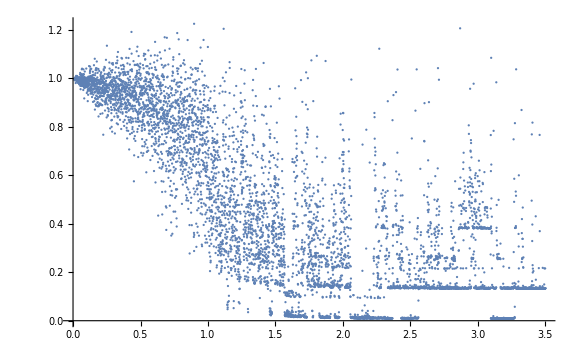

```mathematica
ListPlot[Transpose[{z6x,z6y}],PlotRange->All]
```

```mathematica
lengthv=3490*2;sepv=10;
z6xcycC=Table[0,{i,1,lengthv/sepv}];
z6ycycC=Table[0,{i,1,lengthv/sepv}];
For[i=1,i≤(lengthv/sepv),i++,
tptx=Table[0,{i,1,sepv+1}];
tpty=Table[0,{i,1,sepv+1}];
For[j=1,j≤sepv+1,j++,
tptx[[j]]=z6x[[(i-1)*sepv+j]];
tpty[[j]]=z6y[[(i-1)*sepv+j]];
];
z6xcycC[[i]]=midv[tptx];
z6ycycC[[i]]=midv[tpty];
];
```

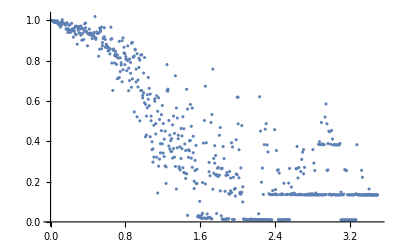

```mathematica
ListPlot[Transpose[{z6xcycC,z6ycycC}],PlotRange->All]
```

```mathematica
z2crit={0.02313995,0.02205658,0.03864288,0.03286743,0.3525314,0.03549194,0.02288818,0.3512319,0.04232788,0.02220154,0.02294159,0.0226059,0.6224493,0.2681046,0.3600082,0.02632141,0.02144623,0.02471924,0.02224731,0.02225494,0.02170563,0.02592468,0.3649928,0.05225372,0.02174377,0.02256775,0.02172852,0.02895355,0.03098297,0.02210999,0.02301025,0.02294922,0.02220917,0.02280426,0.02194977,0.03112793,0.3547491,0.03527832,0.02225494,0.02166748,0.02201843,0.04305267,0.04255676,0.02220154,0.3547541,0.3853836,0.03409576,0.3503749,0.02666473,0.02231598,0.02681732,0.3574804,0.0435791,0.02291107,0.02315521,0.359225,0.05211639,0.02901459,0.02179718,0.02853394,0.04184723,0.03152466,0.3867442,0.07954407,0.0268631,0.3528722,0.04427338,0.02239227,0.02228546,0.02274323,0.0222168,0.022789,0.3527578,0.0355835,0.02615356,0.03160858,0.02233124,0.02236176,0.02225494,0.02831268,0.08171082,0.07521057,0.03456879,0.03535461,0.02235413,0.3515625,0.3583781,0.03527069,0.3526662,0.03624725,0.02165985,0.02196503,0.02301788,0.02209473,0.02275848,0.02227783,0.02278137,0.02240753,0.02149963,0.3560461,0.0311203,0.02257538,0.02276611,0.3527603,0.03496552,0.02159882,0.02216339,0.02239227,0.02251434,0.02288818,0.02133179,0.02258301,0.02367401,0.02346039,0.02194977,0.02266693,0.02246094,0.02206421,0.02210999,0.02210236,0.02207947,0.02450562,0.03375244,0.03894043,0.02174377,0.0320282,0.03363037,0.02204132,0.02231598,0.02230072,0.02220154,0.02207947,0.02239227,0.02209473,0.0219574,0.02224731,0.02222443,0.02249146,0.02252197,0.02222443,0.02225494,0.0230484,0.02288818,0.03025818,0.02193451,0.02251434,0.03168488,0.02173615,0.02243042,0.02207947,0.02877045,0.661555,0.3666687,0.04110718,0.02294922,0.02230835,0.02283478,0.02202606,0.02204895,0.02313995,0.02251434,0.02941895,0.02799988,0.02249908,0.02366638,0.02285767,0.02252197,0.0226593,0.02210999,0.02891541,0.0329361,0.02448273,0.02871704,0.02236176,0.02222443,0.02241516,0.02334595,0.02254486,0.02298737,0.02289581,0.02190399,0.03105164,0.02855682,0.02243805,0.3596776,0.0484314,0.02222443,0.02202606,0.02230835,0.02152252,0.02968597,0.02971649,0.02196503,0.02214813,0.02127838,0.3600515,0.04386139,0.02190399,0.02161407,0.02232361,0.02224731,0.02846527,0.03312683,0.03244019,0.0306778,0.02288055,0.02201843,0.02402496,0.02146149,0.02270508,0.03295898,0.02973175,0.02294159,0.02250671,0.02223969,0.02902222,0.03436279,0.03370667,0.03145599,0.02153778,0.02159119,0.02196503,0.0216217,0.04285431,0.04854584,0.02180481,0.02238464,0.02297974,0.0227356,0.3545024,0.0357132,0.02425385,0.02532959,0.03381348,0.02681732,0.3498179,0.04392242,0.3492355,0.5256653,0.5476125,0.5186081,0.5528285,0.06958771,0.02845001,0.02205658,0.3486608,0.4006882,0.7807922,0.953715,0.8714752,0.9570694,0.9200643,0.5563024,0.5520147,0.8336029,0.78921,0.4438248,0.4491857,0.4668121,0.03523254,0.03224182,0.03359222,0.3585612,0.1715622,0.6436819,0.8274511,0.8370336,0.990064,0.6877009,0.9140015,0.03497314,0.02224731,0.02217102,0.02283478,0.02687836,0.3573176,0.03081512,0.02263641,0.02244568,0.02296448,0.02253723,0.0222168,0.02271271,0.02255249,0.02249146,0.02297211,0.02658081,0.02610779,0.02346039,0.02217102,0.02285767,0.03311157,0.02215576,0.02236938,0.02322388,0.02204132,0.02271271,0.02182007,0.02261353,0.02225494,0.0221405,0.3528366,0.04135895,0.3547211,0.03073883,0.02915192,0.08706665,0.109787,0.02646637,0.3530197,0.3578847,0.02596283,0.02213287,0.3514735,0.03121948,0.02226257,0.02735138,0.03145599,0.02297974,0.02409363,0.03315735,0.03322601,0.02718353,0.02224731,0.02249908,0.02182007,0.02337646,0.02274323,0.02210236,0.02235413,0.02259064,0.02222443,0.02226257,0.02130127,0.02189636,0.02449036,0.03290558,0.02837372,0.02207947,0.3546346,0.0433197,0.3541209,0.04100037,0.0222702,0.02458191,0.03315735,0.02545166,0.3523992,0.04395294,0.03417969,0.04620361,0.05496216,0.3492559,0.04465485,0.02220917,0.02178192,0.02235413,0.02209473,0.3559672,0.04341888,0.02908325,0.02237701,0.02285004,0.02271271,0.02246857,0.02222443,0.02275085,0.02230072,0.02259064,0.02993011,0.100708,0.03866577,0.02219391,0.02285004,0.3548635,0.03527069,0.02142334,0.02236176,0.02306366,0.02212524,0.0227356,0.02297974,0.02295685,0.02271271,0.0228653,0.02206421,0.02255249,0.02185822,0.351326,0.03508759,0.02206421,0.02274323,0.02163696,0.0225296,0.3514659,0.04188538,0.02918243,0.02161407,0.02250671,0.02243042,0.02178192,0.0226059,0.02254486,0.02191162,0.02248383,0.02091217,0.02212524,0.02267456,0.02218628,0.3658727,0.05377197,0.02718353,0.02218628,0.02264404,0.02243042,0.02233887,0.02251434,0.02283478,0.02253723,0.02225494,0.02177429,0.0230484,0.02249146,0.02242279,0.02259064,0.02404022,0.0326004,0.02294159,0.02740479,0.03397369,0.04254913,0.08498383,0.0383606,0.02204132,0.0217514,0.02310181,0.02324677,0.02204132,0.02204895,0.02310181,0.02253723,0.354248,0.02599335,0.02209473,0.02192688,0.02284241,0.02155304,0.02233887,0.02319336,0.02233124,0.4284872,0.437734,0.4345729,0.5899836,0.5932719,0.1879578,0.02215576,0.02253723,0.3551712,0.04320526,0.02190399,0.02252197,0.02194977,0.02224731,0.02164459,0.02181244,0.02178192,0.02296448,0.02230072,0.02199554,0.02163696,0.02305603,0.02239227,0.02226257,0.02183533,0.04886627,0.6896769,0.1246338,0.02213287,0.02178192,0.02144623,0.02252197,0.02513885,0.3543981,0.04306793,0.02899933,0.02235413,0.02199554,0.02223206,0.02250671,0.02268219,0.02205658,0.02219391,0.03512573,0.04743958,0.0222168,0.03035736,0.03250122,0.02724457,0.02289581,0.03655243,0.04672241,0.03070831,0.02238464,0.022789,0.02766418,0.03318024,0.03308868,0.05197144,0.04844666,0.02246857,0.0228653,0.02210236,0.02236938,0.022789,0.02211761,0.02231598,0.02242279,0.02238464,0.02238464,0.8962047,0.3877029,0.09888458,0.02173615,0.02204132,0.02328491,0.3544922,0.02669525,0.02237701,0.02187347,0.02268219,0.0213623,0.02245331,0.02285004,0.02474213,0.03292084,0.03130341,0.02205658,0.02922058,0.02935028,0.02761078,0.03081512,0.02219391,0.3536301,0.02703094,0.05267334,0.04111481,0.02220154,0.02265167,0.02249146,0.02246094,0.02283478,0.02180481,0.02214813,0.0254364,0.03384399,0.3514709,0.04404449,0.3698756,0.04624176,0.03064728,0.02251434,0.02277374,0.02249908,0.02667999,0.02467346,0.04959106,0.048172,0.02239227,0.02174377,0.02290344,0.02109528,0.02336121,0.02225494,0.02242279,0.02264404,0.3531927,0.3673096,0.1057434,0.03967285,0.03224182,0.02258301,0.02275848,0.02165985,0.03084564,0.3576279,0.03945923,0.04345703,1.29257,0.6773657,0.4441884,0.7107671,0.5912704,0.9792354,0.1706467,0.3712438,0.1222534,0.04082489,0.02277374,0.02651978,0.02307892,0.02213287,0.3636932,0.04750061,0.04960632,0.3672892,0.03944397,0.02258301,0.02166748,0.02243805,0.02250671,0.0215683,0.02279663,0.02245331,0.04895782,0.06848907,0.7690862,0.7462744,0.2479553,1.316475,0.7752686,1.106005,0.6183268,0.6971054,0.9242808,0.9756724,0.9136353,0.7765884,1.175969,0.7208023,0.4793015,0.4073741,0.08035278,0.02449799,0.0214386,0.02165985,0.02161407,0.02200317,0.02210236,0.02233124,0.3481344,0.02362061,0.02279663,0.02406311,0.05500031,0.03382111,0.02239227,0.0262146,0.02437592,0.02310944,0.02127075,0.02226257,0.02307892,0.02310944,0.02232361,0.02279663,0.02180481,0.02272034,0.02131653,0.02928925,0.03085327,0.02166748,0.02261353,0.03239441,0.03200531,0.0219574,0.03017426,0.02223206,0.03339386,0.02645874,0.02214813,0.02133179,0.02191925,0.02233124,0.02258301,0.02193451,0.02201843,0.9894206,0.05630493,0.03755188,0.02648926,0.02198792,0.02212524,0.3546448,0.03554535,0.02207184,0.02193451,0.0293045,0.03140259,0.02250671,0.02243805,0.02185059,0.3518524,0.04488373,0.02927399,0.02266693,0.02207184,0.02186584,0.3513362,0.03256226,0.03176117,0.02620697,0.02298737,0.02336884,0.02182007,0.02263641,0.02301025,0.02266693,0.02248383,0.02166748,0.6639786,0.1098557,0.03404236,0.3626175,0.04785919,0.3516998,0.04653168,0.3518982,0.0352478,0.0224762,0.02274323,0.02280426,0.03556061,0.05217743,0.03072357,0.02191925,0.02294922,0.0220108,0.02360535,0.03799438,0.04660797,0.04476166,0.5313721,1.004288,0.7846095,0.5021515,0.1333008,0.02178192,0.02281952,0.02219391,0.02187347,0.02207184,0.02153015,0.02239227,0.02177429,0.02529144,0.02696228,0.02216339,0.3487727,0.0318222,0.02236938,0.02942657,0.05492401,0.02223969,0.02242279,0.02259064,0.02204895,0.02231598,0.02199554,0.02361298,0.02146149,0.02243805,0.02435303,0.03487396,0.03263855,0.03324127,0.02224731,0.02191925,0.02153778,0.02211761,0.02224731,0.02112579,0.3531545,0.02839661,0.02210999,0.3544464,0.04871368,0.03460693,0.02481842,0.02199554,0.02259064,0.02355194,0.02217865,0.02173615,0.0218277,0.02251434,0.02248383,0.02272034,0.02272034,0.02128601,0.02276611,0.02173615,0.02127075,0.02236938,0.02200317,0.02204132,0.02322388,0.02258301,0.02172852,0.02227783,0.0218277,0.0224762,0.02194214,0.02190399,0.02230072,0.02902222,0.03040314,0.02292633,0.02201843,0.02218628,0.02212524,0.02352905,0.0222702,0.02266693,0.02191925,0.02967072,0.0294342,0.02231598,0.03539276,0.04605865,0.03277588,0.02279663,0.02187347,0.02346039,0.02272797,0.02223969,0.02230072,0.0221405,0.02220154,0.02307892,0.02204895,0.02229309,0.03350067,0.05110168,0.02838135,0.02350616,0.02267456,0.02259064,0.02241516,0.02240753,0.02349854,0.02185822,0.03516388,0.3637772,0.06053925,0.02423096,0.02277374,0.02196503,0.3621699,0.03533936,0.021698,0.02231598,0.02185059,0.02166748,0.02248383,0.02231598,0.02285767,0.02204132,0.02210999,0.02118683,0.02214813,0.02275848,0.02199554,0.02209473,0.04195404,0.03427887,0.0227356,0.02288818,0.0218811,0.02231598,0.0223999,0.3542888,0.03914642,0.02240753,0.028862,0.02452087,0.3484701,0.04991913,0.3727392,0.03443146,0.02986908,0.02194214,0.02191162,0.02216339,0.02251434,0.02230835,0.02336121,0.3483098,0.03785706,0.02207947,0.0222168,0.02136993,0.02176666,0.02314758,0.3527247,0.03503418,0.02983856,0.02856445,0.02235413,0.0220871,0.3544032,0.03035736,0.02237701,0.02194977,0.02183533,0.02253723,0.02233124,0.02262115,0.02295685,0.02098846,0.0226059,0.03575897,0.03520966,0.3878225,0.1197586,0.03479004,0.02250671,0.03129578,0.03211212,0.02185059,0.02243042,0.02213287,0.02265167,0.0226059,0.02198792,0.0222168,0.03104401,0.02411652,0.03126526,0.02526855,0.03321838,0.03321075,0.02980042,0.03288269,0.02255249,0.04154968,0.04927826,0.02211761,0.3486404,0.03580475,0.03312683,0.6673838,0.06577301,0.02872467,0.02198792,0.02198029,0.02177429,0.02246857,0.02220154,0.02276611,0.02258301,0.04851532,0.02948761,0.02177429,0.02239227,0.02243805,0.02263641,0.02319336,0.03600311,0.3672053,0.0435791,0.02217102,0.02248383,0.0225296,0.02297211,0.04671478,0.03052521,0.02239227,0.02252197,0.0230484,0.02142334,0.02687073,0.03253937,0.02246094,0.02223969,0.3601786,0.3654861,0.1294785,0.0500412,0.02352142,0.3485311,0.6571707,0.6586813,0.5931727,0.3845749,0.3704249,0.0351181,0.02203369,0.02223969,0.03469849,0.05007172,0.02180481,0.0244751,0.02246857,0.02215576,0.02196503,0.02155304,0.02267456,0.3540319,0.04467773,0.02249908,0.02305603,0.02307129,0.02265167,0.02209473,0.02288818,0.02197266,0.02294922,0.3524475,0.04129028,0.02481842,0.0506897,0.05493164,0.02230072,0.02212524,0.02210236,0.02235413,0.02266693,0.02191925,0.02311707,0.02180481,0.02199554,0.02922821,0.02388,0.04724121,0.05418396,0.02683258,0.02246857,0.02185059,0.7076136,0.4680354,0.03448486,0.02236176,0.02268219,0.02308655,0.0219574,0.02186584,0.02223206,0.02960205,0.03325653,0.02197266,0.02131653,0.02228546,0.02147675,0.04213715,0.02922058,0.02217102,0.3508199,0.04351044,0.02177429,0.02267456,0.02240753,0.02219391,0.0224762,0.021492,0.3527934,0.03017426,0.02270508,0.02973175,0.03318787,0.02921295,0.02204895,0.02272797,0.6164602,0.4298757,0.370814,0.3889567,0.02866364,0.02806091,0.102211,0.02891541,0.02954865,0.02832794,0.02241516,0.0224762,0.3532054,0.03903198,0.0217514,0.02198029,0.02321625,0.02258301,0.02296448,0.3484624,0.04997253,0.0290451,0.02220917,0.0224762,0.02631378,0.03059387,0.02884674,0.02648926,0.02287292,0.02283478,0.02340698,0.0321579,0.0297699,0.02194977,0.02171326,0.0224762,0.3659846,0.3757528,0.3740514,0.02624512,0.5870209,0.5472565,0.04431915,0.0230484,0.02267456,0.02216339,0.3538412,0.03760529,0.0316925,0.021698,0.0291214,0.02672577,0.02222443,0.02186584,0.04963684,0.05580139,0.3729909,0.3798752,0.3722585,0.03759003,0.03392029,0.04264069,0.350057,0.02711487,0.02171326,0.02911377,0.02323151,0.02240753,0.02237701,0.02206421,0.02214813,0.02194214,0.3519465,0.02690125,0.02319336,0.02276611,0.02305603,0.02339172,0.02172852,0.02216339,0.02370453,0.02230835,0.02163696,0.02164459,0.02259827,0.03112793,0.03205109,0.9888,0.6317902,0.9839122,1.038628,0.6801555,0.5645142,0.6742885,0.6836726,0.7840195,0.8345286,0.4444656,0.7052231,0.9735031,0.66627,0.7107341,0.875946,0.5509491,0.03635406,0.02268219,0.02229309,0.0230484,0.02196503,0.02193451,0.021698,0.02503204,0.03023529,0.02277374,0.02285767,0.02143097,0.02155304,0.02688599,0.04249573,0.0500946,0.3650233,0.3895213,0.04705811,0.02178192,0.0220871,0.02336121,0.02213287,0.02425385,0.02354431,0.02240753,0.02268219,0.02243805,0.02158356,0.02224731,0.02231598,0.02211761,0.02240753,0.02232361,0.02836609,0.02250671,0.02162933,0.02232361,0.02246094,0.02251434,0.02294159,0.03204346,0.02237701,0.02255249,0.02173615,0.02292633,0.3513209,0.03897095,0.02284241,0.02732849,0.3607559,0.04471588,0.3543422,0.0291214,0.02185059,0.02243042,0.0223999,0.02942657,0.02264404,0.0223465,0.0224762,0.02209473,0.02262878,0.03288269,0.02838898,0.0223999,0.0225296,0.02213287,0.021698,0.3562698,0.04303741,0.02233887,0.02285767,0.02258301,0.0224762,0.02265167,0.02305603,0.0225296,0.02844238,0.02242279,0.02190399,0.0216217,0.02186584,1.005836,0.9232254,0.4340617,0.8355179,0.08883667,0.02263641,0.02201843,0.02217865,0.02400208,0.02912903,0.05479431,0.3925502,0.04510498,0.04148102,0.05488586,0.0230484,0.02237701,0.02295685,0.02226257,0.02223206,0.02261353,0.02241516,0.02168274,0.02268982,0.3522415,0.6783447,0.3711777,0.04610443,0.04124451,0.02799225,0.0226593,0.02855682,0.0222168,0.0221405,0.353152,0.0539093,0.02282715,0.6165492,0.7913081,0.7061234,0.8143641,0.6808726,0.7656631,0.5991669,0.6052653,0.283699,0.07872772,0.02250671,0.02328491,0.02272797,0.02178955,0.021492,0.0218811,0.02430725,0.3609695,0.0351181,0.0218277,0.02087402,0.02265167,0.02314758,0.0226593,0.02232361,0.02268219,0.02909088,0.03299713,0.6324081,0.7994436,0.4572729,0.09085846,0.02259064,0.02259064,0.3600667,0.05158997,0.02687073,0.0220108,0.02344513,0.02235413,0.02303314,0.02146149,0.02685547,0.3583145,0.671814,0.09693146,0.0322113,0.02236176,0.3548737,0.06360626,0.03348541,0.02184296,0.3533427,0.03440857,0.02424622,0.02464294,0.02341461,0.02222443,0.02236176,0.02212524,0.02305603,0.3494594,0.0269165,0.02282715,0.02878571,0.3737717,0.0386734,0.02203369,0.02245331,0.02233887,0.02207947,0.02264404,0.02276611,0.02157593,0.02244568,0.02333832,0.02224731,0.02449799,0.02789307,0.02239227,0.02291107,0.0231781,0.02280426,0.02283478,0.0224762,0.02346039,0.02899933,0.04282379,0.03311157,0.02355194,0.02235413,0.02311707,0.0223465,0.3526179,0.6809616,0.5852737,0.6747665,0.3300781,0.03125763,0.03266144,0.0226593,0.02255249,0.02276611,0.02281952,0.03344727,0.02220917,0.02266693,0.02246857,0.02223969,0.02313995,0.02201843,0.02318573,0.02230072,0.3513006,0.03165436,0.3514938,0.04421997,0.02209473,0.02313995,0.02230072,0.0225296,0.04029846,0.02999115,0.02288818,0.02171326,0.02307892,0.0218811,0.02462006,0.03331757,0.03257751,0.02281952,0.02261353,0.02844238,0.03207397,0.02926636,0.02236176,0.0223465,0.0220871,0.3514048,0.03081512,0.02297974,0.02268982,0.04199219,0.03577423,0.02263641,0.02297974,0.02258301,0.02228546,0.02202606,0.02275848,0.3525925,0.04386139,0.0227356,0.02225494,0.02275848,0.02262878,0.02154541,0.02222443,0.03565216,0.04743958,0.02890015,0.0212326,0.02192688,0.02269745,0.02244568,0.02173615,0.02264404,0.02733612,0.03343201,0.03357697,0.3540777,0.02697754,0.02281952,0.02248383,0.02174377,0.021698,0.06481171,0.06854248,0.02211761,0.02246094,0.02249146,0.02321625,0.02200317,0.3488464,0.36306,0.04026031,0.02998352,0.03179169,0.02207184,0.02231598,0.02300262,0.02200317,0.02264404,0.02205658,0.02156067,0.3601024,0.03333282,0.02736664,0.02703857,0.02205658,0.3537394,0.05308533,0.04840088,0.3504969,0.03015137,0.0227356,0.0224762,0.3542404,0.3561503,0.02592468,0.02238464,0.02142334,0.02245331,0.3540065,0.03541565,0.03350067,0.03315735,0.0220871,0.02238464,0.02207184,0.02616119,0.02871704,0.02261353,0.02306366,0.02184296,0.02226257,0.02201843,0.02249146,0.02213287,0.02282715,0.02227783,0.02204132,0.3485998,0.03285217,0.02441406,0.02193451,0.02194214,0.02241516,0.02312469,0.02257538,0.02214813,0.02164459,0.02222443,0.03155518,0.02404022,0.02243805,0.0218277,0.03910065,0.03598785,0.03079224,0.02311707,0.3485286,0.04125977,0.3500824,0.3701884,0.09689331,0.02633667,0.03577423,0.3635915,0.03934479,0.03263092,0.7073466,0.6404495,0.5833613,0.4029287,0.1326294,0.1048203,0.02274323,0.02201843,0.3526382,0.6694717,0.3969142,0.1039505,0.02568054,0.02250671,0.03157806,0.02758789,0.03308868,0.02237701,0.02474213,0.03121948,0.02284241,0.02205658,0.02352905,0.02276611,0.02232361,0.0223465,0.02403259,0.3633321,0.02902985,0.02243805,0.02533722,0.03262329,0.02162933,0.02277374,0.02201843,0.0224762,0.02231598,0.02153778,0.0247879,0.02653503,0.04191589,0.03804779,0.03359985,0.02212524,0.0217514,0.04879761,0.0485611,0.3495229,0.04071808,0.0329895,0.03073883,0.03946686,0.03774261,0.0248642,0.02240753,0.02326202,0.02700806,0.03324127,0.03111267,0.02147675,0.02183533,0.02230072,0.02171326,0.02285004,0.02225494,0.02235413,0.02205658,0.02209473,0.0224762,0.02265167,0.02159882,0.02223206,0.02220917,0.3480632,0.05154419,0.02861786,0.02233887,0.02230072,0.02197266,0.3528697,0.6745834,0.7585882,0.8128611,0.1005478,0.03527832,0.03358459,0.02251434,0.034935,0.05548859,0.03240967,0.3521118,0.04295349,0.02229309,0.02249908,0.02261353,0.02261353,0.02210236,0.3525136,0.03787231,0.03023529,0.02255249,0.02656555,0.03229523,0.02222443,0.02302551,0.02282715,0.02233124,0.02204895,0.3517482,0.03498077,0.03155518,0.02189636,0.02242279,0.02245331,0.02228546,0.02198792,0.0224762,0.04190826,0.04270935,0.02344513,0.02268219,0.03061676,0.02568054,0.02280426,0.02153778,0.02217102,0.02278137,0.02271271,0.02297211,0.04284668,0.02827454,0.02210999,0.02242279,0.02259827,0.02246094,0.02713776,0.02385712,0.3487066,0.03140259,0.02231598,0.02274323,0.02251434,0.3702113,0.3825277,0.0724411,0.03100586,0.032547,0.02371979,0.02307129,0.03566742,0.04080963,0.02212524,0.3624725,0.03766632,0.0510788,0.05464172,0.0227356,0.02214813,0.02301788,0.02236176,0.02291107,0.02288818,0.02133179,0.02241516,0.02219391,0.02262115,0.02282715,0.02194214,0.02224731,0.3545939,0.04225159,0.02254486,0.02103424,0.0218277,0.0425415,0.05474854,0.02257538,0.02710724,0.02325439,0.02201843,0.02194977,0.02322388,0.02194214,0.02246857,0.03842163,0.03578186,0.02231598,0.351382,0.04440308,0.02292633,0.3485515,0.03747559,0.02246857,0.02285767,0.02224731,0.02265167,0.02616882,0.03090668,0.3510793,0.04349518,0.3687948,0.3727722,0.09835052,0.3587341,0.04062653,0.02267456,0.02256775,0.02112579,0.02256012,0.353775,0.03218079,0.0222168,0.0224762,0.02272797,0.02205658,0.02191162,0.02173615,0.02180481,0.02277374,0.02929688,0.03749084,0.6353048,0.7365875,0.2620621,0.02910614,0.02281189,0.350914,0.03351593,0.3833364,0.05265045,0.03191376,0.0225296,0.02680969,0.3638179,0.4657974,0.4160792,0.1070709,0.0353775,0.03669739,0.02190399,0.02289581,0.02567291,0.02970123,0.02281189,0.02114868,0.02345276,0.02336121,0.02240753,0.02355194,0.02225494,0.02250671,0.02263641,0.02290344,0.022995,0.02321625,0.0223999,0.02257538,0.02294159,0.02193451,0.02278137,0.0215683,0.02336121,0.03328705,0.02223206,0.3552501,0.3732961,0.5736644,0.366628,0.6763992,0.3986588,0.06661224,0.0220871,0.02238464,0.02222443,0.03067017,0.02420807,0.02187347,0.02223206,0.354805,0.04336548,0.02245331,0.02153778,0.02288055,0.3508937,0.3550924,0.02668762,0.3519236,0.03640747,0.022995,0.02169037,0.02232361,0.3487422,0.364006,0.3853048,0.04399109,0.3522644,0.04022217,0.02189636,0.02175903,0.02114868,0.02261353,0.02236176,0.03170776,0.02173615,0.02256775,0.02223206,0.02333832,0.04467773,0.07036591,0.3720271,0.04090118,0.02307129,0.02320862,0.02230835,0.02255249,0.02292633,0.02278137,0.02256775,0.02127838,0.02217865,0.02279663,0.0220108,0.02236938,0.02407074,0.02293396,0.02975464,0.02684784,0.02236938,0.04843903,0.3624776,0.02722168,0.06621552,0.09753418,0.02223969,0.04885864,0.3563995,0.03520966,0.02268219,0.02246094,0.02230072,0.02239227,0.02256775,0.02251434,0.022789,0.02224731,0.3598887,0.3765284,0.0430603,0.02268219,0.02884674,0.02432251,0.02190399,0.02261353,0.02220917,0.0220108,0.0240097,0.02235413,0.02232361,0.02201843,0.8963649,0.1385117,0.04152679,0.02239227,0.02212524,0.02282715,0.02241516,0.3527247,0.03469086,0.02229309,0.02249146,0.02262115,0.02220154,0.02239227,0.3528544,0.03144836,0.04868317,0.02844238,0.06642914,0.8016841,0.5766627,0.4968109,0.399381,0.05391693,0.02194977,0.02203369,0.02225494,0.02199554,0.6404597,0.09893799,0.09198761,0.02438354,0.02275848,0.0252533,0.0337677,0.03321075,0.3496628,0.04402161,0.02231598,0.02226257,0.354777,0.02693939,0.0248642,0.02497101,0.02278137,0.02741241,0.3484116,0.03954315,0.02313232,0.9900742,0.6668472,0.0670929,0.03147888,0.02229309,0.02194214,0.02174377,0.02313232,0.02202606,0.02401733,0.05097961,0.04208374,0.03253937,0.6674856,0.09549713,0.02815247,0.02341461,0.02178955,0.0221405,0.02162933,0.02174377,0.02220154,0.3542888,0.3597387,0.4580612,0.07144165,0.02648163,0.02227783,0.3563461,0.3654836,0.03540039,0.02201843,0.02259827,0.02143097,0.0220108,0.02243805,0.02225494,0.3515117,0.0345459,0.03251648,0.04272461,0.0255127,0.02935791,0.03366852,0.03330994,0.02227783,0.02222443,0.3543142,0.05491638,0.0295105,0.0217514,0.02183533,0.02281952,0.02222443,0.02231598,0.02274323,0.02199554,0.02282715,0.02249908,0.02201843,0.02967072,0.3665492,0.3560054,0.04346466,0.02256775,0.6722183,0.4896647,0.4275258,0.1103745,0.04273987,0.03113556,0.02261353,0.3833669,1.163615,1.056592,0.7144928,0.6732382,0.5093054,0.02706909,0.3523382,0.04355621,0.3649826,0.03201294,0.02210999,0.02265167,0.02254486,0.04801178,0.05477905,0.03303528,0.03233337,0.02741241,0.02300262,0.02246094,0.02253723,0.02154541,0.02288055,0.3521932,0.363294,0.04309082,0.02249908,0.02330017,0.02610779,0.02705383,0.02149963,0.02804565,0.03045654,0.02733612,0.039711,0.02240753,0.02202606,0.02481842,0.02842712,0.02275848,0.02320862,0.02222443,0.02166748,0.352857,0.04310608,0.02278137,0.02270508,0.02204895,0.02263641,0.02245331,0.02296448,0.02217102,0.02199554,0.02171326,0.021492,0.02265167,0.0226593,0.02261353,0.02201843,0.02265167,0.02204132,0.022789,0.0222702,0.0220108,0.0221405,0.02243805,0.02266693,0.02228546,0.02233887,0.03015137,0.0456543,0.05339813,0.3631516,0.6936519,0.04632568,0.3581721,0.03510284,0.03121948,0.02870178,0.02223206,0.9883423,0.06552887,0.02236176,0.02285767,0.02320862,0.02294159,0.02285004,0.02262115,0.02178955,0.02165985,0.02164459,0.03134918,0.02366638,0.04957581,0.05291748,0.02209473,0.02244568,0.02257538,0.02256775,0.02223206,0.02280426,0.02172852,0.02246857,0.02146912,0.02285004,0.0217514,0.6733195,0.1123734,0.5800171,0.170929,0.02458954,0.02236938,0.02386475,0.03276062,0.02277374,0.02258301,0.02252197,0.02175903,0.02140808,0.0220108,0.3489761,0.03507233,0.02198792,0.02288818,0.02193451,0.02196503,0.02266693,0.02213287,0.02768707,0.02629089,0.8972931,1.245962,0.424614,0.5923208,0.5757828,0.6371943,0.8062236,0.9699809,0.2219849,0.197052,0.1857224,0.1206436,0.0223999,0.02333832,0.04168701,0.5811107,0.1669235,0.02207184,0.02230072,0.02279663,0.02242279,0.0228653,0.02979279,0.0539093,0.02403259,0.02357483,0.02204895,0.02259827,0.02185822,0.3634567,0.06445313,0.02914429,0.02185822,0.02197266,0.02179718,0.03018951,0.02893829,0.02191162,0.02268982,0.02220154,0.02220917,0.05712128,0.05565643,0.3568115,0.02655029,0.02165985,0.02235413,0.02250671,0.02237701,0.02216339,0.02259827,0.02362823,0.02307129,0.02135468,0.0222702,0.02217102,0.03024292,0.05233765,0.02175903,0.02228546,0.02256012,0.02300262,0.02227783,0.02245331,0.3494085,0.04293823,0.05487823,0.02220154,0.02279663,0.0223999,0.02264404,0.02314758,0.02289581,0.3486074,0.04225922,0.02266693,0.02237701,0.02197266,0.02204132,0.02225494,0.02262878,0.02275848,0.02268219,0.02565765,0.03375244,0.03275299,0.02180481,0.02257538,0.03178406,0.03033447,0.02282715,0.02285004,0.02253723,0.02393341,0.1099319,0.03375244,0.02799225,0.02852631,0.02812195,0.02196503,0.02183533,0.02326202,0.02876282,0.02659607,0.3558629,0.03024292,0.02235413,0.3529282,0.382075,0.03508759,0.0228653,0.04915619,0.04787445,0.02167511,0.02231598,0.02132416,0.02315521,0.02288055,0.3551661,0.9121399,0.5023727,0.4164022,0.4000524,0.4156215,0.03012085,0.02300262,0.02214813,0.02235413,0.02203369,0.02276611,0.0227356,0.02300262,0.02198029,0.02211761,0.02170563,0.02262878,0.0230484,0.02648163,0.04645538,0.04184723,0.02339172,0.02233887,0.04755402,1.533689,0.6141357,1.015592,0.4640554,0.06912231,0.3501028,0.04334259,0.0223465,0.02170563,0.02233887,0.02232361,0.02225494,0.3546855,0.03544617,0.35849,0.03406525,0.02277374,0.05402374,0.0224762,0.02212524,0.02284241,0.02136993,0.02274323,0.02249908,0.02245331,0.03378296,0.04096222,0.02293396,0.02470398,0.02643585,0.02274323,0.02284241,0.02641296,0.02928925,0.02227783,0.02257538,0.02249908,0.3496246,0.3623098,0.02552795,0.3486812,0.03562164,0.02990723,0.02800751,0.03017426,0.0283432,0.02272034,0.02243042,0.02278137,0.02196503,0.02246094,0.02124023,0.02238464,0.02181244,0.02237701,0.02254486,0.0222168,0.02198029,0.02259827,0.02242279,0.02945709,0.02993011,0.02216339,0.02233124,0.02190399,0.02233887,0.3522415,0.03559875,0.02370453,0.03121185,0.03036499,0.02216339,0.02198792,0.0491333,0.04891205,0.02188873,0.02140045,0.02243042,0.02333069,0.02174377,0.02204132,0.02285767,0.02226257,0.02204895,0.02258301,0.02191925,0.02276611,0.02160645,0.0221405,0.02244568,0.03517914,0.04554749,0.02787781,0.3499705,0.03507233,0.03092957,0.02912903,0.6431147,0.3241577,0.02885437,0.02241516,0.02204895,0.02156067,0.0271759,0.0305481,0.02203369,0.02227783,0.02256012,0.3511302,0.03968811,0.3508021,0.03102112,0.02270508,0.3500493,0.02990723,0.02120209,0.02251434,0.02458191,0.3629761,0.02913666,0.02251434,0.02316284,0.02230835,0.3535665,0.02655792,0.02677155,0.03391266,0.03131866,0.0247345,0.03052521,0.02158356,0.02289581,0.03227234,0.03351593,0.02867126,0.02155304,0.02187347,0.02191162,0.0222168,0.02126312,0.0218277,0.02196503,0.02896881,0.3551865,0.044487,0.02281189,0.02209473,0.02206421,0.3522136,0.03656006,0.02189636,0.02220917,0.02275848,0.02175903,0.02282715,0.02131653,0.02257538,0.02289581,0.02182007,0.02243805,0.02229309,0.02264404,0.02157593,0.0311203,0.03292847,0.02667999,0.02313232,0.03585815,0.02846527,0.0226593,0.02277374,0.03092957,0.02245331,0.02215576,0.0220108,0.03061676,0.02233124,0.02153015,0.02202606,0.02213287,0.0221405,0.02287292,0.02291107,0.02252197,0.0251236,0.0297699,0.02316284,0.02220154,0.02214813,0.02176666,0.02298737,0.02246094,0.02219391,0.02677917,0.02919769,0.02132416,0.0222168,0.02250671,0.02181244,0.02509308,0.03327942,0.03361511,0.02654266,0.02266693,0.02252197,0.02258301,0.04133606,0.03478241,0.02231598,0.0214386,0.02974701,0.02810669,0.02215576,0.02191925,0.02681732,0.02905273,0.03660583,0.05114746,0.02642059,0.02559662,0.06771851,0.02516937,0.02246094,0.02216339,0.02267456,0.3545685,0.03496552,0.3546041,0.07491302,0.3842087,0.02574158,0.02207947,0.0225296,0.02210236,0.02258301,0.02204132,0.02262878,0.02646637,0.02861023,0.0228653,0.02120209,0.02253723,0.04708862,0.04331207,0.02189636,0.02253723,0.02278137,0.02612305,0.04111481,0.05516052,0.356809,0.04125977,0.0239563,0.02475739,0.03150177,0.02271271,0.02287292,0.03865814,0.0414505,0.0251236,0.02405548,0.02250671,0.02268219,0.05419922,0.02253723,0.02171326,0.02232361,0.02246094,0.02187347,0.02535248,0.03370667,0.02361298,0.02248383,0.3536758,0.09179688,0.02833557,0.02194977,0.02271271,0.02318573,0.02316284,0.02220154,0.02185822,0.02723694,0.02632141,0.02690887,0.02256775,0.02220154,0.3498001,0.3546753,0.3547821,0.04297638,0.03189087,0.0290451,0.02448273,0.02875519,0.02248383,0.02245331,0.02272034,0.02886963,0.3510666,0.04026031,0.02236176,0.02237701,0.05630493,0.05471802,0.02275085,0.0223465,0.02935028,0.03067017,0.02228546,0.03264618,0.03327942,0.02682495,0.02259827,0.02249908,0.0223999,0.02206421,0.0227356,0.02242279,0.02204895,0.3507996,0.04430389,0.03327179,0.05628204,0.02310181,0.02151489,0.022789,0.03106689,0.0265274,0.02245331,0.0295105,0.02996063,0.0223465,0.02219391,0.0271759,0.02645874,0.02294159,0.04870605,0.05528259,0.03730011,0.03276062,0.03326416,0.6662369,0.1055756,0.02213287,0.04152679,0.0425415,0.02199554,0.0223999,0.02290344,0.02226257,0.02204132,0.02264404,0.02246857,0.34994,0.1022263,0.03384399,0.393514,0.1424637,0.04194641,0.02169037,0.3530172,0.03041077,0.04193878,0.02813721,0.3486049,0.0435257,0.03075409,0.02933502,0.02211761,0.03146362,0.04620361,0.04858398,0.04291534,0.02252197,0.02310181,0.03285217,0.03260803,0.03330231,0.03260803,0.0304718,0.0227356,0.02187347,0.02243042,0.02297974,0.0215683,0.02954102,0.04762268,0.04795074,0.02898407,0.02958679,0.02230835,0.02133179,0.02203369,0.02278137,0.05496979,0.02911377,0.02713013,0.04185486,0.3626251,0.05204773,0.04911041,0.02540588,0.02249908,0.02375031,0.02220154,0.02296448,0.02140808,0.02275085,0.3647715,0.3633601,0.03805542,0.0224762,0.02257538,0.02199554,0.02181244,0.02289581,0.02176666,0.02373505,0.02198792,0.02256775,0.02270508,0.02188873,0.02240753,0.02217865,0.022995,0.02272797,0.02263641,0.02239227,0.02265167,0.02271271,0.02218628,0.02262115,0.02230835,0.02217102,0.02167511,0.02240753,0.103569,0.03366852,0.02866364,0.02194977,0.0231781,0.02287292,0.02316284,0.3509318,0.02610016,0.3516922,0.02751923,0.02147675,0.02259064,0.02296448,0.02240753,0.02935791,0.3770345,0.04186249,0.0219574,0.02708435,0.03408813,0.02810669,0.9885025,0.518336,0.07502747,0.03043365,0.02176666,0.02230835,0.02230072,0.02204895,0.02884674,0.03338623,0.03092957,0.02225494,0.0225296,0.02280426,0.02140808,0.03330994,0.02403259,0.02201843,0.02240753,0.02224731,0.02275848,0.02264404,0.0485611,0.05767059,0.024086,0.02288055,0.02185059,0.02169037,0.02237701,0.02261353,0.02154541,0.02212524,0.02340698,0.02596283,0.03362274,0.02206421,0.02198029,0.02249908,0.3501205,0.3556188,0.8963649,0.1679153,0.3122559,0.04994202,0.02204895,0.02220917,0.02935028,0.02948761,0.02249908,0.02269745,0.02253723,0.02236938,0.02249146,0.02250671,0.02246094,0.02135468,0.02248383,0.02256775,0.02312469,0.02897644,0.03695679,0.03547668,0.02249908,0.02280426,0.02265167,0.02973175,0.02428436,0.3485082,0.03465271,0.03051758,0.02182007,0.02255249,0.02209473,0.02252197,0.02156067,0.03470612,0.05517578,0.349411,0.03504181,0.02129364,0.02362061,0.02199554,0.0241394,0.02248383,0.04836273,0.0411911,0.03348541,0.03284454,0.02184296,0.02231598,0.8011831,0.4281337,0.1536713,0.2785873,0.02236176,0.02202606,0.02264404,0.02279663,0.0228653,0.02210236,0.0224762,0.3478139,0.03069305,0.3537013,0.6597824,0.2190247,0.03305817,0.0268631,0.02252197,0.0243988,0.3565801,0.03916931,0.02215576,0.02256775,0.02184296,0.02275848,0.02226257,0.02242279,0.02261353,0.02182007,0.02342224,0.05550385,0.04634857,0.03041077,0.02252197,0.02938843,0.03295135,0.02416229,0.0273819,0.03292847,0.02229309,0.02297974,0.0222168,0.02257538,0.02182007,0.02265167,0.02240753,0.3517863,0.03534698,0.3562648,0.03421783,0.0220108,0.02194977,0.02240753,0.02211761,0.6325607,0.7027969,0.4216029,0.04174805,0.02269745,0.02215576,0.02292633,0.3493347,0.1481934,0.02207947,0.02279663,0.02219391,0.02232361,0.02297974,0.02295685,0.586792,0.4111938,0.0349884,0.0233078,0.02281189,0.02254486,0.0220108,0.02272797,0.03377533,0.02975464,0.0226059,0.02294159,0.02267456,0.02149963,0.02266693,0.02970123,0.03476715,0.03630829,0.02668762,0.02321625,0.02216339,0.3505961,0.03334808,0.02289581,0.02173615,0.02291107,0.3503316,0.04165649,0.03041077,0.02347565,0.02246857,0.04164124,0.02715302,0.02181244,0.02282715,0.02327728,0.02152252,0.02277374,0.02285004,0.02249146,0.9873047,0.0326767,0.02297974,0.02245331,0.02211761,0.0216217,0.02232361,0.02256775,0.3555527,0.7442195,0.7441229,0.5789515,0.483017,0.03929901,0.03379059,0.02683258,0.02278137,0.3485641,0.03017426,0.350296,0.03538513,0.02220917,0.02280426,0.04936218,0.0422287,0.02249146,0.021698,0.021698,0.02192688,0.02268982,0.02351379,0.02236938,0.02267456,0.02350616,0.02207184,0.02174377,0.02207184,0.02311707,0.02272797};
```

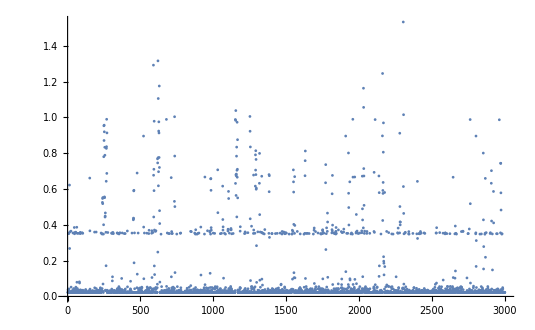

```mathematica
ListPlot[z2crit,PlotRange->All]
```

```mathematica
z6crit={0.1372776,0.2156995,0.2812322,0.2338193,0.3777282,0.4384785,0.6337802,0.6734753,0.6232364,0.845288,0.5987098,0.2971484,0.3161869,0.397686,0.5645937,0.5574595,0.7566217,0.5436675,0.5915293,0.2244034,0.5680453,0.8042927,0.8389034,1.012994,0.9629536,0.9885654,0.8805243,0.8741436,0.9782378,0.7576301,0.3216152,0.4286773,0.696834,0.7551702,0.846688,0.7892882,0.6725019,0.4821161,0.3559144,0.5286001,0.4560413,0.7160823,0.5936203,0.4020907,0.3511232,0.3708038,0.5762844,0.7653828,0.8037657,0.8328254,0.9410414,0.9056746,0.902827,0.863404,0.9629873,0.7737694,0.6309897,0.7343947,0.7626902,0.6410154,0.73909,0.7790229,0.9721928,0.9429792,0.9254513,0.635156,0.5179768,0.4686979,0.4774367,0.344752,0.4336923,0.5803642,0.5395279,0.5541821,0.3461781,0.5755138,0.578593,0.4471715,0.5710596,0.348966,0.4708831,0.594305,0.5602798,0.6764113,0.7201017,0.7515113,0.5497615,0.6963145,0.6105461,0.6004333,0.779096,0.8244991,0.6323096,0.370423,0.4850203,0.3552984,0.4945354,0.5283769,0.5932859,0.6357937,0.625349,0.7668222,0.6272711,0.4519043,0.6551056,0.8077297,0.659085,0.7424088,0.6295401,0.890419,0.6924515,0.8201199,0.6739935,0.7542006,0.7691498,0.6658363,0.7405796,0.7840812,0.6341953,0.6445484,0.5060825,0.5746009,0.5471789,0.4499925,0.593551,0.3838272,0.7020321,0.7414761,0.5457796,0.6424236,0.5572974,0.6739547,0.6794695,1.038497,1.093892,0.9796143,0.7219805,0.7660784,0.5718651,0.4935659,0.6645908,0.6395092,0.3454024,0.3267244,0.3168132,0.4783605,0.647356,0.4703903,0.6289374,0.5084776,0.5223936,0.5993239,0.461256,0.6266264,0.5396112,0.5306524,0.341507,0.4050992,0.2678547,0.3091609,0.3941218,0.6608086,0.6495533,0.62371,0.8094139,0.5879485,0.9650726,0.7647845,1.049848,1.125575,0.6510252,0.7302545,0.4407997,0.5143013,0.3883648,0.2920322,0.6073971,0.6121025,0.5472381,0.4857006,0.4988346,0.4812648,0.2780711,0.4237906,0.2824294,0.7185739,0.7576708,0.9138718,0.7999458,0.8768527,0.8871683,0.8141448,0.8203157,0.8063126,0.8302771,0.6153762,0.5494938,0.4724039,0.624651,0.7070338,0.4657695,0.5313091,0.6067123,0.9381008,0.7352327,0.7683882,0.6834647,0.4208044,0.4535268,0.7470531,0.6947371,0.8168507,0.5136255,0.5947527,0.5334422,0.5836913,0.3667844,0.4403216,0.2724336,0.5312856,0.5595913,0.5937945,0.3324331,0.3924224,0.4204877,0.4856637,0.4581782,0.5294794,0.4760068,0.3303185,0.3856913,0.3089333,0.6129189,0.8598639,0.6128718,0.6020591,0.6191337,0.6592814,0.4532808,0.3845234,0.3257453,0.2435322,0.3661766,0.493777,0.6270746,0.4818179,0.3157889,0.4361909,0.2484589,0.1954091,0.2352962,0.3355681,0.392608,0.492665,0.4365114,0.4454219,0.6315575,0.6959108,0.8696003,0.9334024,0.8617598,0.8465239,0.5432243,0.9262937,0.8627294,0.6312091,0.7727623,1.064147,0.7453772,0.9549561,0.6345005,0.7298717,0.6398665,0.7110246,0.895565,0.9166737,1.027205,0.4134878,0.4884205,0.6145636,0.4847794,0.3667488,0.5712503,0.580623,0.2659683,0.4408391,0.4440231,0.438324,0.3692138,0.100563,0.1557331,0.1508541,0.2524917,0.6597328,0.6098875,0.4269314,0.2731476,0.3082403,0.7938112,0.9776453,0.9369799,0.5551485,0.8040028,0.7859256,0.4036109,0.4881973,0.9726232,0.856226,0.5727463,0.4978682,0.5192668,0.6310253,1.076155,0.8194835,0.6971042,0.7923387,0.716507,0.4370448,0.5163524,0.5499268,0.4435883,0.439696,0.4110324,0.511851,0.3868917,0.4225407,0.4815369,0.7241058,0.366518,0.2173564,0.5460911,0.6527049,0.6195393,0.550279,0.6102352,0.6110764,0.3987808,0.5591406,0.6063125,0.5867755,0.4116434,0.6585128,0.5590343,0.6254063,0.4038048,0.4818058,0.6035513,0.4587581,0.4189491,0.1907336,0.4205132,0.3413817,0.5056992,0.4608459,0.3991591,0.2205925,0.3513355,0.4587135,0.4427897,0.335043,0.4763641,0.3969314,1.159424,0.6014335,0.7032413,0.5249805,0.4099471,0.4781997,0.413606,0.2026361,0.4182097,0.3637244,0.3217818,0.197169,0.1665739,0.3751507,0.3027325,0.3106219,0.3324992,0.6239065,0.3262043,0.5811081,0.870629,0.8697662,0.983579,0.692744,0.5956644,0.8587787,0.8211517,0.8927402,0.5539913,0.6682104,0.4096496,0.6350104,0.4350713,0.6497714,0.8056959,0.6861852,0.6673858,0.809981,0.9885737,0.5105171,0.304081,0.4541633,0.4616706,0.4966342,0.6233088,0.4614296,0.5392526,0.5824986,0.5857493,0.7796892,0.761919,0.3055121,0.8056971,0.4457735,0.4239388,0.3884239,0.4496841,0.360171,0.3151487,0.312933,0.3284582,0.5039768,0.6293659,0.3924879,0.7372717,0.5504017,0.8027808,0.5032718,0.815183,0.771377,1.048307,0.5312049,0.8584487,0.849261,1.139769,0.7694365,0.6717695,0.4720014,0.5991968,0.5722212,0.3977706,0.5600039,0.7274386,0.6032124,0.7307943,0.9329535,0.7070726,0.9205424,0.5846367,0.8889529,0.7836189,0.7820632,0.8128389,0.6750902,0.5332712,0.4634775,0.4613711,0.4725679,0.3408108,0.4870294,0.7774684,0.9116554,0.9215221,0.9360161,0.7213923,0.4820735,0.3391584,0.6235327,0.6994972,0.3868917,1.005676,0.8336582,0.7111772,0.350289,0.4362106,0.265131,0.3688151,0.2385349,0.3093084,0.4187075,0.4337139,0.4383501,0.7815775,0.5929337,0.5145664,0.8185329,0.7587141,0.9189822,0.6758963,0.51334,0.4717643,0.3801416,0.4679184,0.4140829,0.7228292,0.7023169,0.6709017,0.4024169,0.4909286,0.3332653,0.2158852,0.1245632,0.07900429,0.1546764,0.1649971,0.223306,0.3855209,0.4492277,0.6905562,0.810442,0.7416229,0.9390806,0.5594355,0.5606569,0.8186347,0.679231,0.8484154,0.6099739,0.825669,0.8737513,0.8744037,0.4381282,0.4207942,0.5207424,0.5690073,0.6281173,0.3808422,0.3997478,0.5167682,0.7476,0.5259737,0.4430949,0.4884923,0.3832016,0.4627673,0.4929161,0.4348679,0.6488082,0.6494541,0.7772293,0.8962638,0.523318,0.6916904,0.6941395,0.849301,0.6306394,0.8225753,0.8533401,0.8747425,0.7415568,0.8400402,0.7314829,0.8161749,0.5725912,0.7351615,0.6575858,0.4080276,0.490277,0.416851,0.3062827,0.6547248,0.614165,0.5723521,0.7433389,0.5145887,0.7318122,0.7566662,0.8461571,0.9217447,0.8953349,0.7820562,0.8973198,0.681024,0.5297527,0.5236874,0.4695594,0.3082612,0.3562152,0.3958575,0.3853824,0.1138,0.3109042,0.331721,0.6792711,0.3859908,0.4901632,0.2576854,0.4211566,0.531669,0.438694,0.544836,0.4074981,0.5159525,0.2472897,0.4298681,0.3753179,0.5339534,0.7683398,0.3470389,0.328139,0.2991905,0.3219255,0.2674573,0.3096167,0.3422203,0.4323871,0.3931046,0.3562508,0.2643973,0.1828238,0.4445928,0.4586671,0.4986909,0.5615597,0.6865253,0.7633375,0.7246799,0.8431009,0.597648,0.3339685,0.326287,0.3712565,0.5951189,0.427201,0.4157041,0.7668375,0.7666779,0.8047899,0.705204,0.9716963,1.113511,1.004358,0.8669001,0.9882292,1.037998,1.014444,0.9171435,0.5999902,0.7825381,0.9377823,0.923406,0.9828441,0.9060122,0.38543,0.4967849,0.3155861,0.5827312,0.9702085,0.5287056,0.481404,0.3740451,0.3708032,0.2999032,0.1602802,0.2693736,0.8653412,0.7326056,0.6263244,0.6421051,0.833128,0.7108778,0.7316011,0.9651267,0.8454196,0.7960237,0.8297482,0.5702178,0.8506368,0.6887703,0.7375616,0.6253878,0.4017181,0.6192774,0.5749843,0.3754095,0.4786587,0.5506967,0.5553367,0.5153459,0.7253107,0.6009395,0.6131198,0.5874411,0.7491035,1.001886,0.8168055,0.9011542,0.6928444,0.3653463,0.3668855,0.3258591,0.3630676,0.4097398,0.6630351,0.749157,0.9599094,0.8490188,0.5445627,0.5421442,0.4499105,0.558609,0.6575584,0.7101886,0.6939608,0.9351451,0.8726667,0.8197855,1.101561,0.7321994,0.3905582,0.3311494,0.4526685,0.5454611,0.7377428,0.4557025,0.2997131,0.590037,0.3025481,0.2552885,0.2264163,0.2012672,0.3973878,0.2923807,0.3032144,0.4380805,0.3399633,0.500742,0.5426248,1.09814,0.9737708,0.6681716,0.5035185,0.942325,0.8619754,0.5700976,0.5218818,0.4612052,0.3745105,0.5845585,0.5530936,0.8013496,0.7894096,0.6523749,0.8899555,0.8724474,0.4595083,0.5364177,0.5147896,0.5268402,0.6640466,0.6474565,0.5786483,0.5752761,0.4295966,0.370512,0.5439523,0.5378323,0.6062183,0.6181628,0.6035004,0.6693446,0.5926177,0.3958836,0.5210991,0.4042454,0.6175048,0.3249957,0.5946026,0.595005,0.4324964,0.7627437,0.7731838,0.5616538,0.610117,0.5408325,0.5543079,0.5117645,0.3581454,0.7677091,0.5328178,0.8793405,0.717802,0.4921767,0.468139,0.483717,0.5138162,0.3833065,0.3073025,0.2059587,0.2849916,0.7768116,0.5833397,0.8499553,0.8038763,0.3777243,0.901041,0.6171576,0.8826421,0.7349828,0.4162706,0.6141078,0.7300968,0.5480296,0.6103891,0.678903,0.5460415,0.6669719,0.8186525,1.013784,0.7408136,0.6536655,0.4628538,0.4097335,0.4026985,0.4516958,0.4406528,0.5888373,0.6935247,0.923989,0.7977321,0.86022,0.8087368,0.880483,0.8735574,0.8640442,0.6272246,0.7151617,0.4707038,0.5077858,0.6397661,0.6284657,0.5606149,0.5437864,0.4881128,0.7007192,0.5970078,0.3824285,0.295969,0.8807443,0.9287885,0.4501674,0.3235785,0.3301983,0.2835102,0.276275,0.727698,0.5100174,0.81224,0.5140941,0.5414505,0.5781619,0.4453653,0.5237758,0.473093,0.6377036,0.5349382,0.3461577,0.2209841,0.4194826,0.4031035,0.4082807,0.3662243,0.5662613,0.6084639,0.6798903,0.5816199,0.7060947,0.4371707,0.4322427,0.2183704,0.3782527,0.4135253,0.5360343,0.3283749,0.3436413,0.4462999,0.1947498,0.4907856,0.2417774,0.2637736,0.320453,0.279878,0.4784762,0.4558023,0.3595607,0.3127155,0.4342683,0.4165154,0.3286851,1.069061,0.8990657,0.9842352,0.6744041,0.7371566,0.7388319,0.6845506,0.3828411,0.4973768,0.7282416,0.5809116,0.7131176,0.8164368,0.8585453,0.7293829,0.8577551,0.5374616,0.5634226,0.8532512,0.7556528,0.485953,0.5694885,0.5515366,0.8891869,0.8926017,0.8637886,0.9103355,0.6555354,0.4851475,0.3519929,0.2680543,0.3291696,0.243194,0.3633684,0.4882686,0.3595956,0.4471976,0.3394343,0.3062674,0.2336687,0.3381004,0.1950614,0.2457047,0.2214883,0.2083073,0.4791241,0.32466,0.2242031,0.5133286,0.3036258,0.4869162,0.3964914,0.5188408,0.6335373,0.6979873,0.8931103,1.008891,0.9003944,0.6750234,0.6585541,0.6001091,0.5480328,0.7415174,0.5037117,0.7481009,0.2867807,0.5564722,0.543328,0.4099706,0.5060711,0.3923486,0.5420024,0.7995052,0.7890517,0.5731525,0.8412552,0.9319172,0.6195895,0.8542951,0.6097889,0.862992,0.6717014,1.006662,0.9610132,0.867651,0.6633231,0.7879092,0.8178183,0.8583991,0.8738976,0.8895347,0.9210936,0.8135313,0.7850666,0.7178148,0.7117996,0.4573383,0.3777663,0.4628251,0.5607001,0.6087024,0.4130256,0.5894794,0.6344141,0.7339287,0.6640562,0.8188744,0.9361007,0.6180077,0.3859685,0.2458712,0.2811909,0.4160347,0.4836172,0.3874734,0.3906371,0.5067787,0.2315916,0.5169932,0.2332808,0.1793143,0.2790311,0.4787318,0.5587203,0.4640541,0.4704647,0.3956229,0.4480203,0.5030022,0.5189285,0.557649,0.8454126,0.545524,0.7255605,0.7557335,0.6086845,0.393261,0.3476156,0.7523766,0.686732,0.6524932,0.7938818,0.6724237,0.3647258,0.394043,0.5882797,0.4195678,0.5014299,0.4337114,0.5265058,0.4172173,0.4825732,0.7573802,0.6972345,0.4797484,0.3114116,0.5899417,0.7383906,0.6543936,0.4960219,0.3353869,0.6068929,0.8639787,0.6677901,0.2945048,0.5531254,0.683089,0.8005461,0.9062729,0.7879626,0.5162246,0.4878661,0.5646496,0.5282091,0.5905043,0.5101363,0.5947533,0.486414,0.7586174,0.694343,0.7740396,0.8412342,0.7646052,1.079967,0.6599897,0.6171538,0.7408123,1.002787,1.004016,0.8492655,0.7975597,0.7171485,0.6641363,0.6973839,0.4311733,0.3226776,0.3614349,0.5725346,1.063342,0.8594049,0.9417407,0.9038627,0.6283373,0.4972948,0.9859015,1.138561,0.9007143,0.8206342,0.7021014,0.7624099,0.5988083,0.4548181,0.6344478,0.8666878,0.684138,0.735789,0.7303302,0.7456284,0.8226681,0.4181747,0.4694182,0.5487289,0.776247,0.8481388,0.631726,0.772824,0.8514716,0.8830923,0.695303,0.5731831,0.3016828,0.2100455,0.3817145,0.3703086,0.3063463,0.6261991,0.9287586,0.7512335,0.7249292,0.611283,0.3880965,0.4195175,0.4163361,0.3976835,0.5557117,0.6505725,0.3735981,0.4316444,0.6798242,0.8119692,0.6790829,0.9169363,0.5528368,0.3697281,0.4622835,0.5118555,0.8220081,0.7879289,0.8517584,0.6300704,0.5798041,0.5258376,0.4092197,0.5432047,0.895848,0.7628301,0.8461107,0.9151198,0.710516,0.7001362,0.8399798,0.7206389,0.5595531,0.7732906,0.7729747,0.6317902,0.3007755,0.403691,0.3949865,0.9595013,0.9717204,0.9492773,0.8229847,1.187889,0.8047873,0.8740298,0.5956809,0.6459599,0.8702406,1.046731,0.6486048,0.4440835,0.6420771,0.5183538,0.5184664,0.4059703,0.679376,0.9615809,0.8471438,0.9651769,0.8020636,0.6414236,0.9055182,0.6797237,0.8885136,0.9841779,0.628109,0.4487101,0.3396422,0.333779,0.3514957,0.4436436,0.2131615,0.2187309,0.256602,0.4326757,0.5759697,0.4537881,0.6758289,0.8033079,0.746144,0.5767269,0.530908,0.9625823,1.224122,0.6202666,0.4728699,0.5053457,0.5815277,0.7033405,0.6763217,0.4770508,0.2960033,0.5499496,0.5787081,0.7894809,0.6147035,0.3707848,0.300787,0.2103271,0.3396956,0.4647522,0.4965948,0.3991369,0.7488086,0.391805,0.3366064,0.4043414,0.5066109,0.6198406,0.4537214,0.3709672,1.065818,0.7796879,0.9295343,0.7796078,0.7162825,0.5670204,0.587429,0.8139553,0.3391895,0.3338382,0.3933334,0.6337585,0.6706626,0.6030235,0.5881094,0.7294337,0.6407146,0.3072275,0.250672,0.4318053,0.5183665,0.3818499,0.2932739,0.3382499,0.3744202,0.648339,0.7237937,0.6519032,0.6103789,0.633517,0.8763924,0.7860934,0.9925359,0.7724298,0.6517735,0.4720014,0.5367355,0.3327573,0.2919604,0.2593931,0.2494787,0.4101613,0.4868921,0.783734,0.7705905,0.8124733,1.045681,0.9349995,0.4705684,0.1930765,0.3748379,0.2054386,0.3017744,0.3854815,0.3933659,0.4865971,0.4574604,0.3114236,0.2646707,0.4208584,0.4708519,0.4268844,0.4731865,0.3795007,0.7704258,0.6668352,0.6803621,0.4661242,0.6753432,0.7834625,0.6801345,0.6861617,0.8523032,0.8696346,0.9667759,0.7269224,0.7945004,0.9216563,0.6422857,0.4772104,0.6631126,0.8015493,0.6131319,0.7910551,0.8675474,0.7264048,0.4891656,0.4511051,0.3992761,0.7448591,0.936004,0.7441692,0.7076664,0.6589127,0.7729359,0.696085,0.3889192,0.4867764,0.333142,0.6736692,0.343221,0.2554226,0.4049683,0.4419498,0.4922149,0.3644276,0.5521584,0.6601219,0.7013976,0.8891157,0.7913927,0.7238216,0.6401018,0.6058871,0.3628553,0.7066714,0.3094686,0.5062663,0.4848785,0.4302724,0.2740892,0.2965482,0.5616671,0.5096557,0.6925291,0.9849116,0.9473228,0.9286613,0.9039339,0.773332,0.7947731,0.7164282,0.7335358,0.7651075,0.7352962,0.6356856,0.6019338,0.5817941,0.5773067,0.7507274,0.3870093,0.8497359,0.6556079,0.7959353,0.4876251,0.290781,0.3874137,0.449468,0.5824776,0.7305571,0.6747049,0.871006,0.8140539,0.70386,0.5287609,0.2740421,0.3173803,0.4930878,0.2248116,0.4361674,0.4493987,0.439092,0.3796673,0.4297339,0.5163378,0.6334089,0.4000009,0.3653647,0.2902476,0.3048643,0.2523111,0.4136295,0.7576097,0.6614024,0.7846801,0.6292547,0.7250423,0.7273954,0.6201051,0.9035632,0.7061901,0.6915881,0.5877991,0.9303392,0.3595263,0.413243,0.3916079,0.7347857,0.5018139,0.3819491,0.308986,0.3815778,0.4814905,0.3495776,0.6359965,0.7310861,0.843942,1.10031,1.122948,1.028398,0.7903767,0.6559353,0.8345782,0.9379343,0.7101727,0.6493944,0.7962952,0.6968727,0.5652892,0.4168358,0.3949553,0.4173406,0.4445089,0.3155874,0.3187326,0.8354874,0.8233026,0.934742,0.7773838,0.5918636,0.6363341,0.7507877,0.7198798,0.7541193,0.6468309,0.6781712,0.5693067,0.7671928,0.4346797,0.7975127,0.8051224,0.6926619,0.6999716,0.6640676,0.6559175,0.6941013,0.7906113,0.49639,0.3132979,0.796072,0.4298198,1.004226,0.8355885,0.7130827,0.8222504,0.7249057,0.7233188,1.011076,0.9329758,0.7188473,0.8206253,0.6336924,0.7442341,0.6638845,0.7966862,0.9596628,0.6924693,0.8753179,0.5820694,0.8196812,0.6412945,0.8357684,0.5638574,0.6384926,0.6118107,0.6222922,0.6288185,0.8542589,0.7341747,0.6441168,0.4991296,0.6327083,0.4541143,0.4355024,0.797404,0.6391093,0.8970878,0.6779563,0.8367157,0.4974531,0.7831027,0.4330127,0.6356615,0.3319333,0.6434854,0.5102196,0.3942909,0.5349026,0.5609366,0.4026998,0.6302046,0.5246162,0.5501029,0.5341619,0.6578586,0.6298854,0.6557274,0.8355993,0.7258727,0.7227904,0.8125204,0.8562139,0.8925362,0.5599918,0.7689317,0.492068,0.4371319,0.5546736,0.4831397,0.739797,0.7273287,0.6098379,0.7868182,0.7204444,0.5794074,0.5872726,0.5741603,0.243728,0.3867448,0.449482,0.6311111,0.3741214,0.3573043,0.391243,0.3383242,0.2672876,0.3416958,0.5221621,0.5082366,0.3505198,0.3165716,0.5865352,0.8801626,0.8552024,0.9908085,0.8865007,0.6332392,0.6322657,0.7706897,0.6511345,0.819767,0.9371993,0.8333009,0.7415174,0.4853408,0.4401093,0.4705957,0.154295,0.2222475,0.4131616,0.3859164,0.4683965,0.4010061,0.3154399,0.6922347,0.8482838,0.4604912,0.5933437,0.4981607,0.7139747,0.6371524,0.6892128,0.8358154,0.4162178,0.5673892,0.4805088,0.5762832,0.3289973,0.5665512,0.4609598,0.2346973,0.2297491,0.5238203,0.5548128,0.4405193,0.615284,0.3785159,0.33881,0.4032313,0.5076364,0.6600711,0.5785128,0.7361953,0.5151157,0.8251209,0.837923,0.8787022,0.8933868,0.8610706,0.6772131,0.946703,0.7733955,0.8563697,0.756197,0.917539,1.101319,0.7780279,0.7373155,0.93967,0.7594013,0.4092751,0.27174,0.3548343,0.4334278,0.6096586,0.3803539,0.6991431,0.845459,0.9611728,0.6197332,0.6224887,0.5263361,0.5350412,0.5229861,0.3614337,0.6426691,0.5708288,0.2651081,0.4586639,0.5706209,0.3785515,0.6079019,0.3678379,0.6228561,0.4531498,0.377477,0.4260833,0.7496243,0.5646242,0.6092021,0.7442443,0.7254709,0.5301616,0.6084532,0.6925888,0.9732641,0.5038757,0.5144297,0.6405271,0.5894,0.4796429,0.6245868,0.6755842,0.899896,0.7162794,0.694184,0.8146414,0.5422987,0.4692962,0.5244758,0.3568433,0.5466086,0.821387,0.7014319,0.5205797,0.5137959,0.5679423,0.5805525,0.3809331,0.3132795,0.5784957,0.351361,0.2869568,0.5246181,0.7949899,0.7019457,0.5146332,0.6986669,0.6117859,0.493475,0.4596666,0.4984983,0.6087265,0.7001324,0.2966455,0.375508,0.1678365,0.275842,0.3291779,0.5305799,0.3560677,0.3210494,0.2336623,0.3891436,0.2364318,0.3278345,0.9350313,0.7426027,0.3376802,0.2653154,0.3550085,0.5377496,0.6325665,0.5698433,0.8327065,0.8484491,0.9271272,0.6312332,0.7098338,0.4106808,0.2200826,0.257679,0.4202678,0.4730778,0.3046373,0.3217945,0.3145199,0.4245338,0.7554932,0.7402477,0.8504747,0.5231387,0.9169827,0.7027925,0.919358,0.8760573,0.9487896,0.9718965,0.944479,0.780468,0.6654085,0.8966421,0.5865358,0.677407,0.5254523,0.5025063,0.6608652,0.5582861,0.361824,0.7423369,0.6404756,0.6965275,0.7023875,0.824756,0.8999233,0.8710009,0.8113556,0.643645,0.6391062,0.4124343,0.3578021,0.4517454,0.281718,0.5969798,0.405866,0.6909651,0.5164198,0.3622354,0.6042678,0.4618835,0.440368,0.5712045,0.702549,1.011716,0.5515633,0.585029,0.715978,0.727178,0.7270355,0.9850299,0.5022799,0.4837272,0.706632,0.4185251,0.5504996,0.3505866,0.8653654,0.7704118,0.8971246,0.4932537,0.4045906,0.49849,1.003527,0.4628442,0.6709868,0.624576,0.7355665,1.009439,0.7188098,0.5753778,0.4037552,0.5282898,0.2380594,0.3784676,0.3931427,0.5865116,0.8095837,0.4442495,0.3926703,0.6680164,0.5307344,0.343778,0.4445451,0.3707517,0.4961465,0.313956,0.4092522,0.3603064,0.4770667,0.3305334,0.5617809,0.6004753,0.4418322,0.633859,0.6759555,0.9303627,0.516189,0.4036986,0.3519891,0.2180462,0.2712822,0.1247845,0.09014702,0.1643156,0.3885727,0.5701548,0.6807874,0.4438903,0.3500455,0.5850945,0.2455514,0.3945974,0.5838782,0.5944608,0.4854902,0.5318693,0.6792056,0.9671593,0.5898425,0.5075067,0.5938257,0.8138943,0.9012108,0.8741589,0.8240986,0.7292995,0.7467505,0.4604308,0.5410423,0.5277882,0.4456991,0.553929,0.612936,0.5924193,0.4265614,0.509154,0.6571636,0.7937673,0.5396525,0.5650603,0.5225894,0.7739207,0.3746802,0.225029,0.3874919,0.4614271,0.7156321,0.8319251,0.9964873,0.6082592,0.674848,0.6623116,0.891833,0.9721451,0.6998762,0.4562594,0.6556085,0.7356237,0.7416013,0.3953578,0.2722778,0.2813784,0.2790903,0.2895101,0.4857216,0.3617643,0.3504938,0.4139284,0.2574495,0.2426586,0.5655562,0.3887793,0.8213444,0.5990989,0.4886449,0.7400926,0.4067001,0.3456116,0.5608959,0.7642009,0.6274738,0.5101039,0.3917453,0.4727586,0.456665,0.5060616,0.4329287,0.396677,0.3462709,0.5178814,0.5203629,0.586553,0.8300476,0.9005846,0.6135051,0.3614159,0.3188178,0.45375,0.6208178,1.041641,0.4986585,0.4956493,0.2807992,0.1777814,0.1445503,0.2664948,0.4445941,0.2934761,0.3399792,0.3144588,0.3040104,0.2212041,0.3373941,0.4560325,0.6804752,0.579958,0.6541793,0.7839165,0.5173143,0.4261678,0.3581155,0.5398973,1.136098,0.9503492,0.9592997,0.8882008,0.7053649,0.6908569,0.6356653,0.7688726,0.606245,0.6449973,0.5928549,0.7180748,0.905847,0.73176,0.6623319,0.6583462,0.3247967,0.4811103,0.5130342,0.864865,0.6973286,0.6861369,0.8319079,0.9990406,0.8833536,0.706475,0.6104101,0.5749716,0.7060878,1.088285,0.6913325,0.3763313,0.6106784,0.4590982,0.3847122,0.5022234,0.5808557,0.5776736,0.7720782,0.8070679,0.9513817,0.629982,0.683494,0.3822047,0.7816614,0.7409903,0.7035345,0.8087858,0.8148779,0.9266186,0.8454635,0.813598,0.6417148,0.6118781,0.4567267,0.4658133,0.5753956,0.5603613,0.564366,0.5154419,0.8173288,0.7084853,0.7002481,0.618391,0.6293768,0.4273307,0.5459347,0.5459124,0.4857966,0.4577274,0.7417094,0.8403327,0.7823582,0.6260891,0.7991969,0.9311581,0.8286915,0.7117526,0.812624,0.7262592,0.7640051,0.7506384,0.4887536,0.3590819,0.6214415,0.6334369,0.7640266,0.5713196,0.9239935,0.7137896,0.5538998,0.6915309,0.7373835,0.5103811,0.3815982,0.4671485,0.655009,0.6028303,0.6236827,0.4941425,0.8605741,0.6618494,0.6010927,0.513616,0.5147318,0.5751438,0.6518097,1.014952,0.8755525,0.7710463,0.6792336,0.7066149,0.9175409,0.9113191,0.6309223,0.6318595,0.5194817,0.5267214,1.014364,0.668218,0.8812568,0.6405901,0.6230177,0.5657787,0.817894,0.5624943,0.4300734,0.4268265,0.6426487,0.3937461,0.2512697,0.3049673,0.390969,0.3658912,0.7300129,0.425712,0.3408337,0.4496854,0.3737621,0.3767669,0.5935466,0.4171352,0.4481049,0.5054773,0.3682944,0.4277897,0.6573257,0.5533276,0.4841245,0.4173946,0.7968795,0.9008573,0.8511747,0.5423991,0.6409677,0.6873322,0.6517462,0.4940961,0.4632098,0.4630718,0.4350236,0.3035768,0.4634743,0.387387,0.3647321,0.6099917,0.5455679,0.2391135,0.333367,0.2992846,0.3312423,0.752381,0.9686464,0.7598528,0.479112,0.5507787,0.5312354,0.6885948,0.7113253,0.6815745,0.6909561,0.2914772,0.3395875,0.2806308,0.4544436,0.5709203,0.4940548,0.426431,1.04434,0.8693905,0.8266208,0.8012409,0.5250098,0.422156,0.4327742,0.3524958,0.4944261,0.6225535,0.3444278,0.5050678,0.4708697,0.4638538,0.647953,0.8499781,0.9776999,0.7203878,0.7457905,0.801536,0.8496622,0.906449,0.6449293,0.562467,0.5916176,0.5296396,0.4016241,0.5108878,0.3818207,0.273304,0.1910051,0.2993711,0.2655977,0.2873402,0.3233433,0.3686625,0.2124176,0.3881181,0.6794122,0.7392687,0.7961127,0.7079296,0.715957,0.6132044,0.6836472,0.7389774,0.8046551,0.7717152,0.5074406,0.5974471,0.4155038,0.9644794,0.7931601,0.6515751,0.7093436,0.5769157,0.8487873,0.7884681,0.8153426,0.8817972,0.8369408,0.9064503,0.8796209,0.8123608,0.8932819,0.5495962,0.7473005,0.7965876,0.6433119,0.431544,0.5497698,0.4409263,0.5155481,0.4255562,0.6340326,0.7029413,0.5207259,0.6564967,0.6014907,0.6127593,0.6261959,0.5052694,0.5764243,0.6674468,0.6277167,0.8518066,0.6756624,0.4904639,0.5286109,0.6678976,0.7397951,0.6467171,0.4620399,0.2799104,0.4277795,0.3362815,0.4555912,0.5367953,0.4826749,0.6342596,0.5018412,0.48209,0.3550129,0.3579922,0.2613462,0.3347696,0.78361,0.3450572,0.3856977,0.4211496,0.3965912,0.5113392,0.6192608,0.4360377,0.5379219,0.3444983,0.9187393,0.6247883,1.165049,0.7628066,0.8572617,0.8305639,0.9401404,0.850036,0.6832988,0.4487826,0.4423835,0.5671324,0.9732107,0.9368808,0.9723721,0.5724424,0.74569,0.4331512,0.4509265,0.6490619,0.5738761,0.7003676,0.7718105,0.7876238,0.7446531,0.8240789,0.6816031,0.5488771,0.5547594,0.6681474,0.4919822,0.434803,0.6217372,0.6067657,0.4397157,0.7166659,0.6931369,0.7479706,0.7970448,0.6044318,0.7753595,0.9320094,0.6947066,0.5573406,0.9308128,0.4613609,0.3129501,0.3373254,0.2096049,0.3485114,0.3013465,0.4994392,0.4901842,0.5032272,0.7322941,0.6437683,0.6882305,0.9389681,0.74528,0.562116,0.9585775,0.6635908,0.6123168,0.7545478,0.3163478,0.4476497,0.6280734,0.5890688,0.6903388,0.583732,0.6194007,0.3860219,0.4230169,0.3608958,0.352951,0.352691,0.8872223,0.4992186,0.5859737,0.5968298,0.3897514,0.3316116,0.4755039,0.5204265,0.8342444,0.8199457,0.9159979,0.7055836,0.8222968,0.9976648,0.8973192,0.8202337,0.7625974,0.9359602,0.5303974,0.6800117,0.8793297,0.7679628,0.9195881,0.7993044,0.786651,0.7843742,0.6426888,0.8540313,0.4560979,0.649821,0.5634174,0.4456972,0.720513,0.8710982,0.690349,0.7293765,0.652827,0.6630027,0.7071394,0.8522466,0.9617869,0.5230071,0.5874742,0.4784381,0.74263,0.5417932,0.5439116,0.51157,1.025128,0.6770719,0.6742891,0.698136,0.7814929,0.6176395,0.3692894,0.4545237,0.3559062,0.2221305,0.5109164,0.3527699,0.4948807,0.5269527,0.3517221,0.6182442,0.3161481,0.806682,0.7457523,0.6535047,1.012899,1.10884,0.6820857,0.3546264,0.5497494,0.4346727,0.4899139,0.7836527,0.5854467,0.5560595,0.3126113,0.31261,0.3037612,0.2885704,0.3709615,0.4735851,0.3366369,0.3523839,0.5226294,0.6127478,0.6490345,0.6255831,0.5004076,0.4191024,0.3741258,0.3589624,0.2265294,0.3189939,0.3021552,0.4953594,0.5749969,0.8437589,0.7839502,0.3821564,0.2684981,0.5456963,0.3675652,0.3955879,0.3589649,0.4182587,0.3512039,0.3415,0.4306278,0.3845819,0.7341703,0.6169574,0.5420889,0.5395057,0.589084,0.4838047,0.5882511,0.4448408,0.6020921,0.3651689,0.5652911,0.3440755,0.3930779,0.2614498,0.39468,0.2590396,1.093586,0.5778275,0.207016,0.2533328,0.5722059,1.050387,1.059099,0.8753478,0.8152899,0.6040516,0.5022978,0.5537395,0.5306658,0.692873,0.7021148,0.576671,0.5763226,0.4087563,0.4745305,0.5759665,0.6205877,0.9162821,1.014223,0.8299726,0.7492841,0.5790253,0.4869754,0.4218063,0.4883041,0.6316833,0.6607914,0.8085162,0.7180996,0.7907099,0.6382618,0.6262608,0.551672,0.8093707,0.272653,0.3589618,0.4651,0.5308622,0.5250899,0.7628059,0.9869041,0.5250282,0.3995056,0.3705508,0.332915,0.4199969,0.2944088,0.8543091,0.4789969,0.6035824,0.617927,0.7013518,0.3740788,0.4750754,0.6905861,0.5382296,0.5914256,0.3991826,0.3769436,0.3744907,0.5268186,0.7235972,0.8083261,0.901193,0.8809071,0.9373564,0.8291168,0.6995049,0.5956714,0.6875064,0.7220446,1.042049,0.8440368,1.08488,0.705192,0.5213388,0.4499416,0.5848573,0.5224845,0.4765441,0.4896482,0.641428,0.4814854,0.3903828,0.4844043,0.7220561,0.5000884,0.4574407,0.3582859,0.2828897,0.3292446,0.4409205,0.6565711,0.9513226,0.513705,0.5903053,0.4080181,0.3767859,0.5649809,0.553112,0.8759238,0.9001331,0.7265943,0.824852,0.8461031,0.8767974,0.9521503,0.6038603,0.7506351,0.8265762,0.4923808,0.7547665,1.052584,0.854634,0.7790922,0.7484258,0.865132,0.5022666,0.3155225,0.2963588,0.3514595,0.5577704,0.7262396,0.4060504,0.3440787,0.3151945,0.3686988,0.4744237,0.8127855,0.7349555,0.8586992,0.7105529,0.8406175,0.6659266,0.9581484,0.8027147,0.6343288,0.5130405,0.6240807,0.761158,0.8220628,0.5490577,0.4753596,0.5732626,0.4884955,0.7590097,0.5434074,0.4325511,0.3391698,0.6783015,0.5872059,0.5338491,0.6236681,0.5351537,0.657294,0.7812303,0.7300905,0.6109422,0.3882529,0.3307457,0.4427103,0.3256995,0.2709827,0.3356374,0.5345389,0.5845127,0.4142602,0.4438922,0.7276783,0.9184641,0.7830417,1.046368,0.9729812,0.3515288,0.2177932,0.1019325,0.1475614,0.2156442,0.4668808,0.2929332,0.2709255,0.2637113,0.901729,1.015256,0.6698087,0.9150912,0.758077,0.8657195,0.8729083,0.7444719,0.4299787,0.5443491,0.6667227,0.9074243,0.5268339,0.8759753,0.6650359,0.6714134,0.4738019,0.356842,0.4344025,0.4663474,0.4716473,0.6762066,0.4940701,0.5618477,0.5516949,0.4220327,0.7488168,0.7740701,0.8265406,0.8989671,0.9045162,0.6956457,0.8769188,0.9070925,0.7873949,0.7901732,0.8110949,0.7813384,0.422891,0.4278921,0.4815528,0.33041,0.5583503,0.6186244,0.8543835,0.7310009,0.7515411,0.7530047,0.8693511,0.8936329,0.9269619,0.7312171,0.6841068,0.5852369,0.5415122,0.7894434,0.5647463,0.8077475,0.7464994,0.58516,0.5798804,0.4338958,0.5528209,0.85186,0.7768822,0.6382694,0.6018118,0.6461245,0.4664892,0.672383,0.7004115,0.7255179,0.7010759,0.646417,0.50781,0.4123802,0.7299862,0.7042255,0.8384654,0.8997511,0.8681202,0.986241,0.884594,0.6039111,0.6201439,0.6555755,0.6018874,0.4126231,0.9123675,0.7174276,0.5611877,0.7543087,0.7240671,0.7106667,0.5458838,0.8044745,0.8832664,1.011943,0.7051634,0.804184,0.4692307,0.541881,0.5207329,0.5456982,0.3357105,0.5193443,0.4190941,0.6561807,0.6599662,0.7676157,0.661932,0.6162021,0.6215267,0.5380567,0.4705925,0.6082656,0.8422388,0.9826381,0.8173637,0.7592863,1.097008,1.017075,0.6958186,0.7537174,0.5734984,0.5910683,0.8258559,0.6693332,0.4783739,0.7608821,0.6004041,0.8096352,0.8576622,0.9933898,0.9480966,0.8119056,0.7541428,0.5915699,0.4826915,0.439146,0.2984613,0.2862117,0.2110723,0.2014039,0.3849964,0.8647754,0.8387267,1.034039,0.8723838,0.7306271,0.3764553,0.5807559,0.3796043,0.4356575,0.35237,0.2955379,0.3074277,0.2634971,0.6573862,0.4631329,0.4779987,0.2124252,0.3436655,0.34493,0.6187159,0.9176458,0.7932447,0.5079302,0.3664119,0.4526787,0.368152,0.5456346,0.4840762,0.5751852,0.741188,0.9344368,0.8001099,0.6826407,0.8872172,0.8106155,0.6533731,0.4623884,0.4945234,0.5183735,0.403134,0.6819134,0.9945368,0.5716261,0.8858236,0.5547263,0.5449206,0.6217785,0.4512762,0.4068292,0.4047858,0.5486736,0.8461902,0.6001333,0.6692111,0.8024006,0.6458696,0.4914799,0.3093999,0.4845282,0.7053598,0.7937387,0.8584646,0.9896278,0.9508438,0.720246,0.6043205,0.8643125,1.022872,0.8500938,0.7103882,0.5589155,0.4774863,0.5478725,0.6381512,0.7261989,0.656032,0.595412,0.5643406,0.7869911,0.8502268,0.6761081,0.5777245,0.358443,0.2409026,0.1876501,0.1799037,0.173144,0.1152802,0.2408231,0.3963203,0.5087293,0.4329872,0.3266379,0.598863,0.5701942,0.6611614,0.5556768,0.7255084,0.624403,0.7652747,0.5707188,0.6684234,0.3678818,0.2796351,0.3031203,0.2442964,0.2691326,0.3791987,0.4159431,0.6227493,0.3813922,0.4374441,0.581728,0.7908872,0.7421074,0.9438585,0.6241176,0.8122826,0.9059913,0.9604073,0.5979258,0.6281509,0.365682,0.2777036,0.09310722,0.1752675,0.4259561,0.4545759,0.3733858,0.3636863,0.6438395,0.6344967,0.8071188,0.7127209,0.4147199,0.4155394,0.4114603,0.6891747,0.5275313,0.6724612,0.7987283,0.8518645,0.8867849,0.8165919,0.7552694,0.4774749,0.8320154,0.927091,0.3786907,0.4349143,0.371479,0.3078785,0.4859282,0.5739231,0.377135,0.4982974,0.645745,0.8765157,0.7333927,0.7990646,0.769949,0.5175775,0.501882,0.4873498,0.725799,0.7555549,0.9381294,0.9470997,1.040071,0.8810501,0.9853109,0.7579791,0.8833212,0.7317238,0.885198,0.9788812,0.9384435,0.8827146,0.9238968,0.8847618,0.7474785,0.6724701,0.9635589,0.9955953,0.847887,0.9356963};
```

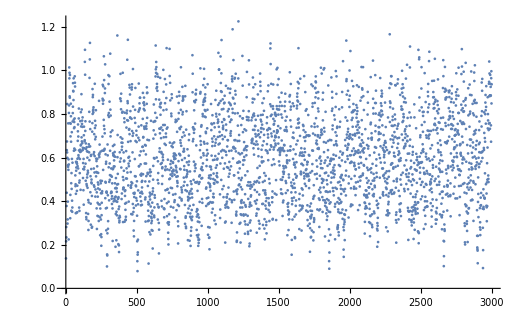

```mathematica
ListPlot[z6crit,PlotRange->All]
```